# Stability and quasinormal modes for black holes with time-dependent scalar hair

This is the companion notebook to the paper https://arxiv.org/abs/2408.01720, where we perform all the calculations appearing there.
Starting with the action for our theory, we study a black hole solution with a scalar that is linearly dependent on time. We first show that this solution indeed solves the equations of motion of the theory, and show an interesting relation between the covariant metric and scalar equations. We then study the stability of odd parity perturbations and show a region in parameter space safe from instabilities. We then obtain the modified Regge-Wheeler equation and the effective potential. We find the corresponding quasinormal modes via the WKB method and apply a Fisher forecast analysis to constrain the parameter of the theory.

This notebook has benefitted from resources and comments provided by:
	- xAct ( http://www.xact.es/ )
	- Johannes Noller
	- Kazufumi Takahashi
	- Simon Iteanu
	- WKB package ( http://arxiv.org/pdf/1904.10333.pdf )

If you use any of the results or techniques in this notebook please cite the repository and [2408.01720] ( https://arxiv.org/abs/2408.01720 ), [2301.10272] ( https://arxiv.org/abs/2301.10272 ).
If you have any comments or feedback please let me know. Thanks!

Sergi Sirera Lahoz
sergi.sirera-lahoz@port.ac.uk
Institute of Cosmology and Gravitation - University of Portsmouth
-Graphics-
August 2024

## 0. Setup and definitions

Here we import xAct and define all relevant geometric objects and Horndeski functions.

```mathematica
<<xAct`xPert`;
<<xAct`xCoba`;
<<xAct`xTras`;
SetOptions[$FrontEndSession,NotebookAutoSave->True]
NotebookSave[]

(*aesthetics*)
SetOptions[SelectedNotebook[],Background->Lighter[Gray, 0.9]];
$CovDFormat="Prefix";
$DefInfoQ=False;
$CVVerbose=False;

(*define manifold and metric*)
dim=4;    
DefManifold[Md,dim,{b,c,d,e,f,i,j,k}];
DefMetric[-1,g[-b,-c],CD,{";","∇"},WeightedWithBasis->AIndex];
PrintAs[RiemannCD]^="R";
PrintAs[RicciCD]^="R";
PrintAs[RicciScalarCD]^="R";
PrintAs[ChristoffelCD]^="Γ";
PrintAs[EinsteinCD]^="G";
PrintAs[Detg]^="g";

(*define scalar field and Horndeski functions*)
DefTensor[phi[],Md,PrintAs->"ϕ"];
DefTensor[X[],Md];
DefScalarFunction[G2,PrintAs->"G_2"];
DefScalarFunction[G3,PrintAs->"G_3"];
DefScalarFunction[G4,PrintAs->"G_4"];
DefScalarFunction[G4X,PrintAs->"G_(4  X)"];
DefScalarFunction[G5,PrintAs->"G_5"];
DefScalarFunction[G5X,PrintAs->"G_(5  X)"];
DefConstantSymbol[Mpl,PrintAs->"M_Pl"];
DefConstantSymbol[lam2,PrintAs->"Λ_2"];
DefConstantSymbol/@{η,λ,Λ,β};
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.3, {2015,8,23}

CopyRight (C) 2003-2020, Jose M. Martin-Garcia, under the General Public License.

Connecting to external linux executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor`  version 1.2.0, {2021,10,17}

CopyRight (C) 2002-2021, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`xPert`  version 1.0.6, {2018,2,28}

CopyRight (C) 2005-2020, David Brizuela, Jose M. Martin-Garcia and Guillermo A. Mena Marugan, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

** Variable $PrePrint assigned value ScreenDollarIndices

** Variable $CovDFormat changed from Prefix to Postfix

** Option AllowUpperDerivatives of ContractMetric changed from False to True

** Option MetricOn of MakeRule changed from None to All

** Option ContractMetrics of MakeRule changed from False to True

------------------------------------------------------------

Package xAct`xCoba`  version 0.8.6, {2021,2,28}

CopyRight (C) 2005-2021, David Yllanes and Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

------------------------------------------------------------

Package xAct`Invar`  version 2.0.5, {2013,7,1}

CopyRight (C) 2006-2020, J. M. Martin-Garcia, D. Yllanes and R. Portugal, under the General Public License.

** DefConstantSymbol: Defining constant symbol sigma.

** DefConstantSymbol: Defining constant symbol dim.

** Option CurvatureRelations of DefCovD changed from True to False

** Variable $CommuteCovDsOnScalars changed from True to False

------------------------------------------------------------

Package xAct`SymManipulator`  version 0.9.5, {2021,9,14}

CopyRight (C) 2011-2021, Thomas Bäckdahl, under the General Public License.

------------------------------------------------------------

Package xAct`xTras`  version 1.4.2, {2014,10,30}

CopyRight (C) 2012-2014, Teake Nutma, under the General Public License.

** Variable $CovDFormat changed from Postfix to Prefix

** Option CurvatureRelations of DefCovD changed from False to True

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

## 1. Theory and background

### Action

```mathematica
L2=G2[phi[],X[]];
L3=-G3[phi[],X[]]CD[b]@CD[-b]@phi[];
L4=G4[phi[],X[]]RicciScalarCD[]+G4X[phi[],X[]]((Scalar[CD[b]@CD[-b]@phi[]])^2-CD[c]@CD[d]@phi[]CD[-c]@CD[-d]@phi[]);
L5=G5[phi[],X[]]EinsteinCD[-b,-c]CD[b]@CD[c]@phi[]-1/6 G5X[phi[],X[]]((CD[b]@CD[-b]@phi[])^3-3CD[e]@CD[c]@phi[]CD[-e]@CD[-c]@phi[]CD[d]@CD[-d]@phi[]+2CD[-f]@CD[-k]@phi[]CD[f]@CD[j]@phi[]CD[k]@CD[-j]@phi[]);
LT=Sqrt[-Detg[]](L2+L3+L4+L5)
```

√-g (G_2[ϕ,X]+G_4[ϕ,X] R-G_3[ϕ,X] ∇^b ∇_b ϕ+G |   |  
b | c G_5[ϕ,X] ∇^b ∇^c ϕ+G_(4  X)[ϕ,X] ((∇^b ∇_b ϕ)^2-∇_c ∇_d ϕ ∇^c ∇^d ϕ)-1/6 G_(5  X)[ϕ,X] ((∇^b ∇_b ϕ)^3-3 ∇^d ∇_d ϕ ∇_e ∇_c ϕ ∇^e ∇^c ϕ+2 ∇_f ∇_k ϕ ∇^f ∇^j ϕ ∇^k ∇_j ϕ))

```mathematica
(*this rule specifies our theory of interest in natural units*)
ncXtheory={G2[phi[],X[]]->-2Λ+2 Mpl^2 η √X[],G3[phi[],X[]]->0,G4[phi[],X[]]->Mpl^2+λ √X[],G4X[phi[],X[]]->D[Mpl^2+λ √X[],X[]],G5[phi[],X[]]->0,G5X[phi[],X[]]->0}
(*the following two rules can be applied at any point*)
(*1. this rule sets geometric units*)
ToGeomUn={Mpl->1,lam2->1}
(*2. this rule brings the theory from 2-parameter form to 1-parameter form*)
ToBeta={η->1,λ->2 β^2}
```

{G_2[ϕ,X]→-2 Λ+2 M_Pl^2 η √X,G_3[ϕ,X]→0,G_4[ϕ,X]→M_Pl^2+λ √X,G_(4  X)[ϕ,X]→λ/(2 √X),G_5[ϕ,X]→0,G_(5  X)[ϕ,X]→0}

{M_Pl→1,Λ_2→1}

{η→1,λ→2 β^2}

Our Lagrangian is then

```mathematica
L=LT/.ncXtheory
(*one-parameter version*)
%/.ToBeta
(*in geoemetric units*)
%/.ToGeomUn
```

√-g (-2 Λ+R (M_Pl^2+λ √X)+2 M_Pl^2 η √X+(λ ((∇^b ∇_b ϕ)^2-∇_c ∇_d ϕ ∇^c ∇^d ϕ))/(2 √X))

√-g (-2 Λ+R (M_Pl^2+2 β^2 √X)+2 M_Pl^2 √X+(β^2 ((∇^b ∇_b ϕ)^2-∇_c ∇_d ϕ ∇^c ∇^d ϕ))/(√X))

√-g (-2 Λ+R (1+2 β^2 √X)+2 √X+(β^2 ((∇^b ∇_b ϕ)^2-∇_c ∇_d ϕ ∇^c ∇^d ϕ))/(√X))

### Perturbations

We also define here the metric perturbations. We do not include scalar perturbations because we restrict to the odd sector.

```mathematica
DefMetricPerturbation[g,h,ϵ];
Unprotect[IndexForm];
(*this selects a colour to differentiate indices referring to the order in perturbations from other indices*)
IndexForm[LI[x_]]:=ColorString[ToString[x],RGBColor["#00a898"]];
Protect[IndexForm];
IndexForm[LI[n]];
DefTensorPerturbation[δϕ[LI[order]],phi[],Md];
```

### Rules

The following rules will take care of selecting contributions only from first order in the perturbations, applying differentiation by parts, specifying a de Sitter spacetime  and the form of the scalar backgorund.

```mathematica
(*keep only first order*)
onlyfirst={h[LI[2],x_,y_]:>0,δϕ[LI[2]]->0}

(* integration by parts rules*)
IBPrule1=XX_*h[LI[1],aa_,bb_]CD[cc_]@CD[dd_]@h[LI[1],ee_,ff_]->-CD[cc]@(XX*h[LI[1],aa,bb])*CD[dd]@h[LI[1],ee,ff]

(*non-Ricci flat spacetime*)
RiccidS={RicciScalarCD[]->4 Λ/Mpl^2,RicciCD[-bb_,-cc_]->Λ/Mpl^2 g[-bb,-cc],RicciCD[-bb_,cc_]->Λ/Mpl^2 g[-bb,cc],RicciCD[bb_,-cc_]->Λ/Mpl^2 g[bb,-cc],RicciCD[bb_,cc_]->Λ/Mpl^2 g[bb,cc]}
BianchiID={CD[-bb_][RiemannCD[bb_,-cc_,-dd_,-ee_]]->0,CD[-bb_][RiemannCD[-cc_,-dd_,-ee_,bb_]]->0}

(*scalar background*)
DefConstantSymbol[q];
DefScalarFunction[phit,PrintAs->"φ"];
DefScalarFunction[psi,PrintAs->"ψ"];
ScalarRules={phi[]->q t[]+psi[r[]]}

(*scalar field kinetic term*)
Xtoϕ=MakeRule[{X[],-(1/2)Scalar[CD[-k][phi[]]CD[k][phi[]]]}];
ϕtoX=MakeRule[{CD[-k]@phi[]CD[k]@phi[],-2X[]}];
```

{h | 2 | x̲ | y̲
  |   |  :>0,δϕ | 2
 →0}

h | 1 | UnderBar[aa] | UnderBar[bb]
  |   |   XX_ ∇^UnderBar[cc] ∇^UnderBar[dd] h | 1 | UnderBar[ee] | UnderBar[ff]
  |   |  →(-h | 1 | aa | bb
  |   |   ∇^cc XX-XX ∇^cc h | 1 | aa | bb
  |   |  ) ∇^dd h | 1 | ee | ff
  |   |

{R→(4 Λ)/M_Pl^2,R |   |  
UnderBar[bb] | UnderBar[cc]→(Λ g |   |  
bb | cc)/M_Pl^2,R |   | UnderBar[cc]
UnderBar[bb] |  →(Λ δ |   | cc
bb |)/M_Pl^2,R | UnderBar[bb] |  
  | UnderBar[cc]→(Λ δ |   | bb
cc |)/M_Pl^2,R | UnderBar[bb] | UnderBar[cc]
  |  →(Λ g | bb | cc
  |)/M_Pl^2}

{∇_UnderBar[bb] R | UnderBar[bb] |   |   |  
  | UnderBar[cc] | UnderBar[dd] | UnderBar[ee]→0,∇_UnderBar[bb] R |   |   |   | UnderBar[bb]
UnderBar[cc] | UnderBar[dd] | UnderBar[ee] |  →0}

{ϕ→ψ[r[]]+q t[]}

### Coordinate basis

```mathematica
DefChart[SdS,Md,{0,1,2,3},{t[],r[],θ[],ϕ[]}];
SdS/:CIndexForm[0,SdS]:="t";
SdS/:CIndexForm[1,SdS]:="r";
SdS/:CIndexForm[2,SdS]:="θ";
SdS/:CIndexForm[3,SdS]:="ϕ";

DefScalarFunction/@{B};
DefConstantSymbol[mass,PrintAs->"M"];

(*metric background*)
gB=DiagonalMatrix[{-B[r[]],1/B[r[]],r[]^2,r[]^2 Sin[θ[]]^2}];
ToM={B[r[]]->1-(2mass)/(Mpl^2 r[])-1/3 Λ/Mpl^2 r[]^2,B'[r[]]->(2mass)/(Mpl^2 r[]^2)-1/3 2 Λ/Mpl^2 r[],B''[r[]]->(-4mass)/(Mpl^2 r[]^3)-1/3 2 Λ/Mpl^2,B'''[r[]]->(12mass)/(Mpl^2 r[]^4)}
(*note that ToB only works for Shcwarzschild*)
ToB={mass->r[]/2(1-B[r[]]),B'[r[]]->(-B[r[]]+1)/r[],B''[r[]]->(2(B[r[]]-1))/r[]^2};

(*scalar background*)
psirules={Derivative[1][psi][r[]]->(q*Sqrt[1-(λ/Mpl^2*B[r[]])/(λ/Mpl^2+η*r[]^2)])/B[r[]],Derivative[2][psi][r[]]->D[(q*Sqrt[1-(λ/Mpl^2*B[r[]])/(λ/Mpl^2+η*r[]^2)])/B[r[]],r[]],Derivative[3][psi][r[]]->D[D[(q*Sqrt[1-(λ/Mpl^2*B[r[]])/(λ/Mpl^2+η*r[]^2)])/B[r[]],r[]],r[]]}

MetricInBasis[g,-SdS,gB];
MetricCompute[g,SdS,All,CVSimplify->ToCanonical];

(*associated Legendre polynomials*)(*m=0*)
DefConstantSymbol/@{l,m,ω};
DefScalarFunction[PL,PrintAs->"P_lm"];

m0=m->0;
PL''[θ_]:=-(l(l+1)-m^2 Csc[θ]^2) PL[θ]-Cot[θ]PL'[θ]/.m0;
PLrules={PL[θ[]]^2*Sin[θ[]]->2/(2l+1),Sin[θ[]]*Derivative[1][PL][θ[]]^2->(2(l(l+1)))/(2l+1),Cos[θ] Subscript[P, lm][θ] Subscript[P, lm]'[θ]->-2 l/(2l+1), Cos[θ] Cot[θ] (Subscript[P, lm]'[θ])^2->(l(l+1)(2l-1))/(2l+1)};

(*spherical harmonics*)(*m=0*)
YLM:=E^(-ⅈ m ϕ[])PL[θ[]]/.m0;

(* odd parity h *)(*m=0*)
DefScalarFunction[h0,PrintAs->"h_0"];
DefScalarFunction[h1,PrintAs->"h_1"];
hO={{0,0,-D[YLM,ϕ[]]/Sin[θ[]]h0[t[],r[]],Sin[θ[]]D[YLM,θ[]]h0[t[],r[]]},{0,0,-D[YLM,ϕ[]]/Sin[θ[]]h1[t[],r[]],Sin[θ[]]D[YLM,θ[]]h1[t[],r[]]},{-D[YLM,ϕ[]]/Sin[θ[]]h0[t[],r[]],-D[YLM,ϕ[]]/Sin[θ[]]h1[t[],r[]],0,0},{Sin[θ[]]D[YLM,θ[]]h0[t[],r[]],Sin[θ[]]D[YLM,θ[]]h1[t[],r[]],0,0}}/.m0;

(*display how the metric perturbations look like*)
hO//Flatten;
Apply[PolynomialGCD,%];
%(1/%*hO//MatrixForm)
```

{B[r]→1-(2 M)/(M_Pl^2 r)-(Λ r^2)/(3 M_Pl^2),B'[r]→(2 M)/(M_Pl^2 r^2)-(2 Λ r)/(3 M_Pl^2),B''[r]→-(2 Λ)/(3 M_Pl^2)-(4 M)/(M_Pl^2 r^3),B^(3)[r]→(12 M)/(M_Pl^2 r^4)}

{ψ'[r]→(q √(1-(λ B[r])/(M_Pl^2 (λ/M_Pl^2+η r^2))))/B[r],ψ''[r]→-(q √(1-(λ B[r])/(M_Pl^2 (λ/M_Pl^2+η r^2))) B'[r])/B[r]^2+(q ((2 η λ B[r] r)/(M_Pl^2 (λ/M_Pl^2+η r^2)^2)-(λ B'[r])/(M_Pl^2 (λ/M_Pl^2+η r^2))))/(2 B[r] √(1-(λ B[r])/(M_Pl^2 (λ/M_Pl^2+η r^2)))),ψ^(3)[r]→(2 q √(1-(λ B[r])/(M_Pl^2 (λ/M_Pl^2+η r^2))) B'[r]^2)/B[r]^3-(q B'[r] ((2 η λ B[r] r)/(M_Pl^2 (λ/M_Pl^2+η r^2)^2)-(λ B'[r])/(M_Pl^2 (λ/M_Pl^2+η r^2))))/(B[r]^2 √(1-(λ B[r])/(M_Pl^2 (λ/M_Pl^2+η r^2))))-(q ((2 η λ B[r] r)/(M_Pl^2 (λ/M_Pl^2+η r^2)^2)-(λ B'[r])/(M_Pl^2 (λ/M_Pl^2+η r^2)))^2)/(4 B[r] (1-(λ B[r])/(M_Pl^2 (λ/M_Pl^2+η r^2)))^(3/2))-(q √(1-(λ B[r])/(M_Pl^2 (λ/M_Pl^2+η r^2))) B''[r])/B[r]^2+(q (-(8 η^2 λ B[r] r^2)/(M_Pl^2 (λ/M_Pl^2+η r^2)^3)+(2 η λ B[r])/(M_Pl^2 (λ/M_Pl^2+η r^2)^2)+(4 η λ r B'[r])/(M_Pl^2 (λ/M_Pl^2+η r^2)^2)-(λ B''[r])/(M_Pl^2 (λ/M_Pl^2+η r^2))))/(2 B[r] √(1-(λ B[r])/(M_Pl^2 (λ/M_Pl^2+η r^2))))}

(0 | 0 | 0 | h_0[t,r]
0 | 0 | 0 | h_1[t,r]
0 | 0 | 0 | 0
h_0[t,r] | h_1[t,r] | 0 | 0) Sin[θ] P_lm'[θ]

We use the background metric to raise and lower indices

```mathematica
ComponentValue[ComponentArray[h[LI[1],-{b,SdS},-{c,SdS}]],hO];
ChangeComponents[h[LI[1],-{b,SdS},{c,SdS}],h[LI[1],-{b,SdS},-{c,SdS}]];
ChangeComponents[h[LI[1],{b,SdS},-{c,SdS}],h[LI[1],-{b,SdS},-{c,SdS}]];
ChangeComponents[h[LI[1],{b,SdS},{c,SdS}],h[LI[1],-{b,SdS},-{c,SdS}]];
ChangeComponents[ChristoffelCDPDSdS[{b,SdS},{c,SdS},-{d,SdS}],ChristoffelCDPDSdS[{b,SdS},-{c,SdS},-{d,SdS}]];
ChangeComponents[RicciCD[b,c]//ToBasis[SdS],RicciCD[-b,-c]//ToBasis[SdS]];
ChangeComponents[RicciCD[b,-c]//ToBasis[SdS],RicciCD[-b,-c]//ToBasis[SdS]];
ChangeComponents[RicciCD[-b,c]//ToBasis[SdS],RicciCD[-b,-c]//ToBasis[SdS]];
ChangeComponents[EinsteinCD[b,c]//ToBasis[SdS],EinsteinCD[-b,-c]//ToBasis[SdS]];
ChangeComponents[EinsteinCD[b,-c]//ToBasis[SdS],EinsteinCD[-b,-c]//ToBasis[SdS]];
ChangeComponents[EinsteinCD[-b,c]//ToBasis[SdS],EinsteinCD[-b,-c]//ToBasis[SdS]];
```

Computed h | 1 |   | c
  | b |  →g | c | d
  |   h | 1 |   |  
  | b | d in 0.082769 Seconds

Computed h | 1 | b |  
  |   | c→g | b | d
  |   h | 1 |   |  
  | d | c in 0.077541 Seconds

Computed h | 1 |   | c
  | b |  →g | c | d
  |   h | 1 |   |  
  | b | d in 0.084866 Seconds

Computed h | 1 | b | c
  |   |  →g | b | d
  |   h | 1 |   | c
  | d |   in 0.093011 Seconds

Computed Γ[∇,𝒟] | b | c |  
  |   | d→Γ[∇,𝒟] | b |   |  
  | e | d g | c | e
  |   in 0.504699 Seconds

Computed R |   | c
b |  →g | c | d
  |   R |   |  
b | d in 0.14306 Seconds

Computed R | b | c
  |  →g | b | d
  |   R |   | c
d |   in 0.12834 Seconds

Computed R | b |  
  | c→g | b | d
  |   R |   |  
d | c in 0.10358 Seconds

Computed R |   | c
b |  →g | c | d
  |   R |   |  
b | d in 0.10541 Seconds

Computed G |   | c
b |  →G |   |  
b | d g | c | d
  |   in 0.080817 Seconds

Computed G | b | c
  |  →G |   | c
d |   g | b | d
  |   in 0.079659 Seconds

Computed G | b |  
  | c→G |   |  
d | c g | b | d
  |   in 0.067045 Seconds

Computed G |   | c
b |  →G |   |  
b | d g | c | d
  |   in 0.065793 Seconds

In order to perform a variation with respect to the perturbation functions, we first need to convert them to ‘tensors’ in the xAct language. This is so that the variation can also take into account derivatives of the function, which would be otherwise excluded. This step has no deep significance but it is necessary so that xAct can treat perturbation functions as it should.
To implement this we use a simple method of substituting an r-derivative with a partial derivative contracted with a normalized vector in the r-direction. We do the same for t-derivatives.
Here we are defining these normalized vectors and the tensors for each of the functions.

```mathematica
DefTensor[rvec[],Md,PrintAs->"r̂"];
AutomaticRules[rvec,{PD[-b_][rvec[c_]]->0}];
r̂={0,1,0,0};
ComponentValue[ComponentArray[rvec[{b,SdS}]],r̂]
DefTensor[tvec[],Md,PrintAs->"t̂"];
AutomaticRules[tvec,{PD[-b_][tvec[c_]]->0}];
t̂={1,0,0,0};
ComponentValue[ComponentArray[tvec[{b,SdS}]],t̂]
DefTensor[h0T[],Md,PrintAs->"OverTilde[h_0]"]
DefTensor[h1T[],Md,PrintAs->"OverTilde[h_1]"]
ToT={h0[t[],r[]]->h0T[],
Derivative[0,1][h0][t[],r[]]->TraceBasisDummy[Scalar[rvec[b]PD[-b][h0T[]]]//NoScalar//ToBasis[SdS]]//ToValues,
Derivative[1,0][h0][t[],r[]]->TraceBasisDummy[Scalar[tvec[b]PD[-b][h0T[]]]//NoScalar//ToBasis[SdS]]//ToValues,
Derivative[0,2][h0][t[],r[]]->TraceBasisDummy[Scalar[rvec[c]PD[-c][TraceBasisDummy[Scalar[rvec[b]PD[-b][h0T[]]]//NoScalar//ToBasis[SdS]]//ToValues]]//NoScalar//ToBasis[SdS]]//ToValues,
Derivative[1,1][h0][t[],r[]]->TraceBasisDummy[Scalar[tvec[c]PD[-c][TraceBasisDummy[Scalar[rvec[b]PD[-b][h0T[]]]//NoScalar//ToBasis[SdS]]]//ToValues]//NoScalar//ToBasis[SdS]]//ToValues,
h1[t[],r[]]->h1T[],
Derivative[0,1][h1][t[],r[]]->TraceBasisDummy[Scalar[rvec[b]PD[-b][h1T[]]]//NoScalar//ToBasis[SdS]]//ToValues,
Derivative[1,1][h1][t[],r[]]->TraceBasisDummy[Scalar[tvec[c]PD[-c][TraceBasisDummy[Scalar[rvec[b]PD[-b][h1T[]]]//NoScalar//ToBasis[SdS]]//ToValues]]//NoScalar//ToBasis[SdS]]//ToValues,
Derivative[2,0][h1][t[],r[]]->TraceBasisDummy[Scalar[tvec[c]PD[-c][TraceBasisDummy[Scalar[tvec[b]PD[-b][h1T[]]]//NoScalar//ToBasis[SdS]]//ToValues]]//NoScalar//ToBasis[SdS]]//ToValues,
Derivative[1,0][h1][t[],r[]]->TraceBasisDummy[Scalar[tvec[b]PD[-b][h1T[]]]//NoScalar//ToBasis[SdS]]//ToValues}
```

Rules {1} have been declared as UpValues for rvec.

{r̂ | t
 →0,r̂ | r
 →1,r̂ | θ
 →0,r̂ | ϕ
 →0}

Rules {1} have been declared as UpValues for tvec.

{t̂ | t
 →1,t̂ | r
 →0,t̂ | θ
 →0,t̂ | ϕ
 →0}

{h_0[t,r]→OverTilde[h_0],h_0^(0,1)[t,r]→∂_r OverTilde[h_0],h_0^(1,0)[t,r]→∂_t OverTilde[h_0],h_0^(0,2)[t,r]→∂_r ∂_r OverTilde[h_0],h_0^(1,1)[t,r]→∂_t ∂_r OverTilde[h_0],h_1[t,r]→OverTilde[h_1],h_1^(0,1)[t,r]→∂_r OverTilde[h_1],h_1^(1,1)[t,r]→∂_t ∂_r OverTilde[h_1],h_1^(2,0)[t,r]→∂_t ∂_t OverTilde[h_1],h_1^(1,0)[t,r]→∂_t OverTilde[h_1]}

## 2. Background equations of motion

We vary with respect to the tensor metric and scalar to obtain their equations of motion.

```mathematica
1/Sqrt[-Detg[]] VarD[g[b,c],CD][L/.Xtoϕ]//Simplification;
metricEOMs=SortCovDs[ContractMetric[%/.RiccidS, g],CD]/.RiccidS//Simplification
```

1/(2 √2 M_Pl^2 (-(∇_b ϕ ∇^b ϕ))^(3/2))(M_Pl^2 λ (∇_b ∇^b ϕ)^2 ∇_b ϕ ∇_c ϕ+2 M_Pl^4 η (∇_b ϕ ∇^b ϕ) ∇_b ϕ ∇_c ϕ+4 λ Λ (∇_b ϕ ∇^b ϕ) ∇_b ϕ ∇_c ϕ+2 M_Pl^2 λ (∇_b ϕ ∇^b ϕ) ∇_c ∇_b ϕ ∇_d ∇^d ϕ-2 λ Λ g |   |  
c | d (∇_b ϕ ∇^b ϕ) ∇_b ϕ ∇^d ϕ-2 λ Λ g |   |  
b | d (∇_b ϕ ∇^b ϕ) ∇_c ϕ ∇^d ϕ-2 M_Pl^2 λ (∇_b ∇^b ϕ) (∇_c ϕ ∇_d ∇_b ϕ+∇_b ϕ ∇_d ∇_c ϕ) ∇^d ϕ-2 M_Pl^2 λ (∇_b ϕ ∇^b ϕ) ∇_d ∇_c ϕ ∇^d ∇_b ϕ-2 M_Pl^2 λ R |   |   |   |  
b | d | c | e (∇_b ϕ ∇^b ϕ) ∇^d ϕ ∇^e ϕ+2 M_Pl^2 λ ∇_d ∇_b ϕ ∇^d ϕ ∇_e ∇_c ϕ ∇^e ϕ-2 M_Pl^2 λ ∇_c ∇_b ϕ ∇^d ϕ ∇_e ∇_d ϕ ∇^e ϕ+2 M_Pl^2 λ ∇_c ϕ ∇^d ϕ ∇_e ∇_d ϕ ∇^e ∇_b ϕ+2 M_Pl^2 λ ∇_b ϕ ∇^d ϕ ∇_e ∇_d ϕ ∇^e ∇_c ϕ-M_Pl^2 λ ∇_b ϕ ∇_c ϕ ∇_e ∇_d ϕ ∇^e ∇^d ϕ+g |   |  
b | c (M_Pl^2 λ (∇_b ∇^b ϕ)^2 (∇_b ϕ ∇^b ϕ)-2 (M_Pl^4 η+λ Λ) (∇_b ϕ ∇^b ϕ)^2+2 M_Pl^2 λ (∇_b ∇^b ϕ) (-(∇_b ϕ ∇^b ϕ) ∇_d ∇^d ϕ+∇^d ϕ ∇_e ∇_d ϕ ∇^e ϕ)+λ (∇_b ϕ ∇^b ϕ) (2 Λ g |   |  
d | e ∇^d ϕ ∇^e ϕ+M_Pl^2 ∇_e ∇_d ϕ ∇^e ∇^d ϕ)-2 M_Pl^2 λ ∇^d ϕ ∇^e ϕ ∇_f ∇_e ϕ ∇^f ∇_d ϕ))

```mathematica
1/(2Sqrt[-Detg[]])VarD[phi[],CD][L/.Xtoϕ]//Simplification;
scalarEOM=ContractMetric[SortCovDs[%,CD]/.RiccidS,g]//Simplification
```

1/(2 √2 M_Pl^2 (-(∇_b ϕ ∇^b ϕ))^(5/2))(2 (M_Pl^4 η+λ Λ) (∇_b ϕ ∇^b ϕ)^2 ∇_b ∇^b ϕ+M_Pl^2 λ (∇_b ∇^b ϕ)^2 ((∇_b ϕ ∇^b ϕ) ∇_b ∇^b ϕ-3 ∇^b ϕ ∇_c ∇_b ϕ ∇^c ϕ)-2 λ (∇_b ∇^b ϕ) ((∇_b ϕ ∇^b ϕ) (Λ ∇_b ϕ ∇^b ϕ+M_Pl^2 ∇_c ∇_b ϕ ∇^c ∇^b ϕ)-3 M_Pl^2 ∇^b ϕ ∇^c ϕ ∇_d ∇_c ϕ ∇^d ∇_b ϕ)+3 M_Pl^2 λ ∇^b ϕ ∇^c ϕ ∇_e ∇_d ϕ (-2 ∇^d ∇_b ϕ ∇^e ∇_c ϕ+∇_c ∇_b ϕ ∇^e ∇^d ϕ)+M_Pl^2 (∇_b ϕ ∇^b ϕ) (λ ∇_d ∇_c ϕ (2 ∇^c ∇^b ϕ ∇^d ∇_b ϕ-∇_b ∇^b ϕ ∇^d ∇^c ϕ)+2 ∇^b ϕ ∇^c ϕ (-M_Pl^2 η ∇_c ∇_b ϕ+λ R |   |   |   |  
b | d | c | e ∇^e ∇^d ϕ)))

### Does the background solution solve the EoMs?

Now we want to check that our background solves the equations of motion. To reduce the computation time, we precompute the following scalar derivatives

```mathematica
DefScalarFunction[dphi2,PrintAs->"∇ϕ∇ϕ"];
DefScalarFunction[ddphi,PrintAs->"∇∇ϕ"];
CDphirules1={CD[-bb_][phi[]]*CD[bb_][phi[]]->dphi2[r[]],CD[-bb_][CD[bb_][phi[]]]->ddphi[r[]]}
CDphirules2={dphi2[r[]]->((CD[-b][phi[]]*CD[b][phi[]])/.ScalarRules//ToBasis[SdS]//TraceBasisDummy//ToValues),ddphi[r[]]->((CD[-b][CD[b][phi[]]])/.ScalarRules//ToBasis[SdS]//TraceBasisDummy//ToValues),Derivative[1][ddphi][r[]]->D[((CD[-b][CD[b][phi[]]])/.ScalarRules//ToBasis[SdS]//TraceBasisDummy//ToValues),r[]],Derivative[1][dphi2][r[]]->D[((CD[-b][phi[]]*CD[b][phi[]])/.ScalarRules//ToBasis[SdS]//TraceBasisDummy//ToValues),r[]]}/.psirules/.ToM//Simplify
```

{∇_UnderBar[bb] ϕ ∇^UnderBar[bb] ϕ→∇ϕ∇ϕ[r],∇_UnderBar[bb] ∇^UnderBar[bb] ϕ→∇∇ϕ[r]}

{∇ϕ∇ϕ[r]→-(q^2 λ)/(λ+M_Pl^2 η r^2),∇∇ϕ[r]→(q (3 M λ (3 λ+M_Pl^2 η r^2)+(3 M_Pl^4 η+λ Λ) r^3 (3 λ+2 M_Pl^2 η r^2)))/(M_Pl^2 r^2 (λ+M_Pl^2 η r^2)^2 √((18 M λ+9 M_Pl^4 η r^3+3 λ Λ r^3)/(M_Pl^2 λ r+M_Pl^4 η r^3))),∇∇ϕ'[r]→-((q (6 M M_Pl^2 η λ (3 M_Pl^4 η+λ Λ) r^5 (7 λ+M_Pl^2 η r^2)+η (3 M_Pl^5 η+M_Pl λ Λ)^2 r^8 (5 λ+2 M_Pl^2 η r^2)+9 M^2 λ^2 (9 λ^2+26 M_Pl^2 η λ r^2+5 M_Pl^4 η^2 r^4)))/(M_Pl^2 r^3 (λ+M_Pl^2 η r^2)^3 √((18 M λ+9 M_Pl^4 η r^3+3 λ Λ r^3)/(M_Pl^2 λ r+M_Pl^4 η r^3)) (6 M λ+(3 M_Pl^4 η+λ Λ) r^3))),∇ϕ∇ϕ'[r]→(2 M_Pl^2 q^2 η λ r)/((λ+M_Pl^2 η r^2)^2)}

Now we proceed to substituting the background into the full equations of motion and check that they are satisfied (i.e. =0). This can take a minute to compute.

```mathematica
ToValEOM[expr_]:=(((((((expr//ToBasis[SdS]//ToBasis[SdS])/.ScalarRules)//ComponentArray))//TraceBasisDummy//TraceBasisDummy)//ToValues//ToValues//ToValues)/.CDphirules2//Simplify)/.psirules/.ToM//Simplify
```

```mathematica
(*scalar EOM*)
len1=Length[scalarEOM/.CDphirules1//Expand];
TrBsDmBackgScalar[expr_]:=Sum[ToValEOM[expr[[i]]],{i,1,len1}]
TrBsDmBackgScalar[scalarEOM/.CDphirules1//Expand]==0//Simplify
(*metric EOM*)
len2=Length[metricEOMs/.CDphirules1//Expand];
TrBsDmBackgMetric[expr_]:=Sum[ToValEOM[expr[[i]]],{i,1,len2}]
TrBsDmBackgMetric[metricEOMs/.CDphirules1//Expand]==0//Simplify
```

True

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}==0

### Degeneracy condition between scalar and metric EoMs

We demonstrate here the degeneracy between scalar and metric EOMs

```mathematica
η Coefficient[metricEOMs,η]//Simplification
η Coefficient[scalarEOM,η]//Simplification
(CD[b][%%]+CD[-c][phi[]]%==0)//Simplification;
ContractMetric[%,g]//Simplification
SortCovDs[%,CD]
```

(M_Pl^2 η (g |   |  
b | c (∇_b ϕ ∇^b ϕ)-∇_b ϕ ∇_c ϕ))/(√2 √(-(∇_b ϕ ∇^b ϕ)))

-(M_Pl^2 η ((∇_b ϕ ∇^b ϕ) ∇_b ∇^b ϕ-∇^b ϕ ∇_c ∇_b ϕ ∇^c ϕ))/(√2 (-(∇_b ϕ ∇^b ϕ))^(3/2))

-(M_Pl^2 η ∇^b ϕ (∇_b ∇_c ϕ-∇_c ∇_b ϕ))/(√2 √(-(∇_b ϕ ∇^b ϕ)))==0

True

```mathematica
λ Coefficient[metricEOMs,λ]//Simplification
λ Coefficient[scalarEOM,λ]//Simplification
((CD[b][%%]+CD[-c][phi[]]%==0))//Expand//Simplification;
ContractMetric[%,g]//Simplification;
SortCovDs[%,CD]/.RiccidS/.BianchiID//Simplification;
ContractMetric[%,g]//Simplification;
SortCovDs[%,CD]
```

1/(2 √2 M_Pl^2 (-(∇_b ϕ ∇^b ϕ))^(3/2))λ (M_Pl^2 (∇_b ∇^b ϕ)^2 ∇_b ϕ ∇_c ϕ+4 Λ (∇_b ϕ ∇^b ϕ) ∇_b ϕ ∇_c ϕ+2 M_Pl^2 (∇_b ϕ ∇^b ϕ) ∇_c ∇_b ϕ ∇_d ∇^d ϕ-2 Λ g |   |  
c | d (∇_b ϕ ∇^b ϕ) ∇_b ϕ ∇^d ϕ-2 Λ g |   |  
b | d (∇_b ϕ ∇^b ϕ) ∇_c ϕ ∇^d ϕ-2 M_Pl^2 (∇_b ∇^b ϕ) (∇_c ϕ ∇_d ∇_b ϕ+∇_b ϕ ∇_d ∇_c ϕ) ∇^d ϕ-2 M_Pl^2 (∇_b ϕ ∇^b ϕ) ∇_d ∇_c ϕ ∇^d ∇_b ϕ-2 M_Pl^2 R |   |   |   |  
b | d | c | e (∇_b ϕ ∇^b ϕ) ∇^d ϕ ∇^e ϕ+2 M_Pl^2 ∇_d ∇_b ϕ ∇^d ϕ ∇_e ∇_c ϕ ∇^e ϕ-2 M_Pl^2 ∇_c ∇_b ϕ ∇^d ϕ ∇_e ∇_d ϕ ∇^e ϕ+2 M_Pl^2 ∇_c ϕ ∇^d ϕ ∇_e ∇_d ϕ ∇^e ∇_b ϕ+2 M_Pl^2 ∇_b ϕ ∇^d ϕ ∇_e ∇_d ϕ ∇^e ∇_c ϕ-M_Pl^2 ∇_b ϕ ∇_c ϕ ∇_e ∇_d ϕ ∇^e ∇^d ϕ+g |   |  
b | c (M_Pl^2 (∇_b ∇^b ϕ)^2 (∇_b ϕ ∇^b ϕ)-2 Λ (∇_b ϕ ∇^b ϕ)^2+2 M_Pl^2 (∇_b ∇^b ϕ) (-(∇_b ϕ ∇^b ϕ) ∇_d ∇^d ϕ+∇^d ϕ ∇_e ∇_d ϕ ∇^e ϕ)+(∇_b ϕ ∇^b ϕ) (2 Λ g |   |  
d | e ∇^d ϕ ∇^e ϕ+M_Pl^2 ∇_e ∇_d ϕ ∇^e ∇^d ϕ)-2 M_Pl^2 ∇^d ϕ ∇^e ϕ ∇_f ∇_e ϕ ∇^f ∇_d ϕ))

1/(2 √2 M_Pl^2 (-(∇_b ϕ ∇^b ϕ))^(5/2))λ (2 Λ (∇_b ϕ ∇^b ϕ)^2 ∇_b ∇^b ϕ+M_Pl^2 (∇_b ∇^b ϕ)^2 ((∇_b ϕ ∇^b ϕ) ∇_b ∇^b ϕ-3 ∇^b ϕ ∇_c ∇_b ϕ ∇^c ϕ)-2 (∇_b ∇^b ϕ) ((∇_b ϕ ∇^b ϕ) (Λ ∇_b ϕ ∇^b ϕ+M_Pl^2 ∇_c ∇_b ϕ ∇^c ∇^b ϕ)-3 M_Pl^2 ∇^b ϕ ∇^c ϕ ∇_d ∇_c ϕ ∇^d ∇_b ϕ)+3 M_Pl^2 ∇^b ϕ ∇^c ϕ ∇_e ∇_d ϕ (-2 ∇^d ∇_b ϕ ∇^e ∇_c ϕ+∇_c ∇_b ϕ ∇^e ∇^d ϕ)+M_Pl^2 (∇_b ϕ ∇^b ϕ) (2 ∇^c ∇^b ϕ ∇_d ∇_c ϕ ∇^d ∇_b ϕ-∇_b ∇^b ϕ ∇_d ∇_c ϕ ∇^d ∇^c ϕ+2 R |   |   |   |  
b | d | c | e ∇^b ϕ ∇^c ϕ ∇^e ∇^d ϕ))

(λ (R |   |   |   |  
c | d | b | e-R |   |   |   |  
c | e | b | d) (∇_b ϕ ∇^b ϕ) ∇^b ϕ ∇^e ∇^d ϕ)/(√2 (-(∇_b ϕ ∇^b ϕ))^(3/2))==0

And one can see that the left hand side of the last equation necessarily needs to be zero from symmetry arguments. The combination of Riemann’s is antisymmetric in indices (de) while the scalar derivative term is symmetric in (de). Therefore, their product needs to vanish.

### Current

```mathematica
DefTensor[Jc[b],Md,PrintAs->"J"]
Jtoϕ=MakeRule[{Jc[b],-η/(√X[])CD[b][phi[]]+λ/(2 √X[])(EinsteinCD[b,c]CD[-c][phi[]]-1/X[](CD[b][phi[]](CD[-c][CD[-d][phi[]]]CD[c][CD[d][phi[]]]-CD[-c][CD[c][phi[]]]CD[-d][CD[d][phi[]]])+2CD[c][CD[b][phi[]]](CD[-d][CD[d][phi[]]]CD[-c][phi[]]-CD[-d][CD[-c][phi[]]]CD[d][phi[]])))}];
J2=Jc[b]Jc[-b]/.Jtoϕ//Simplification
```

1/(4 X^3)∇^b ϕ (∇_b ϕ (4 η^2 X^2+λ ∇_c ∇^c ϕ ∇_d ∇^d ϕ (-4 η X+λ ∇_e ∇^e ϕ ∇_f ∇^f ϕ-2 λ ∇_f ∇_e ϕ ∇^f ∇^e ϕ)+λ ∇_d ∇_c ϕ ∇^d ∇^c ϕ (4 η X+λ ∇_f ∇_e ϕ ∇^f ∇^e ϕ))+λ ∇^c ϕ (λ G |   | d
b |   G |   |  
c | d X^2-2 G |   |  
b | c X (2 η X-λ ∇_d ∇^d ϕ ∇_e ∇^e ϕ+λ ∇_e ∇_d ϕ ∇^e ∇^d ϕ)+4 (λ G |   |  
c | e X ∇_b ∇^d ϕ ∇_d ∇^e ϕ-2 η X ∇_c ∇_d ϕ ∇^d ∇_b ϕ-λ G |   |  
c | d X ∇_b ∇^d ϕ ∇_e ∇^e ϕ+λ ∇_b ∇^d ϕ ∇_c ∇^e ϕ ∇_d ∇^f ϕ ∇_e ∇_f ϕ+λ ∇_b ∇^d ϕ ∇_c ∇_d ϕ ∇_e ∇^e ϕ ∇_f ∇^f ϕ+λ ∇_c ∇_d ϕ ∇^d ∇_b ϕ ∇_e ∇^e ϕ ∇_f ∇^f ϕ-2 λ ∇_b ∇^d ϕ ∇_c ∇_e ϕ ∇^e ∇_d ϕ ∇_f ∇^f ϕ-λ ∇_c ∇_d ϕ ∇^d ∇_b ϕ ∇_f ∇_e ϕ ∇^f ∇^e ϕ+∇_c ∇_b ϕ ∇_d ∇^d ϕ (2 η X-λ ∇_e ∇^e ϕ ∇_f ∇^f ϕ+λ ∇_f ∇_e ϕ ∇^f ∇^e ϕ))))

```mathematica
Coefficient[J2,η^2]/.ϕtoX//Simplification
Coefficient[J2,η λ]/.ϕtoX//Simplification
Coefficient[J2,λ^2]/.ϕtoX//Simplification
```

-2

-(∇^b ϕ (G |   |  
b | c X ∇^c ϕ+2 ∇^c ϕ (-∇_c ∇_b ϕ ∇_d ∇^d ϕ+∇_c ∇_d ϕ ∇^d ∇_b ϕ)+∇_b ϕ (∇_c ∇^c ϕ ∇_d ∇^d ϕ-∇_d ∇_c ϕ ∇^d ∇^c ϕ)))/X^2

1/(4 X^3)∇^b ϕ (G |   | d
b |   G |   |  
c | d X^2 ∇^c ϕ+4 G |   |  
c | e X ∇_b ∇^d ϕ ∇^c ϕ ∇_d ∇^e ϕ-4 G |   |  
c | d X ∇_b ∇^d ϕ ∇^c ϕ ∇_e ∇^e ϕ+2 G |   |  
b | c X ∇^c ϕ ∇_d ∇^d ϕ ∇_e ∇^e ϕ+4 ∇_b ∇^d ϕ ∇_c ∇^e ϕ ∇^c ϕ ∇_d ∇^f ϕ ∇_e ∇_f ϕ-2 G |   |  
b | c X ∇^c ϕ ∇_e ∇_d ϕ ∇^e ∇^d ϕ+4 ∇_b ∇^d ϕ ∇_c ∇_d ϕ ∇^c ϕ ∇_e ∇^e ϕ ∇_f ∇^f ϕ+∇_b ϕ ∇_c ∇^c ϕ ∇_d ∇^d ϕ ∇_e ∇^e ϕ ∇_f ∇^f ϕ-4 ∇_c ∇_b ϕ ∇^c ϕ ∇_d ∇^d ϕ ∇_e ∇^e ϕ ∇_f ∇^f ϕ+4 ∇_c ∇_d ϕ ∇^c ϕ ∇^d ∇_b ϕ ∇_e ∇^e ϕ ∇_f ∇^f ϕ-8 ∇_b ∇^d ϕ ∇_c ∇_e ϕ ∇^c ϕ ∇^e ∇_d ϕ ∇_f ∇^f ϕ-2 ∇_b ϕ ∇_c ∇^c ϕ ∇_d ∇^d ϕ ∇_f ∇_e ϕ ∇^f ∇^e ϕ+4 ∇_c ∇_b ϕ ∇^c ϕ ∇_d ∇^d ϕ ∇_f ∇_e ϕ ∇^f ∇^e ϕ-4 ∇_c ∇_d ϕ ∇^c ϕ ∇^d ∇_b ϕ ∇_f ∇_e ϕ ∇^f ∇^e ϕ+∇_b ϕ ∇_d ∇_c ϕ ∇^d ∇^c ϕ ∇_f ∇_e ϕ ∇^f ∇^e ϕ)

The following rule implements some metric contractions by using the fact that the metric is diagonal. As far as I know, xAct cannot do this automatically but it reduces slightly the computation time.

```mathematica
contract={Basis[{-bb_,-SdS},{0,SdS}]g[{bb_,SdS},{0,SdS}]->g[{0,SdS},{0,SdS}],
Basis[{-bb_,-SdS},{1,SdS}]g[{bb_,SdS},{1,SdS}]->g[{1,SdS},{1,SdS}],
g[{bb_,SdS},{0,SdS}]*CD[{-bb_,-SdS}][g[{cc_,SdS},{dd_,SdS}]]->g[{0,SdS},{0,SdS}]*CD[{0,-SdS}][g[{cc,SdS},{dd,SdS}]],
g[{bb_,SdS},{1,SdS}]*CD[{-bb_,-SdS}][g[{cc_,SdS},{dd_,SdS}]]->g[{1,SdS},{1,SdS}]*CD[{1,-SdS}][g[{cc,SdS},{dd,SdS}]],
g[{bb_,SdS},{1,SdS}]*ChristoffelCDPDSdS[{dd_,SdS},{-bb_,-SdS},{-ee_,-SdS}]->g[{1,SdS},{1,SdS}]*ChristoffelCDPDSdS[{dd,SdS},{1,-SdS},{-ee,-SdS}],
g[{bb_,SdS},{1,SdS}]*ChristoffelCDPDSdS[{dd_,SdS},{1,-SdS},{-bb_,-SdS}]->g[{1,SdS},{1,SdS}]*ChristoffelCDPDSdS[{dd,SdS},{1,-SdS},{1,-SdS}],
g[{bb_,SdS},{1,SdS}]*ChristoffelCDPDSdS[{dd_,SdS},{0,-SdS},{-bb_,-SdS}]->g[{1,SdS},{1,SdS}]*ChristoffelCDPDSdS[{dd,SdS},{0,-SdS},{1,-SdS}],
g[{bb_,SdS},{1,SdS}]*CD[{-bb_,-SdS}][h[LI[1],{dd_,SdS},{ee_,SdS}]]->g[{1,SdS},{1,SdS}]*CD[{1,-SdS}][h[LI[1],{dd,SdS},{ee,SdS}]],
g[{bb_,SdS},{0,SdS}]*ChristoffelCDPDSdS[{dd_,SdS},{-bb_,-SdS},{-ee_,-SdS}]->g[{0,SdS},{0,SdS}]*ChristoffelCDPDSdS[{dd,SdS},{0,-SdS},{-ee,-SdS}],
g[{bb_,SdS},{0,SdS}]*ChristoffelCDPDSdS[{dd_,SdS},{0,-SdS},{-bb_,-SdS}]->g[{0,SdS},{0,SdS}]*ChristoffelCDPDSdS[{dd,SdS},{0,-SdS},{0,-SdS}],
g[{bb_,SdS},{0,SdS}]*ChristoffelCDPDSdS[{dd_,SdS},{1,-SdS},{-bb_,-SdS}]->g[{0,SdS},{0,SdS}]*ChristoffelCDPDSdS[{dd,SdS},{1,-SdS},{0,-SdS}],
g[{bb_,SdS},{0,SdS}]*CD[{-bb_,-SdS}][h[LI[1],{dd_,SdS},{ee_,SdS}]]->g[{0,SdS},{0,SdS}]*CD[{0,-SdS}][h[LI[1],{dd,SdS},{ee,SdS}]],
g[{bb_,SdS},{0,SdS}]h[LI[1],{-bb_,-SdS},{ee_,SdS}]->g[{0,SdS},{0,SdS}]h[LI[1],{0,-SdS},{ee,SdS}],
g[{bb_,SdS},{0,SdS}]h[LI[1],{-bb_,-SdS},{-ee_,-SdS}]->g[{0,SdS},{0,SdS}]h[LI[1],{0,-SdS},{-ee,-SdS}],
g[{bb_,SdS},{1,SdS}]h[LI[1],{-bb_,-SdS},{ee_,SdS}]->g[{1,SdS},{1,SdS}]h[LI[1],{1,-SdS},{ee,SdS}],
g[{bb_,SdS},{1,SdS}]h[LI[1],{-bb_,-SdS},{-ee_,-SdS}]->g[{1,SdS},{1,SdS}]h[LI[1],{1,-SdS},{-ee,-SdS}],g[{bb_,SdS},{0,SdS}]*ChristoffelCDPDSdS[{dd_,SdS},{ee_,SdS},{-bb_,-SdS}]->g[{0,SdS},{0,SdS}]*ChristoffelCDPDSdS[{dd,SdS},{ee,SdS},{0,-SdS}],
g[{bb_,SdS},{0,SdS}]*CD[{-ee_,-SdS}][h[LI[1],{-bb_,-SdS},{-dd_,-SdS}]]->g[{0,SdS},{0,SdS}]*CD[{-ee,-SdS}][h[LI[1],{0,-SdS},{-dd,-SdS}]],
g[{bb_,SdS},{0,SdS}]*CD[{ee_,SdS}][h[LI[1],{-bb_,-SdS},{dd_,SdS}]]->g[{0,SdS},{0,SdS}]*CD[{ee,SdS}][h[LI[1],{0,-SdS},{dd,SdS}]],
g[{bb_,SdS},{0,SdS}]*ChristoffelCDPDSdS[{dd_,SdS},{-ee_,-SdS},{-bb_,-SdS}]->g[{0,SdS},{0,SdS}]*ChristoffelCDPDSdS[{dd,SdS},{-ee,-SdS},{0,-SdS}],
g[{bb_,SdS},{1,SdS}]*ChristoffelCDPDSdS[{dd_,SdS},{ee_,SdS},{-bb_,-SdS}]->g[{1,SdS},{1,SdS}]*ChristoffelCDPDSdS[{dd,SdS},{ee,SdS},{1,-SdS}],g[{bb_,SdS},{1,SdS}]*CD[{-ee_,-SdS}][h[LI[1],{-bb_,-SdS},{-dd_,-SdS}]]->g[{1,SdS},{1,SdS}]*CD[{-ee,-SdS}][h[LI[1],{1,-SdS},{-dd,-SdS}]],g[{bb_,SdS},{1,SdS}]*ChristoffelCDPDSdS[{dd_,SdS},{-ee_,-SdS},{-bb_,-SdS}]->g[{1,SdS},{1,SdS}]*ChristoffelCDPDSdS[{dd,SdS},{-ee,-SdS},{1,-SdS}],g[{bb_,SdS},{1,SdS}]*CD[{ee_,SdS}][h[LI[1],{-bb_,-SdS},{dd_,SdS}]]->g[{1,SdS},{1,SdS}]*CD[{ee,SdS}][h[LI[1],{1,-SdS},{dd,SdS}]]}
```

{e |   | t
UnderBar[bb] |   g | UnderBar[bb] | t
  |  →g | t | t
  |  ,e |   | r
UnderBar[bb] |   g | UnderBar[bb] | r
  |  →g | r | r
  |  ,g | UnderBar[bb] | t
  |   ∇_UnderBar[bb] g | UnderBar[cc] | UnderBar[dd]
  |  →g | t | t
  |   ∇_t g | cc | dd
  |  ,g | UnderBar[bb] | r
  |   ∇_UnderBar[bb] g | UnderBar[cc] | UnderBar[dd]
  |  →g | r | r
  |   ∇_r g | cc | dd
  |  ,Γ[∇,𝒟] | UnderBar[dd] |   |  
  | UnderBar[bb] | UnderBar[ee] g | UnderBar[bb] | r
  |  →Γ[∇,𝒟] | dd |   |  
  | r | ee g | r | r
  |  ,Γ[∇,𝒟] | UnderBar[dd] |   |  
  | r | UnderBar[bb] g | UnderBar[bb] | r
  |  →Γ[∇,𝒟] | dd |   |  
  | r | r g | r | r
  |  ,Γ[∇,𝒟] | UnderBar[dd] |   |  
  | t | UnderBar[bb] g | UnderBar[bb] | r
  |  →Γ[∇,𝒟] | dd |   |  
  | t | r g | r | r
  |  ,g | UnderBar[bb] | r
  |   ∇_UnderBar[bb] h | 1 | UnderBar[dd] | UnderBar[ee]
  |   |  →g | r | r
  |   ∇_r h | 1 | dd | ee
  |   |  ,Γ[∇,𝒟] | UnderBar[dd] |   |  
  | UnderBar[bb] | UnderBar[ee] g | UnderBar[bb] | t
  |  →Γ[∇,𝒟] | dd |   |  
  | t | ee g | t | t
  |  ,Γ[∇,𝒟] | UnderBar[dd] |   |  
  | t | UnderBar[bb] g | UnderBar[bb] | t
  |  →Γ[∇,𝒟] | dd |   |  
  | t | t g | t | t
  |  ,Γ[∇,𝒟] | UnderBar[dd] |   |  
  | r | UnderBar[bb] g | UnderBar[bb] | t
  |  →Γ[∇,𝒟] | dd |   |  
  | r | t g | t | t
  |  ,g | UnderBar[bb] | t
  |   ∇_UnderBar[bb] h | 1 | UnderBar[dd] | UnderBar[ee]
  |   |  →g | t | t
  |   ∇_t h | 1 | dd | ee
  |   |  ,g | UnderBar[bb] | t
  |   h | 1 |   | UnderBar[ee]
  | UnderBar[bb] |  →g | t | t
  |   h | 1 |   | ee
  | t |  ,g | UnderBar[bb] | t
  |   h | 1 |   |  
  | UnderBar[bb] | UnderBar[ee]→g | t | t
  |   h | 1 |   |  
  | t | ee,g | UnderBar[bb] | r
  |   h | 1 |   | UnderBar[ee]
  | UnderBar[bb] |  →g | r | r
  |   h | 1 |   | ee
  | r |  ,g | UnderBar[bb] | r
  |   h | 1 |   |  
  | UnderBar[bb] | UnderBar[ee]→g | r | r
  |   h | 1 |   |  
  | r | ee,Γ[∇,𝒟] | UnderBar[dd] | UnderBar[ee] |  
  |   | UnderBar[bb] g | UnderBar[bb] | t
  |  →Γ[∇,𝒟] | dd | ee |  
  |   | t g | t | t
  |  ,g | UnderBar[bb] | t
  |   ∇_UnderBar[ee] h | 1 |   |  
  | UnderBar[bb] | UnderBar[dd]→g | t | t
  |   ∇_ee h | 1 |   |  
  | t | dd,g | UnderBar[bb] | t
  |   ∇^UnderBar[ee] h | 1 |   | UnderBar[dd]
  | UnderBar[bb] |  →g | t | t
  |   ∇^ee h | 1 |   | dd
  | t |  ,Γ[∇,𝒟] | UnderBar[dd] |   |  
  | UnderBar[ee] | UnderBar[bb] g | UnderBar[bb] | t
  |  →Γ[∇,𝒟] | dd |   |  
  | ee | t g | t | t
  |  ,Γ[∇,𝒟] | UnderBar[dd] | UnderBar[ee] |  
  |   | UnderBar[bb] g | UnderBar[bb] | r
  |  →Γ[∇,𝒟] | dd | ee |  
  |   | r g | r | r
  |  ,g | UnderBar[bb] | r
  |   ∇_UnderBar[ee] h | 1 |   |  
  | UnderBar[bb] | UnderBar[dd]→g | r | r
  |   ∇_ee h | 1 |   |  
  | r | dd,Γ[∇,𝒟] | UnderBar[dd] |   |  
  | UnderBar[ee] | UnderBar[bb] g | UnderBar[bb] | r
  |  →Γ[∇,𝒟] | dd |   |  
  | ee | r g | r | r
  |  ,g | UnderBar[bb] | r
  |   ∇^UnderBar[ee] h | 1 |   | UnderBar[dd]
  | UnderBar[bb] |  →g | r | r
  |   ∇^ee h | 1 |   | dd
  | r |  }

Here we compute the current in components. Note that this might take a few minutes.

```mathematica
J2/.Xtoϕ;
%/.CDphirules1;
%//Expand;
%/.CDphirules1;
%//ToBasis[SdS]//ToBasis[SdS];
Sum[(((%[[i]]/.ScalarRules//Expand)//.contract)//TraceBasisDummy//TraceBasisDummy)//ToValues//ToValues,{i,1,Length[%]}];
J2comp=%/.CDphirules2/.psirules/.ToM/.ToGeomUn//Simplify
```

(384 M η^2 λ-r (27 λ^3 Λ^2+108 η^3 r^2+9 η λ^2 Λ (20+3 Λ r^2)+4 η^2 λ (75+29 Λ r^2)))/(6 r (λ+η r^2))

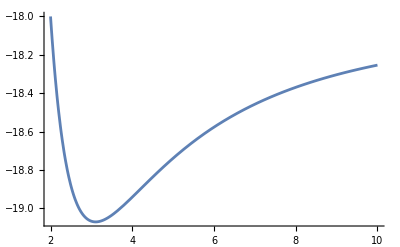

```mathematica
Plot[J2comp/.psirules/.ToM/.{Λ->0,λ->1,η->1,mass->1},{r[],2,10}]
```

## 3. Quadratic action

Now we want to find the action to quadratic order in metric perturbations. Scalar perturbations are ignored here as we are only focusing on the odd parity sector.

### Vanishing of some terms

Again, to reduce computation time we will make use of some simplifying arguments. The following combinations vanish in the case of odd perturbations so we set them to zero.

```mathematica
vanishing={h[LI[1],b_,-b_]->0,
h[LI[1],-b_,-c_]CD[b_][phi[]]CD[c_][phi[]]->0,
h[LI[1],c_,d_]CD[-d_][CD[-c_][phi[]]]->0,
h[LI[1],b_,c_]h[LI[1],d_,e_]CD[-b_][CD[-c_][phi[]]]CD[-d_][CD[-e_][phi[]]]->0,
CD[b_][phi[]]CD[c_][phi[]]CD[-d_][h[LI[1],-b_,d_]]CD[-e_][h[LI[1],-c_,e_]]->0,
CD[b_][phi[]]*CD[-c_][h[LI[1], -b_, c_]]->0}
```

{h | 1 | b̲ |  
  |   | b̲→0,h | 1 |   |  
  | b̲ | c̲ ∇^(b̲) ϕ ∇^(c̲) ϕ→0,h | 1 | c̲ | d̲
  |   |   ∇_(d̲) ∇_(c̲) ϕ→0,h | 1 | b̲ | c̲
  |   |   h | 1 | d̲ | e̲
  |   |   ∇_(b̲) ∇_(c̲) ϕ ∇_(d̲) ∇_(e̲) ϕ→0,∇^(b̲) ϕ ∇^(c̲) ϕ ∇_(d̲) h | 1 |   | d̲
  | b̲ |   ∇_(e̲) h | 1 |   | e̲
  | c̲ |  →0,∇^(b̲) ϕ ∇_(c̲) h | 1 |   | c̲
  | b̲ |  →0}

We demonstrate that they indeed vanish below

```mathematica
h[LI[1],b,-b]
%//ToBasis[SdS]//TraceBasisDummy;
%//ToValues//ToValues
h[LI[1],-b,-c]CD[b][phi[]]CD[c][phi[]]
%//ToBasis[SdS]//TraceBasisDummy;
%/.ScalarRules;
%//ToValues//ToValues
h[LI[1],c,d]CD[-d][CD[-c][phi[]]]
%//ToBasis[SdS]//TraceBasisDummy;
%/.ScalarRules;
%//ToValues//ToValues
h[LI[1],b,c]h[LI[1],d,e]CD[-b][CD[-c][phi[]]]CD[-d][CD[-e][phi[]]]
%//ToBasis[SdS]//TraceBasisDummy;
%/.ScalarRules;
%//ToValues//ToValues
CD[b][phi[]]CD[c][phi[]]CD[-d][h[LI[1],-b,d]]CD[-e][h[LI[1],-c,e]]
%//ToBasis[SdS]//TraceBasisDummy;
%/.ScalarRules;
%//ToValues//ToValues
CD[b][phi[]]*CD[-c][h[LI[1], -b, c]]
%//ToBasis[SdS]//TraceBasisDummy;
%/.ScalarRules;
%//ToValues//ToValues
```

h | 1 | b |  
  |   | b

0

h | 1 |   |  
  | b | c ∇^b ϕ ∇^c ϕ

0

h | 1 | c | d
  |   |   ∇_d ∇_c ϕ

0

h | 1 | b | c
  |   |   h | 1 | d | e
  |   |   ∇_b ∇_c ϕ ∇_d ∇_e ϕ

0

∇^b ϕ ∇^c ϕ ∇_d h | 1 |   | d
  | b |   ∇_e h | 1 |   | e
  | c |

0

∇^b ϕ ∇_c h | 1 |   | c
  | b |

0

### Covariant quadratic action

Now we find the quadratic action

```mathematica
L/.Xtoϕ
1/2 Perturbation[%,2]//ExpandPerturbation//NoScalar//Expand;
%/.{Perturbation[phi[]]->0,Perturbation[phi[]]^2->0,Perturbation[phi[],2]->0};
%/.onlyfirst/.RiccidS//Simplification;
ContractMetric[%,g]//Simplification;
%/.vanishing//Simplification;
%//Expand;
δL=%/.IBPrule1//Simplification
```

√-g (-2 Λ+R (M_Pl^2+(λ √(-(∇_b ϕ ∇^b ϕ)))/(√2))+√2 M_Pl^2 η √(-(∇_b ϕ ∇^b ϕ))+(λ ((∇^b ∇_b ϕ)^2-∇_c ∇_d ϕ ∇^c ∇^d ϕ))/(√2 √(-(∇_b ϕ ∇^b ϕ))))

-1/(8 M_Pl^2 (∇_b ϕ ∇^b ϕ)^2)√-g (√2 M_Pl^2 λ (-(∇_b ϕ ∇^b ϕ))^(5/2) ∇_b h | 1 |   |  
  | c | d ∇^b h | 1 | c | d
  |   |  +2 M_Pl^4 (∇_b ϕ ∇^b ϕ)^2 ∇_b h | 1 |   |  
  | c | d ∇^b h | 1 | c | d
  |   |  +4 √2 M_Pl^2 λ h | 1 |   | e
  | d |   (-(∇_b ϕ ∇^b ϕ))^(3/2) ∇_b h | 1 |   |  
  | c | e ∇^b ∇^d ϕ ∇^c ϕ+4 √2 M_Pl^2 λ h | 1 |   | e
  | c |   (-(∇_b ϕ ∇^b ϕ))^(3/2) ∇_b h | 1 |   |  
  | d | e ∇^b ∇^d ϕ ∇^c ϕ-4 √2 M_Pl^2 λ h | 1 |   | e
  | d |   (-(∇_b ϕ ∇^b ϕ))^(3/2) ∇^b ∇^d ϕ ∇_c h | 1 |   |  
  | b | e ∇^c ϕ-4 √2 M_Pl^2 λ h | 1 |   | e
  | b |   (-(∇_b ϕ ∇^b ϕ))^(3/2) ∇^b ∇^d ϕ ∇_c h | 1 |   |  
  | d | e ∇^c ϕ+4 √2 M_Pl^2 λ h | 1 |   | e
  | c |   (-(∇_b ϕ ∇^b ϕ))^(3/2) ∇^b ∇^d ϕ ∇^c ϕ ∇_d h | 1 |   |  
  | b | e-2 √2 M_Pl^2 λ (-(∇_b ϕ ∇^b ϕ))^(5/2) ∇^b h | 1 | c | d
  |   |   ∇_d h | 1 |   |  
  | c | b-4 M_Pl^4 (∇_b ϕ ∇^b ϕ)^2 ∇^b h | 1 | c | d
  |   |   ∇_d h | 1 |   |  
  | c | b+4 √2 M_Pl^2 λ h | 1 |   | e
  | b |   (-(∇_b ϕ ∇^b ϕ))^(3/2) ∇^b ∇^d ϕ ∇^c ϕ ∇_d h | 1 |   |  
  | c | e+4 √2 M_Pl^2 λ h | 1 | b | e
  |   |   (-(∇_b ϕ ∇^b ϕ))^(3/2) ∇_c h | 1 |   |  
  | b | e ∇^c ϕ ∇_d ∇^d ϕ+4 √2 M_Pl^4 η h | 1 |   | b
  | c |   h | 1 |   |  
  | d | b (-(∇_b ϕ ∇^b ϕ))^(3/2) ∇^c ϕ ∇^d ϕ+8 √2 λ Λ h | 1 |   | b
  | c |   h | 1 |   |  
  | d | b (-(∇_b ϕ ∇^b ϕ))^(3/2) ∇^c ϕ ∇^d ϕ+√2 M_Pl^2 λ (-(∇_b ϕ ∇^b ϕ))^(3/2) ∇_c h | 1 | b | e
  |   |   ∇^c ϕ ∇_d h | 1 |   |  
  | b | e ∇^d ϕ-4 √2 M_Pl^2 λ h | 1 | b | e
  |   |   (-(∇_b ϕ ∇^b ϕ))^(3/2) ∇^c ϕ ∇_d h | 1 |   |  
  | b | e ∇^d ∇_c ϕ-√2 M_Pl^2 λ h | 1 |   |  
  | b | e (-(∇_b ϕ ∇^b ϕ))^(3/2) (h | 1 | b | e
  |   |   (-∇_c ∇^c ϕ ∇_d ∇^d ϕ+∇_d ∇_c ϕ ∇^d ∇^c ϕ)-4 (h | 1 |   | e
  | c |   ∇_d ∇^b ϕ ∇^d ∇^c ϕ+h | 1 |   | e
  | d |   (-2 ∇^b ∇^d ϕ ∇_c ∇^c ϕ+∇^b ∇_c ϕ ∇^d ∇^c ϕ)))-8 √2 M_Pl^2 λ h | 1 |   | b
  | c |   (-(∇_b ϕ ∇^b ϕ))^(3/2) ∇^c ϕ ∇_d ∇^d ϕ ∇_e h | 1 |   | e
  | b |  +2 √2 M_Pl^2 λ (-(∇_b ϕ ∇^b ϕ))^(3/2) ∇^b h | 1 |   |  
  | c | d ∇^c ϕ ∇^d ϕ ∇_e h | 1 |   | e
  | b |  +4 √2 M_Pl^2 λ h | 1 |   | b
  | d |   (-(∇_b ϕ ∇^b ϕ))^(3/2) ∇^c ϕ ∇^d ∇_c ϕ ∇_e h | 1 |   | e
  | b |  +4 √2 M_Pl^2 λ h | 1 |   | e
  | d |   (-(∇_b ϕ ∇^b ϕ))^(3/2) ∇^b ∇^d ϕ ∇^c ϕ ∇_e h | 1 |   |  
  | c | b-8 √2 M_Pl^2 λ h | 1 | b | e
  |   |   (-(∇_b ϕ ∇^b ϕ))^(3/2) ∇^c ϕ ∇_d ∇^d ϕ ∇_e h | 1 |   |  
  | c | b+4 √2 M_Pl^2 λ h | 1 |   | e
  | b |   (-(∇_b ϕ ∇^b ϕ))^(3/2) ∇^b ∇^d ϕ ∇^c ϕ ∇_e h | 1 |   |  
  | c | d-4 √2 M_Pl^2 λ h | 1 |   | e
  | c |   (-(∇_b ϕ ∇^b ϕ))^(3/2) ∇^b ∇^d ϕ ∇^c ϕ ∇_e h | 1 |   |  
  | d | b+4 √2 M_Pl^2 λ h | 1 | b | e
  |   |   (-(∇_b ϕ ∇^b ϕ))^(3/2) ∇^c ϕ ∇^d ∇_c ϕ ∇_e h | 1 |   |  
  | d | b-2 √2 M_Pl^2 λ h | 1 |   | f
  | c |   h | 1 |   |  
  | d | f √(-(∇_b ϕ ∇^b ϕ)) ∇_b ∇^b ϕ ∇^c ϕ ∇^d ϕ ∇_e ∇^e ϕ+2 √2 M_Pl^2 λ (-(∇_b ϕ ∇^b ϕ))^(3/2) ∇_b h | 1 |   |  
  | d | e ∇^c ϕ ∇^d ϕ ∇^e h | 1 |   | b
  | c |  -4 √2 M_Pl^2 λ (-(∇_b ϕ ∇^b ϕ))^(3/2) ∇^c ϕ ∇_d h | 1 |   |  
  | b | e ∇^d ϕ ∇^e h | 1 |   | b
  | c |  +2 √2 M_Pl^2 λ (-(∇_b ϕ ∇^b ϕ))^(3/2) ∇^c ϕ ∇^d ϕ ∇_e h | 1 |   |  
  | d | b ∇^e h | 1 |   | b
  | c |  +4 √2 M_Pl^2 λ h | 1 |   |  
  | c | b h | 1 |   |  
  | d | e (-(∇_b ϕ ∇^b ϕ))^(3/2) ∇^d ∇^c ϕ ∇^e ∇^b ϕ+2 √2 M_Pl^2 λ h | 1 |   | f
  | c |   h | 1 |   |  
  | d | f √(-(∇_b ϕ ∇^b ϕ)) ∇^c ϕ ∇^d ϕ ∇_e ∇_b ϕ ∇^e ∇^b ϕ+2 √2 M_Pl^2 λ h | 1 |   |  
  | d | b √(-(∇_b ϕ ∇^b ϕ)) ∇^b ϕ ∇^c ϕ ∇^d ϕ ∇^e ∇_c ϕ ∇_f h | 1 |   | f
  | e |  +2 M_Pl^2 h | 1 |   |  
  | c | d (h | 1 | c | d
  |   |   (-2 Λ+√2 M_Pl^2 η √(-(∇_b ϕ ∇^b ϕ))) (∇_b ϕ ∇^b ϕ)^2+√2 λ √(-(∇_b ϕ ∇^b ϕ)) ((∇_b ϕ ∇^b ϕ) (-2 ∇^b ∇^d ϕ ∇^c ϕ ∇_e h | 1 |   | e
  | b |  +2 h | 1 |   |  
  | b | e ∇^d ∇^c ϕ ∇^e ∇^b ϕ)+∇^c ϕ ∇^d ϕ (h | 1 |   |  
  | b | f ∇_e ∇^f ϕ ∇^e ∇^b ϕ+∇^b ϕ (-∇_b h | 1 |   |  
  | e | f+∇_e h | 1 |   |  
  | b | f+∇_f h | 1 |   |  
  | b | e) ∇^f ∇^e ϕ+h | 1 |   |  
  | e | f (∇^e ∇^b ϕ ∇^f ∇_b ϕ-2 ∇_b ∇^b ϕ ∇^f ∇^e ϕ)))))

```mathematica
δL-η Coefficient[δL,η]-λ Coefficient[δL,λ]//Simplification
```

1/4 √-g (2 Λ h | 1 |   |  
  | c | d h | 1 | c | d
  |   |  +M_Pl^2 ∇^b h | 1 | c | d
  |   |   (-∇_b h | 1 |   |  
  | c | d+2 ∇_d h | 1 |   |  
  | c | b))

```mathematica
Coefficient[δL,η]//Simplification
```

(M_Pl^2 √-g (h | 1 |   |  
  | c | d h | 1 | c | d
  |   |   (∇_b ϕ ∇^b ϕ)-2 h | 1 |   | b
  | c |   h | 1 |   |  
  | d | b ∇^c ϕ ∇^d ϕ))/(2 √2 √(-(∇_b ϕ ∇^b ϕ)))

```mathematica
Coefficient[δL,λ]//Simplification
```

1/(4 √2 M_Pl^2 (-(∇_b ϕ ∇^b ϕ))^(3/2))√-g (-M_Pl^2 (∇_b ϕ ∇^b ϕ)^2 ∇_b h | 1 |   |  
  | c | d ∇^b h | 1 | c | d
  |   |  +4 M_Pl^2 h | 1 |   | e
  | d |   (∇_b ϕ ∇^b ϕ) ∇_b h | 1 |   |  
  | c | e ∇^b ∇^d ϕ ∇^c ϕ+4 M_Pl^2 h | 1 |   | e
  | c |   (∇_b ϕ ∇^b ϕ) ∇_b h | 1 |   |  
  | d | e ∇^b ∇^d ϕ ∇^c ϕ-4 M_Pl^2 h | 1 |   | e
  | d |   (∇_b ϕ ∇^b ϕ) ∇^b ∇^d ϕ ∇_c h | 1 |   |  
  | b | e ∇^c ϕ-4 M_Pl^2 h | 1 |   | e
  | b |   (∇_b ϕ ∇^b ϕ) ∇^b ∇^d ϕ ∇_c h | 1 |   |  
  | d | e ∇^c ϕ+4 M_Pl^2 h | 1 |   | e
  | c |   (∇_b ϕ ∇^b ϕ) ∇^b ∇^d ϕ ∇^c ϕ ∇_d h | 1 |   |  
  | b | e+2 M_Pl^2 (∇_b ϕ ∇^b ϕ)^2 ∇^b h | 1 | c | d
  |   |   ∇_d h | 1 |   |  
  | c | b+4 M_Pl^2 h | 1 |   | e
  | b |   (∇_b ϕ ∇^b ϕ) ∇^b ∇^d ϕ ∇^c ϕ ∇_d h | 1 |   |  
  | c | e+8 Λ h | 1 |   | b
  | c |   h | 1 |   |  
  | d | b (∇_b ϕ ∇^b ϕ) ∇^c ϕ ∇^d ϕ+M_Pl^2 (∇_b ϕ ∇^b ϕ) ∇_c h | 1 | b | e
  |   |   ∇^c ϕ ∇_d h | 1 |   |  
  | b | e ∇^d ϕ+4 M_Pl^2 h | 1 |   |  
  | c | d (∇_b ϕ ∇^b ϕ) ∇^b ∇^d ϕ ∇^c ϕ ∇_e h | 1 |   | e
  | b |  -8 M_Pl^2 h | 1 |   | b
  | c |   (∇_b ϕ ∇^b ϕ) ∇^c ϕ ∇_d ∇^d ϕ ∇_e h | 1 |   | e
  | b |  +2 M_Pl^2 (∇_b ϕ ∇^b ϕ) ∇^b h | 1 |   |  
  | c | d ∇^c ϕ ∇^d ϕ ∇_e h | 1 |   | e
  | b |  +4 M_Pl^2 h | 1 |   | b
  | d |   (∇_b ϕ ∇^b ϕ) ∇^c ϕ ∇^d ∇_c ϕ ∇_e h | 1 |   | e
  | b |  +4 M_Pl^2 h | 1 |   | e
  | d |   (∇_b ϕ ∇^b ϕ) ∇^b ∇^d ϕ ∇^c ϕ ∇_e h | 1 |   |  
  | c | b+4 M_Pl^2 h | 1 |   | e
  | b |   (∇_b ϕ ∇^b ϕ) ∇^b ∇^d ϕ ∇^c ϕ ∇_e h | 1 |   |  
  | c | d-4 M_Pl^2 h | 1 |   | e
  | c |   (∇_b ϕ ∇^b ϕ) ∇^b ∇^d ϕ ∇^c ϕ ∇_e h | 1 |   |  
  | d | b+4 M_Pl^2 h | 1 | b | e
  |   |   (∇_b ϕ ∇^b ϕ) ∇^c ϕ (∇_c h | 1 |   |  
  | b | e ∇_d ∇^d ϕ-∇_d h | 1 |   |  
  | b | e ∇^d ∇_c ϕ-2 ∇_d ∇^d ϕ ∇_e h | 1 |   |  
  | c | b+∇^d ∇_c ϕ ∇_e h | 1 |   |  
  | d | b)+2 M_Pl^2 h | 1 |   | f
  | c |   h | 1 |   |  
  | d | f ∇_b ∇^b ϕ ∇^c ϕ ∇^d ϕ ∇_e ∇^e ϕ+2 M_Pl^2 (∇_b ϕ ∇^b ϕ) ∇_b h | 1 |   |  
  | d | e ∇^c ϕ ∇^d ϕ ∇^e h | 1 |   | b
  | c |  -4 M_Pl^2 (∇_b ϕ ∇^b ϕ) ∇^c ϕ ∇_d h | 1 |   |  
  | b | e ∇^d ϕ ∇^e h | 1 |   | b
  | c |  +2 M_Pl^2 (∇_b ϕ ∇^b ϕ) ∇^c ϕ ∇^d ϕ ∇_e h | 1 |   |  
  | d | b ∇^e h | 1 |   | b
  | c |  +4 M_Pl^2 h | 1 |   |  
  | c | b h | 1 |   |  
  | d | e (∇_b ϕ ∇^b ϕ) ∇^d ∇^c ϕ ∇^e ∇^b ϕ-2 M_Pl^2 h | 1 |   | f
  | c |   h | 1 |   |  
  | d | f ∇^c ϕ ∇^d ϕ ∇_e ∇_b ϕ ∇^e ∇^b ϕ-2 M_Pl^2 h | 1 |   |  
  | b | f h | 1 |   |  
  | c | d ∇^c ϕ ∇^d ϕ ∇_e ∇^f ϕ ∇^e ∇^b ϕ+M_Pl^2 h | 1 |   |  
  | b | e (∇_b ϕ ∇^b ϕ) (4 h | 1 |   | e
  | c |   ∇_d ∇^b ϕ ∇^d ∇^c ϕ+4 h | 1 |   | e
  | d |   (-2 ∇^b ∇^d ϕ ∇_c ∇^c ϕ+∇^b ∇_c ϕ ∇^d ∇^c ϕ)+h | 1 | b | e
  |   |   (∇_c ∇^c ϕ ∇_d ∇^d ϕ-∇_d ∇_c ϕ ∇^d ∇^c ϕ)-4 h | 1 |   |  
  | c | d ∇^d ∇^c ϕ ∇^e ∇^b ϕ)-2 M_Pl^2 h | 1 |   |  
  | d | b ∇^b ϕ ∇^c ϕ ∇^d ϕ ∇^e ∇_c ϕ ∇_f h | 1 |   | f
  | e |  -2 M_Pl^2 h | 1 |   |  
  | c | d h | 1 |   |  
  | e | f ∇^c ϕ ∇^d ϕ ∇^e ∇^b ϕ ∇^f ∇_b ϕ+4 M_Pl^2 h | 1 |   |  
  | c | d h | 1 |   |  
  | e | f ∇_b ∇^b ϕ ∇^c ϕ ∇^d ϕ ∇^f ∇^e ϕ+2 M_Pl^2 h | 1 |   |  
  | c | d ∇_b h | 1 |   |  
  | e | f ∇^b ϕ ∇^c ϕ ∇^d ϕ ∇^f ∇^e ϕ-2 M_Pl^2 h | 1 |   |  
  | c | d ∇^b ϕ ∇^c ϕ ∇^d ϕ ∇_e h | 1 |   |  
  | b | f ∇^f ∇^e ϕ-2 M_Pl^2 h | 1 |   |  
  | c | d ∇^b ϕ ∇^c ϕ ∇^d ϕ ∇_f h | 1 |   |  
  | b | e ∇^f ∇^e ϕ)

### Quadratic action in components

Now we proceed to substitute the background into the quadratic action. This step can take a few minutes.

```mathematica
ToVal[expr_]:=(((((((expr/.ScalarRules)//ToBasis[SdS]//ToBasis[SdS]//ToBasis[SdS])//.contract)//TraceBasisDummy//TraceBasisDummy//TraceBasisDummy)//ToValues//ToValues//ToValues)(*//PowerExpand*)//Expand)/.PLrules//Simplify//Expand)/.PLrules//Simplify
```

```mathematica
(*this takes a few minutes to evaluate - any suggestions on reducing computation time are welcome*)
```

```mathematica
len4=Length[δL/.CDphirules1//Simplification//Expand];
TrBsDm[expr_]:=Sum[ToVal[expr[[i]]],{i,1,len4}]
δLcomp=TrBsDm[δL/.CDphirules1//Simplification//Expand]
```

We use the following rule to integrate by parts some terms.

```mathematica
ibpL2={h1T[]PD[{0,-SdS}][h0T[]]->-PD[{0,-SdS}][h1T[]]h0T[],XX_ h1T[]PD[{1,-SdS}][h1T[]]->-1/2 h1T[]^2 Hold[D [XX,r[]]],
XX_ h1T[]PD[{0,-SdS}][h1T[]]->-1/2 h1T[]^2 Hold[D [XX,t[]]],XX_ h0T[]PD[{1,-SdS}][h0T[]]->-1/2 h0T[]^2 Hold[D [XX,r[]]],
XX_ h0T[]PD[{0,-SdS}][h0T[]]->-1/2 h0T[]^2 Hold[D [XX,t[]]],
XX_ h0T[]PD[{1,-SdS}][h1T[]]->-XX PD[{1,-SdS}][h0T[]]h1T[]-Hold[D [XX,r[]]]h0T[]h1T[]}
applyIBP[x_]:=x/.ibpL2//ReleaseHold//Simplify
```

{OverTilde[h_1] ∂_t OverTilde[h_0]→-OverTilde[h_0] ∂_t OverTilde[h_1],OverTilde[h_1] XX_ ∂_r OverTilde[h_1]→-1/2 OverTilde[h_1]^2 Hold[∂_r XX],OverTilde[h_1] XX_ ∂_t OverTilde[h_1]→-1/2 OverTilde[h_1]^2 Hold[∂_t XX],OverTilde[h_0] XX_ ∂_r OverTilde[h_0]→-1/2 OverTilde[h_0]^2 Hold[∂_r XX],OverTilde[h_0] XX_ ∂_t OverTilde[h_0]→-1/2 OverTilde[h_0]^2 Hold[∂_t XX],OverTilde[h_0] XX_ ∂_r OverTilde[h_1]→-OverTilde[h_0] OverTilde[h_1] Hold[∂_r XX]-XX OverTilde[h_1] ∂_r OverTilde[h_0]}

And this is how the quadratic action looks like after the integration by parts.

```mathematica
(1+2l)*δLcomp/.ToT//Expand;
%//applyIBP;
((%/.{Sqrt[r[]^4*Sin[θ[]]^2]->r[]^2*Sin[θ[]],(Sqrt[r[]^4*Sin[θ[]]^2])^-1->(r[]^2*Sin[θ[]])^-1}//TrigExpand)/.{Csc[θ[]]->Cos[θ[]]Cot[θ[]]+Sin[θ[]]}//Expand)//.PLrules//Simplify;
ibpδL2=Collect[%,{(PD[{1,-SdS}][h0T[]])^2,(PD[{0,-SdS}][h1T[]])^2,h0T[]^2,h1T[]^2}]
```

-1/(4 M_Pl^2 B[r]^4 (∇ϕ∇ϕ[r])^2 r^2)l (1+l) OverTilde[h_0] ∂_t OverTilde[h_1] (-8 √2 M_Pl^2 q^2 λ B[r]^3 √(-∇ϕ∇ϕ[r]) ∇ϕ∇ϕ[r] r-8 M_Pl^2 B[r]^4 (2 M_Pl^2+√2 λ √(-∇ϕ∇ϕ[r])) (∇ϕ∇ϕ[r])^2 r+8 √2 M_Pl^2 λ B[r]^5 √(-∇ϕ∇ϕ[r]) ∇ϕ∇ϕ[r] r ψ'[r]^2)-1/(4 M_Pl^2 B[r]^4 (∇ϕ∇ϕ[r])^2 r^2)l (1+l) ∂_t OverTilde[h_1] ∂_r OverTilde[h_0] (4 √2 M_Pl^2 q^2 λ B[r]^3 √(-∇ϕ∇ϕ[r]) ∇ϕ∇ϕ[r] r^2+4 M_Pl^2 B[r]^4 (2 M_Pl^2+√2 λ √(-∇ϕ∇ϕ[r])) (∇ϕ∇ϕ[r])^2 r^2-4 √2 M_Pl^2 λ B[r]^5 √(-∇ϕ∇ϕ[r]) ∇ϕ∇ϕ[r] r^2 ψ'[r]^2)-1/(4 M_Pl^2 B[r]^4 (∇ϕ∇ϕ[r])^2 r^2)l (1+l) (∂_t OverTilde[h_1])^2 (-2 √2 M_Pl^2 q^2 λ B[r]^3 √(-∇ϕ∇ϕ[r]) ∇ϕ∇ϕ[r] r^2-2 M_Pl^2 B[r]^4 (2 M_Pl^2+√2 λ √(-∇ϕ∇ϕ[r])) (∇ϕ∇ϕ[r])^2 r^2+2 √2 M_Pl^2 λ B[r]^5 √(-∇ϕ∇ϕ[r]) ∇ϕ∇ϕ[r] r^2 ψ'[r]^2)-1/(4 M_Pl^2 B[r]^4 (∇ϕ∇ϕ[r])^2 r^2)l (1+l) (∂_r OverTilde[h_0])^2 (-2 √2 M_Pl^2 q^2 λ B[r]^3 √(-∇ϕ∇ϕ[r]) ∇ϕ∇ϕ[r] r^2-2 M_Pl^2 B[r]^4 (2 M_Pl^2+√2 λ √(-∇ϕ∇ϕ[r])) (∇ϕ∇ϕ[r])^2 r^2+2 √2 M_Pl^2 λ B[r]^5 √(-∇ϕ∇ϕ[r]) ∇ϕ∇ϕ[r] r^2 ψ'[r]^2)-1/(4 M_Pl^2 B[r]^4 (∇ϕ∇ϕ[r])^2 r^2)l (1+l) OverTilde[h_0] OverTilde[h_1] (-8 √2 M_Pl^2 q λ B[r]^4 (-∇ϕ∇ϕ[r])^(3/2) r^2 ∇∇ϕ'[r]-4 √2 M_Pl^2 q λ B[r]^4 ∇∇ϕ[r] √(-∇ϕ∇ϕ[r]) r^2 ∇ϕ∇ϕ'[r]+16 √2 M_Pl^2 q λ B[r]^5 √(-∇ϕ∇ϕ[r]) ∇ϕ∇ϕ[r] ψ'[r]+4 √2 M_Pl^2 q λ B[r]^4 (∇∇ϕ[r])^2 √(-∇ϕ∇ϕ[r]) r^2 ψ'[r]+8 √2 M_Pl^2 q λ B[r]^4 (-∇ϕ∇ϕ[r])^(3/2) r B'[r] ψ'[r]+2 √2 M_Pl^2 q^3 λ B[r]^2 √(-∇ϕ∇ϕ[r]) r^2 B'[r]^2 ψ'[r]+2 √2 M_Pl^2 q λ B[r]^4 √(-∇ϕ∇ϕ[r]) r^2 B'[r] ∇ϕ∇ϕ'[r] ψ'[r]-2 √2 M_Pl^2 q λ B[r]^4 √(-∇ϕ∇ϕ[r]) r^2 B'[r]^2 ψ'[r]^3-4 √2 q B[r]^4 (-∇ϕ∇ϕ[r])^(3/2) ψ'[r] ((-2+l+l^2) M_Pl^2 λ+2 M_Pl^4 η r^2+4 λ Λ r^2-M_Pl^2 λ r^2 B''[r])-16 √2 M_Pl^2 q λ B[r]^5 √(-∇ϕ∇ϕ[r]) ∇ϕ∇ϕ[r] r ψ''[r]+16 √2 M_Pl^2 q λ B[r]^4 (-∇ϕ∇ϕ[r])^(3/2) r^2 B'[r] ψ''[r]+4 √2 M_Pl^2 q λ B[r]^5 √(-∇ϕ∇ϕ[r]) r^2 ∇ϕ∇ϕ'[r] ψ''[r]-4 √2 M_Pl^2 q λ B[r]^5 √(-∇ϕ∇ϕ[r]) r^2 B'[r] ψ'[r]^2 ψ''[r]-4 √2 M_Pl^2 q λ B[r]^6 √(-∇ϕ∇ϕ[r]) ψ'[r] (2 ψ'[r]^2+r^2 ψ''[r]^2)-8 √2 M_Pl^2 q λ B[r]^5 √(-∇ϕ∇ϕ[r]) ∇ϕ∇ϕ[r] r^2 ψ^(3)[r])-1/(4 M_Pl^2 B[r]^4 (∇ϕ∇ϕ[r])^2 r^2)l (1+l) OverTilde[h_0]^2 (-4 √2 M_Pl^2 q^2 λ B[r]^3 √(-∇ϕ∇ϕ[r]) ∇ϕ∇ϕ[r]-2 √2 M_Pl^2 q^2 λ B[r]^2 (∇∇ϕ[r])^2 √(-∇ϕ∇ϕ[r]) r^2+2 √2 M_Pl^2 λ B[r]^3 (∇∇ϕ[r])^2 √(-∇ϕ∇ϕ[r]) ∇ϕ∇ϕ[r] r^2-√2 M_Pl^2 q^4 λ √(-∇ϕ∇ϕ[r]) r^2 B'[r]^2-2 M_Pl^2 B[r]^3 (∇ϕ∇ϕ[r])^2 (l (2 M_Pl^2+√2 λ √(-∇ϕ∇ϕ[r]))+l^2 (2 M_Pl^2+√2 λ √(-∇ϕ∇ϕ[r]))+2 (-2 Λ+√2 M_Pl^2 η √(-∇ϕ∇ϕ[r])) r^2-2 (2 M_Pl^2+√2 λ √(-∇ϕ∇ϕ[r])) r B'[r])+√2 M_Pl^2 q^2 λ B[r]^2 √(-∇ϕ∇ϕ[r]) r^2 B'[r] ∇ϕ∇ϕ'[r]+8 √2 M_Pl^2 λ B[r]^4 ∇∇ϕ[r] (-∇ϕ∇ϕ[r])^(3/2) r ψ'[r]-4 √2 M_Pl^2 λ B[r]^3 ∇∇ϕ[r] √(-∇ϕ∇ϕ[r]) ∇ϕ∇ϕ[r] r^2 B'[r] ψ'[r]+4 √2 M_Pl^2 λ B[r]^4 (-∇ϕ∇ϕ[r])^(3/2) r^2 ∇∇ϕ'[r] ψ'[r]+2 √2 M_Pl^2 λ B[r]^4 ∇∇ϕ[r] √(-∇ϕ∇ϕ[r]) r^2 ∇ϕ∇ϕ'[r] ψ'[r]-10 √2 M_Pl^2 λ B[r]^4 (-∇ϕ∇ϕ[r])^(3/2) r B'[r] ψ'[r]^2+√2 M_Pl^2 q^2 λ B[r]^2 √(-∇ϕ∇ϕ[r]) r^2 B'[r]^2 ψ'[r]^2+2 √2 M_Pl^2 λ B[r]^3 √(-∇ϕ∇ϕ[r]) ∇ϕ∇ϕ[r] r^2 B'[r]^2 ψ'[r]^2-2 √2 M_Pl^2 λ B[r]^5 √(-∇ϕ∇ϕ[r]) r ∇ϕ∇ϕ'[r] ψ'[r]^2-2 √2 M_Pl^2 λ B[r]^4 √(-∇ϕ∇ϕ[r]) r^2 B'[r] ∇ϕ∇ϕ'[r] ψ'[r]^2-4 √2 M_Pl^2 λ B[r]^4 (-∇ϕ∇ϕ[r])^(3/2) r^2 ψ'[r]^2 B''[r]-2 √2 q^2 B[r]^2 √(-∇ϕ∇ϕ[r]) ∇ϕ∇ϕ[r] (-2 M_Pl^2 λ+l M_Pl^2 λ+l^2 M_Pl^2 λ+2 M_Pl^4 η r^2+4 λ Λ r^2+M_Pl^2 λ r B'[r]+M_Pl^2 λ r^2 B''[r])+4 √2 M_Pl^2 λ B[r]^4 ∇∇ϕ[r] (-∇ϕ∇ϕ[r])^(3/2) r^2 ψ''[r]+12 √2 M_Pl^2 λ B[r]^5 √(-∇ϕ∇ϕ[r]) ∇ϕ∇ϕ[r] r ψ'[r] ψ''[r]-12 √2 M_Pl^2 λ B[r]^4 (-∇ϕ∇ϕ[r])^(3/2) r^2 B'[r] ψ'[r] ψ''[r]-2 √2 M_Pl^2 λ B[r]^5 √(-∇ϕ∇ϕ[r]) r^2 ∇ϕ∇ϕ'[r] ψ'[r] ψ''[r]+2 √2 M_Pl^2 λ B[r]^5 √(-∇ϕ∇ϕ[r]) ∇ϕ∇ϕ[r] r^2 ψ''[r]^2+2 √2 M_Pl^2 q^2 λ B[r]^3 √(-∇ϕ∇ϕ[r]) r (∇ϕ∇ϕ'[r]+r B'[r] ψ'[r] ψ''[r])+2 √2 M_Pl^2 q^2 λ B[r]^4 √(-∇ϕ∇ϕ[r]) (2 ψ'[r]^2+r^2 ψ''[r]^2)+4 √2 M_Pl^2 λ B[r]^5 √(-∇ϕ∇ϕ[r]) ∇ϕ∇ϕ[r] r^2 ψ'[r] ψ^(3)[r])-1/(4 M_Pl^2 B[r]^4 (∇ϕ∇ϕ[r])^2 r^2)l (1+l) OverTilde[h_1]^2 (-4 M_Pl^2 B[r]^6 (2 M_Pl^2+√2 λ √(-∇ϕ∇ϕ[r])) (∇ϕ∇ϕ[r])^2-2 √2 M_Pl^2 λ B[r]^5 (∇∇ϕ[r])^2 √(-∇ϕ∇ϕ[r]) ∇ϕ∇ϕ[r] r^2+2 √2 M_Pl^2 q^2 λ B[r]^4 (-∇ϕ∇ϕ[r])^(3/2) r B'[r]+2 M_Pl^2 B[r]^5 (∇ϕ∇ϕ[r])^2 (l (2 M_Pl^2+√2 λ √(-∇ϕ∇ϕ[r]))+l^2 (2 M_Pl^2+√2 λ √(-∇ϕ∇ϕ[r]))+2 (-2 Λ+√2 M_Pl^2 η √(-∇ϕ∇ϕ[r])) r^2-2 (2 M_Pl^2+√2 λ √(-∇ϕ∇ϕ[r])) r B'[r])+4 √2 M_Pl^2 λ B[r]^5 ∇∇ϕ[r] √(-∇ϕ∇ϕ[r]) ∇ϕ∇ϕ[r] r^2 B'[r] ψ'[r]+2 √2 M_Pl^2 λ B[r]^6 ∇∇ϕ[r] √(-∇ϕ∇ϕ[r]) r^2 ∇ϕ∇ϕ'[r] ψ'[r]-2 √2 M_Pl^2 λ B[r]^6 (∇∇ϕ[r])^2 √(-∇ϕ∇ϕ[r]) r^2 ψ'[r]^2-√2 M_Pl^2 q^2 λ B[r]^4 √(-∇ϕ∇ϕ[r]) r^2 B'[r]^2 ψ'[r]^2-2 √2 M_Pl^2 λ B[r]^5 √(-∇ϕ∇ϕ[r]) ∇ϕ∇ϕ[r] r^2 B'[r]^2 ψ'[r]^2-√2 M_Pl^2 λ B[r]^6 √(-∇ϕ∇ϕ[r]) r^2 B'[r] ∇ϕ∇ϕ'[r] ψ'[r]^2+√2 M_Pl^2 λ B[r]^6 √(-∇ϕ∇ϕ[r]) r^2 B'[r]^2 ψ'[r]^4+2 √2 M_Pl^2 λ B[r]^8 √(-∇ϕ∇ϕ[r]) ψ'[r]^2 (2 ψ'[r]^2+r^2 ψ''[r]^2)+2 √2 B[r]^6 (-∇ϕ∇ϕ[r])^(3/2) (M_Pl^2 λ r ∇ϕ∇ϕ'[r]-2 M_Pl^2 λ ∇∇ϕ[r] r (2 ψ'[r]+r ψ''[r])+ψ'[r] (2 M_Pl^2 λ r^2 ∇∇ϕ'[r]+ψ'[r] (-2 M_Pl^2 λ+l M_Pl^2 λ+l^2 M_Pl^2 λ+2 M_Pl^4 η r^2+4 λ Λ r^2-M_Pl^2 λ r B'[r]-M_Pl^2 λ r^2 B''[r])-2 M_Pl^2 λ r^2 B'[r] ψ''[r]))-2 √2 M_Pl^2 λ B[r]^7 √(-∇ϕ∇ϕ[r]) (r^2 ψ'[r] (∇ϕ∇ϕ'[r]-B'[r] ψ'[r]^2) ψ''[r]+∇ϕ∇ϕ[r] (6 ψ'[r]^2+r^2 ψ''[r]^2-2 r ψ'[r] (ψ''[r]+r ψ^(3)[r]))))

However, we can simplify this term by term in the following way.

```mathematica
ibpδL22=(Coefficient[ibpδL2,h0T[]*PD[{0,-SdS}][h1T[]]]/.CDphirules2/.psirules/.ToM//Simplify)h0T[]*PD[{0,-SdS}][h1T[]]+(Coefficient[ibpδL2,(PD[{0,-SdS}][h1T[]])^2]/.CDphirules2/.psirules/.ToM//Simplify)(PD[{0,-SdS}][h1T[]])^2+(Coefficient[ibpδL2,(PD[{1,-SdS}][h0T[]])^2]/.CDphirules2/.psirules/.ToM//Simplify)(PD[{1,-SdS}][h0T[]])^2+(Coefficient[ibpδL2,PD[{0,-SdS}][h1T[]]*PD[{1,-SdS}][h0T[]]]/.CDphirules2/.psirules/.ToM//Simplify)PD[{0,-SdS}][h1T[]]*PD[{1,-SdS}][h0T[]]+(Coefficient[ibpδL2,h0T[]h1T[]]/.CDphirules2/.psirules/.ToM//Simplify)h0T[]h1T[]+(Coefficient[ibpδL2,(h0T[])^2 ]/.CDphirules2/.psirules/.ToM//Simplify)(h0T[])^2 +(Coefficient[ibpδL2,(h1T[])^2]/.CDphirules2/.psirules/.ToM//Simplify)(h1T[])^2
```

-(√6 l (1+l) (-2+l+l^2) OverTilde[h_0] OverTilde[h_1] √((q^2 λ)/(λ+M_Pl^2 η r^2)) (6 M λ+(3 M_Pl^4 η+λ Λ) r^3))/(r^2 (6 M-3 M_Pl^2 r+Λ r^3) √((6 M λ+3 M_Pl^4 η r^3+λ Λ r^3)/(M_Pl^2 λ r+M_Pl^4 η r^3)))+(l (1+l) (-2+l+l^2) OverTilde[h_1]^2 (12 M+2 Λ r^3-3 √2 λ r √((q^2 λ)/(λ+M_Pl^2 η r^2))-3 M_Pl^2 r (2+√2 η r^2 √((q^2 λ)/(λ+M_Pl^2 η r^2)))))/(6 r^3)-1/(2 r^2 (6 M-3 M_Pl^2 r+Λ r^3)^2)l (1+l) M_Pl^2 OverTilde[h_0]^2 (-144 M^2+6 M r (6 (2+l+l^2) M_Pl^2-8 Λ r^2+3 √2 (-2+l+l^2) λ √((q^2 λ)/(λ+M_Pl^2 η r^2)))+r^2 (-2 r^2 (-6 M_Pl^2 Λ+9 √2 M_Pl^4 η √((q^2 λ)/(λ+M_Pl^2 η r^2))+Λ (2 Λ r^2+3 √2 λ √((q^2 λ)/(λ+M_Pl^2 η r^2))))+3 l (2 M_Pl^2 Λ r^2+√2 λ Λ r^2 √((q^2 λ)/(λ+M_Pl^2 η r^2))+3 M_Pl^4 (-2+√2 η r^2 √((q^2 λ)/(λ+M_Pl^2 η r^2))))+3 l^2 (2 M_Pl^2 Λ r^2+√2 λ Λ r^2 √((q^2 λ)/(λ+M_Pl^2 η r^2))+3 M_Pl^4 (-2+√2 η r^2 √((q^2 λ)/(λ+M_Pl^2 η r^2))))))+(4 l (1+l) M_Pl^2 OverTilde[h_0] ∂_t OverTilde[h_1])/r+l (1+l) M_Pl^2 (∂_t OverTilde[h_1])^2-2 l (1+l) M_Pl^2 ∂_t OverTilde[h_1] ∂_r OverTilde[h_0]+l (1+l) M_Pl^2 (∂_r OverTilde[h_0])^2

And we check that the expressions for the quadratic action before and after the simplification are equivalent.

```mathematica
ibpδL2-ibpδL22==0/.CDphirules2/.psirules/.ToM//Simplify
```

True

Finally, we want to check whether we can write our quadratic action in the form described in https://arxiv.org/pdf/1610.00432.pdf, which is given by

```mathematica
DefScalarFunction[a1,PrintAs->"a_1"];
DefScalarFunction[a2,PrintAs->"a_2"];
DefScalarFunction[a3,PrintAs->"a_3"];
DefScalarFunction[a4,PrintAs->"a_4"];
δL2lit=a1[r[]]*h0T[]^2+a2[r[]]*h1T[]^2+a3[r[]]((PD[{0,-SdS}][h1T[]])^2+(PD[{1,-SdS}][h0T[]])^2-2PD[{0,-SdS}][h1T[]]PD[{1,-SdS}][h0T[]]+4/r[] PD[{0,-SdS}][h1T[]]h0T[])+a4[r[]]h0T[]h1T[]
```

a_1[r] OverTilde[h_0]^2+a_4[r] OverTilde[h_0] OverTilde[h_1]+a_2[r] OverTilde[h_1]^2+a_3[r] ((4 OverTilde[h_0] ∂_t OverTilde[h_1])/r+(∂_t OverTilde[h_1])^2-2 ∂_t OverTilde[h_1] ∂_r OverTilde[h_0]+(∂_r OverTilde[h_0])^2)

We can now find what the expressions for the a-coefficients in our action look like

```mathematica
(*the following are the corresponding coefficients we get in our calculation*)
ToaCoef={a1[r[]]->Coefficient[ibpδL22,(h0T[])^2],
a2[r[]]->Coefficient[ibpδL22,(h1T[])^2],
a3[r[]]->Coefficient[ibpδL22,(PD[{0,-SdS}][h1T[]])^2],
a4[r[]]->Coefficient[ibpδL22,h0T[]h1T[]]}//Simplify
```

{a_1[r]→-1/(2 r^2 (6 M-3 M_Pl^2 r+Λ r^3)^2)l (1+l) M_Pl^2 (-144 M^2+6 M r (6 (2+l+l^2) M_Pl^2-8 Λ r^2+3 √2 (-2+l+l^2) λ √((q^2 λ)/(λ+M_Pl^2 η r^2)))+r^2 (-2 r^2 (-6 M_Pl^2 Λ+9 √2 M_Pl^4 η √((q^2 λ)/(λ+M_Pl^2 η r^2))+Λ (2 Λ r^2+3 √2 λ √((q^2 λ)/(λ+M_Pl^2 η r^2))))+3 l (2 M_Pl^2 Λ r^2+√2 λ Λ r^2 √((q^2 λ)/(λ+M_Pl^2 η r^2))+3 M_Pl^4 (-2+√2 η r^2 √((q^2 λ)/(λ+M_Pl^2 η r^2))))+3 l^2 (2 M_Pl^2 Λ r^2+√2 λ Λ r^2 √((q^2 λ)/(λ+M_Pl^2 η r^2))+3 M_Pl^4 (-2+√2 η r^2 √((q^2 λ)/(λ+M_Pl^2 η r^2)))))),a_2[r]→(l (1+l) (-2+l+l^2) (12 M+2 Λ r^3-3 √2 λ r √((q^2 λ)/(λ+M_Pl^2 η r^2))-3 M_Pl^2 r (2+√2 η r^2 √((q^2 λ)/(λ+M_Pl^2 η r^2)))))/(6 r^3),a_3[r]→l (1+l) M_Pl^2,a_4[r]→-(√6 l (1+l) (-2+l+l^2) √((q^2 λ)/(λ+M_Pl^2 η r^2)) (6 M λ+(3 M_Pl^4 η+λ Λ) r^3))/(r^2 (6 M-3 M_Pl^2 r+Λ r^3) √((6 M λ+3 M_Pl^4 η r^3+λ Λ r^3)/(M_Pl^2 λ r+M_Pl^4 η r^3)))}

### Comparison to literature expression

We will now check whether these can be written in the same form as in https://arxiv.org/pdf/1610.00432.pdf, which are given in terms of the functions  ℱ, 𝒢, ℋ, 𝒥

```mathematica
DefScalarFunction[F,PrintAs->"ℱ"];
DefScalarFunction[G,PrintAs->"𝒢"];
DefScalarFunction[H,PrintAs->"ℋ"];
DefScalarFunction[J,PrintAs->"𝒥"];

(*we need to re-cast the format of the following derivative so it can actually be evaluated*)
Toa={a1[r[]]->((l(l+1))/(r[]^2))(Hold[D[r[]H[r[]],r[]]]+(((l-1)(l+2))/(2B[r[]]))F[r[]])//Simplify,
a2[r[]]->-(l(l+1)(l-1)(l+2)B[r[]]G[r[]])/(2 r[]^2)(*//PowerExpand*)//Simplify,
a3[r[]]->((l(l+1))/2)H[r[]],
a4[r[]]->(l(l+1)(l-1)(l+2)J[r[]])/(r[]^2)}
ToFGHJ={F[r[]]->2(G4[phi[],X[]]-q^2/B[r[]] G4X[phi[],X[]]),
G[r[]]->2(G4[phi[],X[]]+(q^2/B[r[]]-2X[])G4X[phi[],X[]]),
H[r[]]->2(G4[phi[],X[]]-2X[]G4X[phi[],X[]]),
J[r[]]->2 q Derivative[1][psi][r[]]G4X[phi[],X[]]}

Todera={Derivative[1][a1][r[]]->D[a1[r[]]/.Toa(*/.ToFGHJ/.cuscuton/.Xtoϕ/.CDphirules1/.CDphirules2/.ToM*)//ReleaseHold,r[]],
Derivative[2][a1][r[]]->D [D[a1[r[]]/.Toa//ReleaseHold,r[]],r[]],
Derivative[1][a2][r[]]->D[a2[r[]]/.Toa//ReleaseHold,r[]],
Derivative[2][a2][r[]]->D [D[a2[r[]]/.Toa//ReleaseHold,r[]],r[]],
Derivative[1][a3][r[]]->D[a3[r[]]/.Toa//ReleaseHold,r[]],
Derivative[2][a3][r[]]->D [D[a3[r[]]/.Toa//ReleaseHold,r[]],r[]],
Derivative[1][a4][r[]]->D[a4[r[]]/.Toa//ReleaseHold,r[]],
Derivative[2][a4][r[]]->D [D[a4[r[]]/.Toa//ReleaseHold,r[]],r[]]}//Simplify

ToderFGHJ={Derivative[1][F][r[]]->D[F[r[]]/.ToFGHJ/.ncXtheory/.Xtoϕ/.CDphirules1/.CDphirules2(*//PowerExpand*),r[]],
Derivative[1][G][r[]]->D[G[r[]]/.ToFGHJ/.ncXtheory/.Xtoϕ/.CDphirules1/.CDphirules2(*//PowerExpand*),r[]],
Derivative[1][H][r[]]->D[H[r[]]/.ToFGHJ/.ncXtheory/.Xtoϕ/.CDphirules1/.CDphirules2(*//PowerExpand*),r[]],
Derivative[1][J][r[]]->D[J[r[]]/.ToFGHJ/.ncXtheory/.Xtoϕ/.CDphirules1/.CDphirules2(*//PowerExpand*),r[]],Derivative[2][F][r[]]->D[D[F[r[]]/.ToFGHJ/.ncXtheory/.Xtoϕ/.CDphirules1/.CDphirules2(*//PowerExpand*),r[]],r[]],
Derivative[2][G][r[]]->D[D[G[r[]]/.ToFGHJ/.ncXtheory/.Xtoϕ/.CDphirules1/.CDphirules2(*//PowerExpand*),r[]],r[]],
Derivative[2][H][r[]]->D[D[H[r[]]/.ToFGHJ/.ncXtheory/.Xtoϕ/.CDphirules1/.CDphirules2(*//PowerExpand*),r[]],r[]],
Derivative[2][J][r[]]->D[D[J[r[]]/.ToFGHJ/.ncXtheory/.Xtoϕ/.CDphirules1/.CDphirules2(*//PowerExpand*),r[]],r[]]};
```

{a_1[r]→(l (1+l) (((-2+l+l^2) ℱ[r])/(2 B[r])+Hold[∂_r (r ℋ[r])]))/r^2,a_2[r]→-((-1+l) l (1+l) (2+l) B[r] 𝒢[r])/(2 r^2),a_3[r]→1/2 l (1+l) ℋ[r],a_4[r]→((-1+l) l (1+l) (2+l) 𝒥[r])/r^2}

{ℱ[r]→2 (G_4[ϕ,X]-(q^2 G_(4  X)[ϕ,X])/B[r]),𝒢[r]→2 (G_4[ϕ,X]+G_(4  X)[ϕ,X] (q^2/B[r]-2 X)),ℋ[r]→2 (G_4[ϕ,X]-2 G_(4  X)[ϕ,X] X),𝒥[r]→2 q G_(4  X)[ϕ,X] ψ'[r]}

{a_1'[r]→(l (1+l) (-((-2+l+l^2) ℱ[r] r B'[r])-(-2+l+l^2) B[r] (2 ℱ[r]-r ℱ'[r])+B[r]^2 (-4 ℋ[r]+2 r^2 ℋ''[r])))/(2 B[r]^2 r^3),a_1''[r]→1/(2 B[r]^3 r^4)l (1+l) (2 (-2+l+l^2) ℱ[r] r^2 B'[r]^2-(-2+l+l^2) B[r] r (2 r B'[r] ℱ'[r]+ℱ[r] (-4 B'[r]+r B''[r]))+(-2+l+l^2) B[r]^2 (6 ℱ[r]+r (-4 ℱ'[r]+r ℱ''[r]))+2 B[r]^3 (6 ℋ[r]+r (-2 ℋ'[r]+r (-ℋ''[r]+r ℋ^(3)[r])))),a_2'[r]→-(l (-2-l+2 l^2+l^3) (𝒢[r] r B'[r]+B[r] (-2 𝒢[r]+r 𝒢'[r])))/(2 r^3),a_2''[r]→-((-1+l) l (1+l) (2+l) (r (2 r B'[r] 𝒢'[r]+𝒢[r] (-4 B'[r]+r B''[r]))+B[r] (6 𝒢[r]+r (-4 𝒢'[r]+r 𝒢''[r]))))/(2 r^4),a_3'[r]→1/2 l (1+l) ℋ'[r],a_3''[r]→1/2 l (1+l) ℋ''[r],a_4'[r]→((-1+l) l (1+l) (2+l) (-2 𝒥[r]+r 𝒥'[r]))/r^3,a_4''[r]→((-1+l) l (1+l) (2+l) (6 𝒥[r]+r (-4 𝒥'[r]+r 𝒥''[r])))/r^4}

```mathematica
(*a1*)
a1[r[]]/.Toa/.ToFGHJ/.ncXtheory/.Xtoϕ/.CDphirules1/.CDphirules2/.ToM//ReleaseHold//Simplify;
a1[r[]]/.ToaCoef/.{Sqrt[r[]^4*Sin[θ[]]^2]->r[]^2*Sin[θ[]]}/.PLrules//Simplify;
%%-%==0(*//PowerExpand*)//Simplify
(*a2*)
a2[r[]]/.Toa/.ToFGHJ/.ncXtheory/.Xtoϕ/.CDphirules1/.CDphirules2/.ToM//Simplify;
a2[r[]]/.ToaCoef/.{Sqrt[r[]^4*Sin[θ[]]^2]->r[]^2*Sin[θ[]]}/.PLrules//Simplify;
%%-%==0(*//PowerExpand*)//Simplify
(*a3*)
a3[r[]]/.Toa/.ToFGHJ/.ncXtheory/.Xtoϕ/.CDphirules1/.CDphirules2/.ToM//Simplify;
a3[r[]]/.ToaCoef/.{Sqrt[r[]^4*Sin[θ[]]^2]->r[]^2*Sin[θ[]]}/.PLrules//Simplify;
%%-%==0(*//PowerExpand*)//Simplify
(*a4*)
a4[r[]]/.Toa/.ToFGHJ/.ncXtheory/.Xtoϕ/.CDphirules1/.CDphirules2/.psirules/.ToM//Simplify;
a4[r[]]/.ToaCoef/.{Sqrt[r[]^4*Sin[θ[]]^2]->r[]^2*Sin[θ[]]}/.PLrules//Simplify;
%%-%==0(*//PowerExpand*)//Simplify
```

True

True

True

«1 more identical outputs»

Hence, we see that all a-coefficients can be written in the same form, and thus we confirm that our quadratic action can be written in this form.

```mathematica
(ibpδL22-δL2lit)==0/.ToaCoef/.ToFGHJ/.ncXtheory/.Xtoϕ/.CDphirules1/.CDphirules2/.psirules/.ToM//ReleaseHold//Simplify(*//PowerExpand*)
```

True

## 4. One-variable action

Here we rewrite the quadratic action for odd perturbations in terms of the Regge-Wheeler variable.

```mathematica
DefTensor[chiT[],Md,PrintAs->"χ̃"];
DefScalarFunction[chi,PrintAs->"χ"];
chiToT={chi[t[],r[]]->chiT[],Derivative[0,1][chi][t[],r[]]->TraceBasisDummy[Scalar[rvec[b]PD[-b][chiT[]]]//NoScalar//ToBasis[SdS]]//ToValues,
Derivative[1,0][chi][t[],r[]]->TraceBasisDummy[Scalar[tvec[b]PD[-b][chiT[]]]//NoScalar//ToBasis[SdS]]//ToValues,
Derivative[0,2][chi][t[],r[]]->TraceBasisDummy[Scalar[rvec[c]PD[-c][TraceBasisDummy[Scalar[rvec[b]PD[-b][chiT[]]]//NoScalar//ToBasis[SdS]]//ToValues]]//NoScalar//ToBasis[SdS]]//ToValues,
Derivative[2,0][chi][t[],r[]]->TraceBasisDummy[Scalar[tvec[c]PD[-c][TraceBasisDummy[Scalar[tvec[b]PD[-b][chiT[]]]//NoScalar//ToBasis[SdS]]//ToValues]]//NoScalar//ToBasis[SdS]]//ToValues,
Derivative[1,1][chi][t[],r[]]->TraceBasisDummy[Scalar[tvec[c]PD[-c][TraceBasisDummy[Scalar[rvec[b]PD[-b][chiT[]]]//NoScalar//ToBasis[SdS]]]//ToValues]//NoScalar//ToBasis[SdS]]//ToValues}
```

{χ[t,r]→χ̃,χ^(0,1)[t,r]→∂_r χ̃,χ^(1,0)[t,r]→∂_t χ̃,χ^(0,2)[t,r]→∂_r ∂_r χ̃,χ^(2,0)[t,r]→∂_t ∂_t χ̃,χ^(1,1)[t,r]→∂_t ∂_r χ̃}

```mathematica
δL2litchi=(a1[r[]]-(2D[r[] a3[r[]],r[]])/r[]^2)h0T[]^2+a2[r[]]*h1T[]^2+a3[r[]](-chi[t[],r[]]^2+2chi[t[],r[]](PD[{0,-SdS}][h1T[]]-PD[{1,-SdS}][h0T[]]+2/r[] h0T[]))+a4[r[]]h0T[]h1T[];
%/.chiToT
VarD[chiT[],CD][%]==0
solchi=Solve[%,chiT[]][[1]]//Simplify
```

a_4[r] OverTilde[h_0] OverTilde[h_1]+a_2[r] OverTilde[h_1]^2+a_3[r] (-(χ̃)^2+2 χ̃ ((2 OverTilde[h_0])/r+∂_t OverTilde[h_1]-∂_r OverTilde[h_0]))+OverTilde[h_0]^2 (a_1[r]-(2 (a_3[r]+r a_3'[r]))/r^2)

-2 a_3[r] χ̃+(4 a_3[r] OverTilde[h_0])/r+2 a_3[r] ∂_t OverTilde[h_1]-2 a_3[r] ∂_r OverTilde[h_0]==0

{χ̃→(2 OverTilde[h_0])/r+∂_t OverTilde[h_1]-∂_r OverTilde[h_0]}

```mathematica
VarD[h0T[],CD][δL2litchi]==0//Expand
h0toh1chi=Solve[%,h0T[]]//Simplify
VarD[h1T[],CD][δL2litchi]==0/.h0toh1chi
h1tochi=(Solve[%,h1T[]]//Simplify)[[1]]
h0tochi=(h0toh1chi/.h1tochi//Simplify)[[1]]
```

2 a_1[r] OverTilde[h_0]+a_4[r] OverTilde[h_1]-(4 a_3[r] OverTilde[h_0])/r^2+(4 a_3[r] χ[t,r])/r+2 χ[t,r] a_3'[r]-(4 OverTilde[h_0] a_3'[r])/r+2 a_3[r] χ^(0,1)[t,r]==0

{{OverTilde[h_0]→(r (4 a_3[r] χ[t,r]+a_4[r] OverTilde[h_1] r+2 χ[t,r] r a_3'[r]+2 a_3[r] r χ^(0,1)[t,r]))/(4 a_3[r]-2 a_1[r] r^2+4 r a_3'[r])}}

{2 a_2[r] OverTilde[h_1]+(a_4[r] r (4 a_3[r] χ[t,r]+a_4[r] OverTilde[h_1] r+2 χ[t,r] r a_3'[r]+2 a_3[r] r χ^(0,1)[t,r]))/(4 a_3[r]-2 a_1[r] r^2+4 r a_3'[r])-2 a_3[r] χ^(1,0)[t,r]==0}

{OverTilde[h_1]→-((2 (a_4[r] χ[t,r] r^2 a_3'[r]-4 a_3[r]^2 χ^(1,0)[t,r]+a_3[r] r (a_4[r] (2 χ[t,r]+r χ^(0,1)[t,r])+2 (a_1[r] r-2 a_3'[r]) χ^(1,0)[t,r])))/(a_4[r]^2 r^2+a_2[r] (8 a_3[r]-4 a_1[r] r^2+8 r a_3'[r])))}

{OverTilde[h_0]→(2 r (2 a_2[r] (χ[t,r] r a_3'[r]+a_3[r] (2 χ[t,r]+r χ^(0,1)[t,r]))+a_3[r] a_4[r] r χ^(1,0)[t,r]))/(a_4[r]^2 r^2+a_2[r] (8 a_3[r]-4 a_1[r] r^2+8 r a_3'[r]))}

```mathematica
h0h1tochilit={h0T[]->-(1/(4a2[r[]](r[]^2 a1[r[]]-2D[r[]a3[r[]],r[]])-r[]^2 a4[r[]]^2))(2r[](2a2[r[]](r[]D[chi[t[],r[]]a3[r[]],r[]]+2chi[t[],r[]]a3[r[]])+r[]D[chi[t[],r[]],t[]]a3[r[]]a4[r[]])),
h1T[]->(1/(4a2[r[]](r[]^2 a1[r[]]-2D[r[]a3[r[]],r[]])-r[]^2 a4[r[]]^2))(4a3[r[]]D[chi[t[],r[]],t[]](r[]^2 a1[r[]]-2D[r[]a3[r[]],r[]])+2r[]a4[r[]](r[]D[chi[t[],r[]]a3[r[]],r[]]+2a3[r[]]chi[t[],r[]]))}
```

{OverTilde[h_0]→-(2 r (2 a_2[r] (2 a_3[r] χ[t,r]+r (χ[t,r] a_3'[r]+a_3[r] χ^(0,1)[t,r]))+a_3[r] a_4[r] r χ^(1,0)[t,r]))/(-a_4[r]^2 r^2+4 a_2[r] (a_1[r] r^2-2 (a_3[r]+r a_3'[r]))),OverTilde[h_1]→(2 a_4[r] r (2 a_3[r] χ[t,r]+r (χ[t,r] a_3'[r]+a_3[r] χ^(0,1)[t,r]))+4 a_3[r] (a_1[r] r^2-2 (a_3[r]+r a_3'[r])) χ^(1,0)[t,r])/(-a_4[r]^2 r^2+4 a_2[r] (a_1[r] r^2-2 (a_3[r]+r a_3'[r])))}

```mathematica
h0h1tochilit[[1]][[2]]-h0tochi[[1]][[2]]==0//Simplify
h0h1tochilit[[2]][[2]]-h1tochi[[1]][[2]]==0//Simplify
```

True

True

```mathematica
ibpL2chi={chiT[]*PD[{0,-SdS}][PD[{0,-SdS}][chiT[]]]->-(PD[{0,-SdS}][chiT[]])^2 ,
XX_ chiT[]*PD[{1,-SdS}][PD[{1,-SdS}][chiT[]]]->-Hold[D [XX,r[]]]chiT[]*PD[{1,-SdS}][chiT[]]-XX(PD[{1,-SdS}][chiT[]])^2 ,
XX_ chiT[]*PD[{0,-SdS}][PD[{1,-SdS}][chiT[]]]->-Hold[D [XX,t[]]]chiT[]*PD[{1,-SdS}][chiT[]]-XX PD[{0,-SdS}][chiT[]]PD[{1,-SdS}][chiT[]] ,
XX_ chiT[]*PD[{1,-SdS}][chiT[]]->-1/2 chiT[]^2 Hold[D [XX,r[]]],
XX_ chiT[]*PD[{0,-SdS}][chiT[]]->-1/2 chiT[]^2 Hold[D [XX,t[]]]}
applyIBPchi[x_]:=(x//.ibpL2chi)//ReleaseHold//ReleaseHold//Simplify
```

{χ̃ ∂_t ∂_t χ̃→-(∂_t χ̃)^2,χ̃ XX_ ∂_r ∂_r χ̃→-χ̃ Hold[∂_r XX] ∂_r χ̃-XX (∂_r χ̃)^2,χ̃ XX_ ∂_t ∂_r χ̃→-χ̃ Hold[∂_t XX] ∂_r χ̃-XX ∂_t χ̃ ∂_r χ̃,χ̃ XX_ ∂_r χ̃→-1/2 (χ̃)^2 Hold[∂_r XX],χ̃ XX_ ∂_t χ̃→-1/2 (χ̃)^2 Hold[∂_t XX]}

```mathematica
δL2litchi/.h0tochi/.h1tochi/.chiToT//Expand;
%//applyIBPchi;
%//Simplify;
δL2litchi2=Collect[%,{(PD[{1,-SdS}][chiT[]])^2,(PD[{0,-SdS}][chiT[]])^2,chiT[]^2}]
```

-(a_3[r] (∂_r χ̃)^2 (-32 a_2[r]^2 a_3[r]^2 r^2+16 a_1[r] a_2[r]^2 a_3[r] r^4-4 a_2[r] a_3[r] a_4[r]^2 r^4-32 a_2[r]^2 a_3[r] r^3 a_3'[r]))/((a_4[r]^2 r^2+a_2[r] (8 a_3[r]-4 a_1[r] r^2+8 r a_3'[r]))^2)-(a_3[r] ∂_t χ̃ ∂_r χ̃ (-32 a_2[r] a_3[r]^2 a_4[r] r^2+16 a_1[r] a_2[r] a_3[r] a_4[r] r^4-4 a_3[r] a_4[r]^3 r^4-32 a_2[r] a_3[r] a_4[r] r^3 a_3'[r]))/((a_4[r]^2 r^2+a_2[r] (8 a_3[r]-4 a_1[r] r^2+8 r a_3'[r]))^2)-(a_3[r] (∂_t χ̃)^2 (64 a_2[r] a_3[r]^3+8 a_3[r]^2 a_4[r]^2 r^2+16 a_1[r]^2 a_2[r] a_3[r] r^4-4 a_1[r] a_3[r] a_4[r]^2 r^4+128 a_2[r] a_3[r]^2 r a_3'[r]+8 a_3[r] a_4[r]^2 r^3 a_3'[r]+64 a_2[r] a_3[r] r^2 a_3'[r]^2-64 a_1[r] a_2[r] a_3[r] r^2 (a_3[r]+r a_3'[r])))/(a_4[r]^2 r^2+a_2[r] (8 a_3[r]-4 a_1[r] r^2+8 r a_3'[r]))^2-(a_3[r] (χ̃)^2 (32 a_1[r] a_2[r]^2 a_3[r] r^2-8 a_2[r] a_3[r] a_4[r]^2 r^2+16 a_1[r]^2 a_2[r]^2 r^4-8 a_1[r] a_2[r] a_4[r]^2 r^4+a_4[r]^4 r^4+32 a_2[r]^2 a_3[r] r^3 a_1'[r]+8 a_3[r] a_4[r]^2 r^3 a_2'[r]+4 a_4[r]^2 r^4 a_2'[r] a_3'[r]+16 a_2[r]^2 r^2 a_3'[r] (r^2 a_1'[r]+4 a_3'[r])-16 a_2[r] a_3[r] a_4[r] r^3 a_4'[r]-32 a_2[r]^2 a_3[r] r^2 a_3''[r]-16 a_1[r] a_2[r]^2 r^3 (4 a_3'[r]+r a_3''[r])+4 a_2[r] a_4[r] r^3 (-2 r a_3'[r] a_4'[r]+a_4[r] (4 a_3'[r]+r a_3''[r]))))/(a_4[r]^2 r^2+a_2[r] (8 a_3[r]-4 a_1[r] r^2+8 r a_3'[r]))^2

```mathematica
DefScalarFunction[b1,PrintAs->"b_1"];
DefScalarFunction[b2,PrintAs->"b_2"];
DefScalarFunction[b3,PrintAs->"b_3"];
DefScalarFunction[b4,PrintAs->"b_4"];
DefScalarFunction[V];
δL2litchilit=b1[r[]](PD[{0,-SdS}][chiT[]])^2-b2[r[]](PD[{1,-SdS}][chiT[]])^2+b3[r[]]PD[{0,-SdS}][chiT[]]PD[{1,-SdS}][chiT[]]-l(l+1)b4[r[]] chiT[]^2-V[r[]] chiT[]^2
```

-l (1+l) b_4[r] (χ̃)^2-(χ̃)^2 V[r]+b_1[r] (∂_t χ̃)^2+b_3[r] ∂_t χ̃ ∂_r χ̃-b_2[r] (∂_r χ̃)^2

```mathematica
Tob={b1[r[]]->(r[]^2 F[r[]] H[r[]]^2)/(B[r[]]F[r[]]G[r[]]+B[r[]] J[r[]]^2),
b2[r[]]->(r[]^2 B[r[]]^2 G[r[]] H[r[]]^2)/(B[r[]]F[r[]]G[r[]]+B[r[]] J[r[]]^2),
b3[r[]]->(2 r[]^2 B[r[]] H[r[]]^2 J[r[]])/(B[r[]]F[r[]]G[r[]]+B[r[]] J[r[]]^2),
b4[r[]]->H[r[]]}//Simplify
Toderb={Derivative[1][b1][r[]]->D [b1[r[]]/.Tob//ReleaseHold,r[]],
Derivative[1][b2][r[]]->D [b1[r[]]/.Tob//ReleaseHold,r[]],
Derivative[1][b3][r[]]->D [b1[r[]]/.Tob//ReleaseHold,r[]],
Derivative[1][b4][r[]]->D [b1[r[]]/.Tob//ReleaseHold,r[]],
Derivative[2][b1][r[]]->D [D[b1[r[]]/.Tob//ReleaseHold,r[]],r[]],
Derivative[2][b2][r[]]->D [D[b1[r[]]/.Tob//ReleaseHold,r[]],r[]],
Derivative[2][b3][r[]]->D [D[b1[r[]]/.Tob//ReleaseHold,r[]],r[]],
Derivative[2][b4][r[]]->D [D[b1[r[]]/.Tob//ReleaseHold,r[]],r[]]};
ToV={V[r[]]->H[r[]]/(2(B[r[]]F[r[]]G[r[]]+B[r[]] J[r[]]^2)^2)(-B[r[]](r[]^2 B'[r[]]G[r[]]H[r[]](B'[r[]]F[r[]]G[r[]]+B'[r[]] J[r[]]^2)+B[r[]]J[r[]](2 r[]^2 B'[r[]]G[r[]]H[r[]]J'[r[]]+r[]J[r[]](G[r[]](-r[]B''[r[]]H[r[]]+r[]B'[r[]]H'[r[]]+4B'[r[]]H[r[]])-r[]B'[r[]]G'[r[]]H[r[]])+4 J[r[]]^3))-B[r[]]^2 G[r[]]^2(-r[]F'[r[]](r[]B'[r[]]H[r[]]+2B[r[]](r[]H'[r[]]+2H[r[]]))+4 F[r[]]^2+F[r[]](r[](r[]B''[r[]]H[r[]]+3r[]B'[r[]]H'[r[]]+4B'[r[]]H[r[]])+2B[r[]](r[]^2 H''[r[]]+2r[]H'[r[]]-2H[r[]])))+B[r[]](r[]^2 B'[r[]]G[r[]]H[r[]](B'[r[]]F[r[]]G[r[]]+B'[r[]] J[r[]]^2)+B[r[]](F[r[]]G[r[]](r[]^2 G[r[]](B''[r[]]H[r[]]+B'[r[]]H'[r[]])-8 J[r[]]^2)-r[]^2(B'[r[]]F'[r[]] G[r[]]^2 H[r[]]+B'[r[]]G'[r[]]H[r[]] J[r[]]^2+G[r[]]J[r[]](B''[r[]]H[r[]]J[r[]]+B'[r[]]H'[r[]]J[r[]]-2B'[r[]]H[r[]]J'[r[]])))+2 B[r[]]^2 J[r[]](G[r[]](r[](2r[]H'[r[]]J'[r[]]-J[r[]](r[]H''[r[]]+2H'[r[]]))+2H[r[]](2r[]J'[r[]]+J[r[]]))-r[]G'[r[]]J[r[]](r[]H'[r[]]+2H[r[]]))))}//Simplify
Tob2={b1[r[]]->(2(l-1)(l+2))/(l(l+1))Coefficient[δL2litchi2,(D[χ̃, t])^2 ],
b2[r[]]->-(2(l-1)(l+2))/(l(l+1))Coefficient[δL2litchi2,(D[χ̃, r])^2 ],
b3[r[]]->(2(l-1)(l+2))/(l(l+1))Coefficient[δL2litchi2,D[χ̃, t] D[χ̃, r]],
-l(l+1)b4[r[]]-V[r[]]->(2(l-1)(l+2))/(l(l+1))Coefficient[δL2litchi2,(χ̃)^2]}//Simplify
```

{b_1[r]→(ℱ[r] ℋ[r]^2 r^2)/(B[r] ℱ[r] 𝒢[r]+B[r] 𝒥[r]^2),b_2[r]→(B[r] 𝒢[r] ℋ[r]^2 r^2)/(ℱ[r] 𝒢[r]+𝒥[r]^2),b_3[r]→(2 ℋ[r]^2 𝒥[r] r^2)/(ℱ[r] 𝒢[r]+𝒥[r]^2),b_4[r]→ℋ[r]}

{V[r]→-1/((ℱ[r] 𝒢[r]+𝒥[r]^2)^2)ℋ[r] (2 ℱ[r]^2 𝒢[r]^2+2 𝒥[r]^4+𝒢[r] 𝒥[r]^2 r B'[r] (2 ℋ[r]+r ℋ'[r])+ℱ[r] 𝒢[r] (4 𝒥[r]^2+𝒢[r] r B'[r] (2 ℋ[r]+r ℋ'[r])+B[r] 𝒢[r] (-2 ℋ[r]+r (2 ℋ'[r]+r ℋ''[r])))+B[r] (-𝒢[r]^2 r ℱ'[r] (2 ℋ[r]+r ℋ'[r])+𝒥[r]^2 r 𝒢'[r] (2 ℋ[r]+r ℋ'[r])+𝒢[r] 𝒥[r] (-2 ℋ[r] (𝒥[r]+2 r 𝒥'[r])+r (2 𝒥[r] ℋ'[r]-2 r ℋ'[r] 𝒥'[r]+𝒥[r] r ℋ''[r]))))}

{b_1[r]→-(8 (-1+l) (2+l) a_3[r]^2 (2 a_3[r]+r (-a_1[r] r+2 a_3'[r])))/(l (1+l) (a_4[r]^2 r^2+a_2[r] (8 a_3[r]-4 a_1[r] r^2+8 r a_3'[r]))),b_2[r]→-(8 (-1+l) (2+l) a_2[r] a_3[r]^2 r^2)/(l (1+l) (a_4[r]^2 r^2+a_2[r] (8 a_3[r]-4 a_1[r] r^2+8 r a_3'[r]))),b_3[r]→(8 (-1+l) (2+l) a_3[r]^2 a_4[r] r^2)/(l (1+l) (a_4[r]^2 r^2+a_2[r] (8 a_3[r]-4 a_1[r] r^2+8 r a_3'[r]))),-l (1+l) b_4[r]-V[r]→-((2 (-1+l) (2+l) a_3[r] r^2 (16 a_1[r]^2 a_2[r]^2 r^2+a_4[r]^2 r (a_4[r]^2 r+4 a_2'[r] (2 a_3[r]+r a_3'[r]))+16 a_2[r]^2 (a_3'[r] (r^2 a_1'[r]+4 a_3'[r])+2 a_3[r] (r a_1'[r]-a_3''[r]))-4 a_2[r] a_4[r] (2 a_3[r] (a_4[r]+2 r a_4'[r])+r (2 r a_3'[r] a_4'[r]-a_4[r] (4 a_3'[r]+r a_3''[r])))+8 a_1[r] a_2[r] (-a_4[r]^2 r^2+a_2[r] (4 a_3[r]-2 r (4 a_3'[r]+r a_3''[r])))))/(l (1+l) (a_4[r]^2 r^2+a_2[r] (8 a_3[r]-4 a_1[r] r^2+8 r a_3'[r]))^2))}

```mathematica
(*rewrite potential*)
(r[]^2 H[r[]]D[b2[r[]]D[1/(r[]^2 H[r[]]),r[]]/.Tob,r[]]-2H[r[]])//Simplify;
V[r[]]/.ToV//Simplify;
%%-%==0//Expand//Simplify
```

True

```mathematica
(*b1*)
b1[r[]]/.Tob;
b1[r[]]/.Tob2/.Toa/.Todera//ReleaseHold//Simplify;
%%-%==0//Simplify
(*b2*)
b2[r[]]/.Tob;
b2[r[]]/.Tob2/.Toa/.Todera//ReleaseHold//Simplify;
%%-%==0//Simplify
(*b3*)
b3[r[]]/.Tob;
b3[r[]]/.Tob2/.Toa/.Todera//ReleaseHold//Simplify;
%%-%==0//Simplify
(*b4*)
-l(l+1)b4[r[]]-V[r[]]/.Tob/.ToV;
-l(l+1)b4[r[]]-V[r[]]/.Tob2/.Toa/.Todera//ReleaseHold//Simplify;
%%-%==0//Simplify
```

True

True

True

«1 more identical outputs»

```mathematica
δL2litchilit/.Tob/.ToV;
(2(l-1)(l+2))/(l(l+1))δL2litchi2/.Tob2/.Toa/.Todera//ReleaseHold;
%%-%==0//Simplify
```

True

This means we can write our one-variable action as

```mathematica
δL2litchilit
```

-l (1+l) b_4[r] (χ̃)^2-(χ̃)^2 V[r]+b_1[r] (∂_t χ̃)^2+b_3[r] ∂_t χ̃ ∂_r χ̃-b_2[r] (∂_r χ̃)^2

The next step is to remove the mixed term b_3 via a redefinition of the time coordinate

```mathematica
DefScalarFunction[b1t,PrintAs->"OverTilde[b_1]"];
Tob1t={b1t[r[]]->b1[r[]]+b3[r[]]^2/(4b2[r[]]),Derivative[1][b1t][r[]]->D [b1[r[]]+b3[r[]]^2/(4b2[r[]]),r[]],Derivative[2][b1t][r[]]->D[D [b1[r[]]+b3[r[]]^2/(4b2[r[]]),r[]],r[]]}
```

{OverTilde[b_1][r]→b_1[r]+b_3[r]^2/(4 b_2[r]),OverTilde[b_1]'[r]→b_1'[r]-(b_3[r]^2 b_2'[r])/(4 b_2[r]^2)+(b_3[r] b_3'[r])/(2 b_2[r]),OverTilde[b_1]''[r]→(b_3[r]^2 b_2'[r]^2)/(2 b_2[r]^3)-(b_3[r] b_2'[r] b_3'[r])/b_2[r]^2+b_3'[r]^2/(2 b_2[r])+b_1''[r]-(b_3[r]^2 b_2''[r])/(4 b_2[r]^2)+(b_3[r] b_3''[r])/(2 b_2[r])}

```mathematica
δL2litchilit2=-(l*(1 + l)*b4[r[]]*chiT[]^2) - chiT[]^2*V[r[]] + b1t[r[]]*PD[{0, -SdS}][chiT[]]^2  - b2[r[]]*PD[{1, -SdS}][chiT[]]^2
```

-l (1+l) b_4[r] (χ̃)^2-(χ̃)^2 V[r]+OverTilde[b_1][r] (∂_t χ̃)^2-b_2[r] (∂_r χ̃)^2

```mathematica
δL2litchilit2/.Tob1t;
δL2litchilit/.PD[{1,-SdS}][XX_]->PD[{1,-SdS}][XX]+b3[r[]]/(2b2[r[]])PD[{0,-SdS}][XX]//Simplify;
%%-%==0//Simplify
```

True

```mathematica
δL2litchilit2
```

-l (1+l) b_4[r] (χ̃)^2-(χ̃)^2 V[r]+OverTilde[b_1][r] (∂_t χ̃)^2-b_2[r] (∂_r χ̃)^2

## 5. Stability conditions

Here we will define stability conditions and identify the parameter space satisfying them

```mathematica
PowerContract[expr_]:=expr//.{m_^q_ n_^q_:>(m n)^q/;!IntegerQ[m]&&!IntegerQ[n],m_^q_ n_^p_:>(m/n)^q/;q>=0&&p==-q&&!IntegerQ[m]&&!IntegerQ[n]}
```

```mathematica
b1t[r[]]/.Tob1t/.Tob//Simplify
%/.ToFGHJ/.ncXtheory/.Xtoϕ/.CDphirules1/.CDphirules2/.psirules//Simplify;
b1tcomp=%//PowerExpand//Simplify
b2[r[]]/.Tob1t/.Tob//Simplify
%/.ToFGHJ/.ncXtheory/.Xtoϕ/.CDphirules1/.CDphirules2/.psirules//Simplify;
b2comp=%//PowerExpand//Simplify
b4[r[]]/.Tob1t/.Tob//Simplify
%/.ToFGHJ/.ncXtheory/.Xtoϕ/.CDphirules1/.CDphirules2/.psirules//Simplify;
b4comp=%//Simplify
```

(ℋ[r]^2 r^2)/(B[r] 𝒢[r])

(4 M_Pl^4 r^2)/(2 M_Pl^2 B[r]+√2 q √λ √(λ+M_Pl^2 η r^2))

(B[r] 𝒢[r] ℋ[r]^2 r^2)/(ℱ[r] 𝒢[r]+𝒥[r]^2)

(2 M_Pl^2 r^2 (λ+M_Pl^2 η r^2) (2 M_Pl^2 B[r]+√2 q √λ √(λ+M_Pl^2 η r^2)))/(2 M_Pl^2 λ+2 M_Pl^4 η r^2+√2 q λ^(3/2) √(λ+M_Pl^2 η r^2))

ℋ[r]

2 M_Pl^2

```mathematica
b1t[r[]]/.Tob1t/.Tob/.ToFGHJ/.ncXtheory/.Xtoϕ/.CDphirules1/.CDphirules2/.psirules/.ToM/.ToGeomUn//Simplify;
%/.r[]->(2mass)/R//Simplify;
%*R^2/(8 mass^2)//Simplify
b1tSimp=(%//PowerExpand//ExpandDenominator//Simplify//PowerContract)/.{Sqrt[xx_]*Sqrt[yy_]->Sqrt[xx*yy]}/.{(xx_)^(3/2)/(√yy_)->xx/(√(yy/xx))}
b2[r[]]/.Tob1t/.Tob/.ToFGHJ/.ncXtheory/.Xtoϕ/.CDphirules1/.CDphirules2/.psirules/.ToM/.ToGeomUn//Simplify;
%/.r[]->(2mass)/R//Simplify;
%*R^2/(8 mass^2)//Simplify
b2Simp=(%//PowerExpand//ExpandDenominator//Simplify//PowerContract)/.{Sqrt[xx_]*Sqrt[yy_]->Sqrt[xx*yy]}/.{(xx_)^(3/2)/(√yy_)->xx/(√(yy/xx))}
```

-(6 R^2 √((q^2 R^2 λ)/(4 M^2 η+R^2 λ)))/(-3 √2 q^2 R^2 λ+2 √((q^2 R^2 λ)/(4 M^2 η+R^2 λ)) (-3 R^2+3 R^3+4 M^2 Λ))

(6 R^2)/(6 R^2-6 R^3+3 √2 q R √(λ (4 M^2 η+R^2 λ))-8 M^2 Λ)

1-(2 R)/(2+√2 λ √((q^2 R^2 λ)/(4 M^2 η+R^2 λ)))+(4 M^2 (3 √2 η √((q^2 R^2 λ)/(4 M^2 η+R^2 λ))-2 Λ))/(3 R^2 (2+√2 λ √((q^2 R^2 λ)/(4 M^2 η+R^2 λ))))

1-(2 R)/(2+(q R λ)/(√((2 M^2 η+(R^2 λ)/2)/λ)))+(4 M^2 (3 √2 q R η √λ-2 √(4 M^2 η+R^2 λ) Λ))/(3 R^2 (√2 q R λ^(3/2)+2 √(4 M^2 η+R^2 λ)))

```mathematica
b2Simp
```

1-(2 R)/(2+(q R λ)/(√((2 M^2 η+(R^2 λ)/2)/λ)))+(4 M^2 (3 √2 q R η √λ-2 √(4 M^2 η+R^2 λ) Λ))/(3 R^2 (√2 q R λ^(3/2)+2 √(4 M^2 η+R^2 λ)))

```mathematica
b2Simp2=(1-R+q/(√2)√(λ^2+((2mass)/R)^2 λ η))/(1+(q/(√2)λ^2)/(√(λ^2+((2mass)/R)^2 λ η)))
b2Simp-b2Simp2==0/.Λ->0//Expand//PowerExpand//Simplify//PowerContract;
FullSimplify[%,Assumptions->{R>0,mass∈Reals,η∈Reals,λ∈Reals}];
%*Denominator[%]//Simplify//PowerContract
```

(1-R+(q √((4 M^2 η λ)/R^2+λ^2))/(√2))/(1+(q λ^2)/(√2 √((4 M^2 η λ)/R^2+λ^2)))

True

```mathematica
b1tSimp/.{mass->1/2,Λ->0,q->1}//Simplify
%/.{λ->λ/(√(1-λ^2)),η->η/(√(1-η^2))};
b1tresultlitRe=Re[%]>0;
b1tresultlitIm=Im[%%]==0;
b2Simp2/.{mass->1/2,Λ->0,q->1}//Simplify
%/.{λ->λ/(√(1-λ^2)),η->η/(√(1-η^2))};
(*%/.{Sqrt[xx_]*Sqrt[yy_]->Sqrt[xx*yy]};*)
b2resultlitRe=Re[%]>0;
b2resultlitIm=Im[%%]==0;
```

(2 R)/(2 R-2 R^2+√2 √(λ (η+R^2 λ)))

(1-R+(√(λ (η/R^2+λ)))/(√2))/(1+λ^2/(√2 √(λ (η/R^2+λ))))

We can then plot the parameter space where these conditions are satisfied.

```mathematica
RegionPlot3D[And[b1tresultlitRe,b1tresultlitIm,b2resultlitRe,b2resultlitIm],{R,0.0001,1},{λ,-0.999,0.999},{η,-0.999,0.999},PlotLegends->{"Re[b_1]>0","Re[b_2]>0","Im[b_1]=0","Im[b_2]=0"},AxesLabel->Automatic,ColorFunction->"BlueGreenYellow"]
```

Power::infy: Infinite expression 1/(√0.) encountered.

Infinity::indet: Indeterminate expression (0. ComplexInfinity)/(√2) encountered.

Power::infy: Infinite expression 1/(√0.) encountered.

Infinity::indet: Indeterminate expression (0. ComplexInfinity)/(√2) encountered.

Power::infy: Infinite expression 1/(√0.) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression (0. ComplexInfinity)/(√2) encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

-Graphics3D-

As shown below, this is indeed equivalent to imposing the condition λ^2+η λ r[]^2>0

```mathematica
RegionPlot3D[(λ^2+η λ r[]^2>0)/.ToGeomUn/.r[]->(2mass)/R/.mass->1/2,{R,0.0001,1},{λ,-0.999,0.999},{η,-0.999,0.999},PlotLegends->{"Re[b_1]>0","Re[b_2]>0","Im[b_1]=0","Im[b_2]=0"},AxesLabel->Automatic,ColorFunction->"BlueGreenYellow"]
```

-Graphics3D-

And here we show several sections of this valid parameter space region.

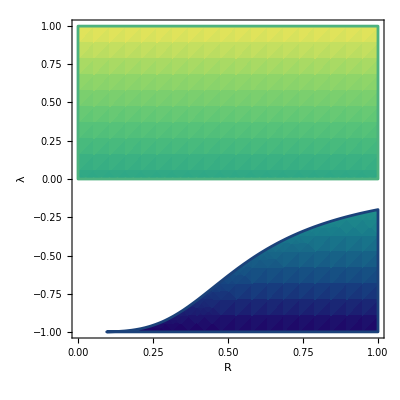

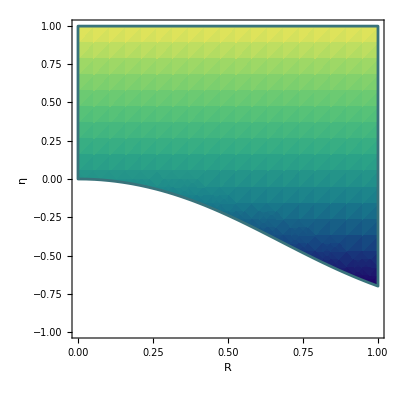

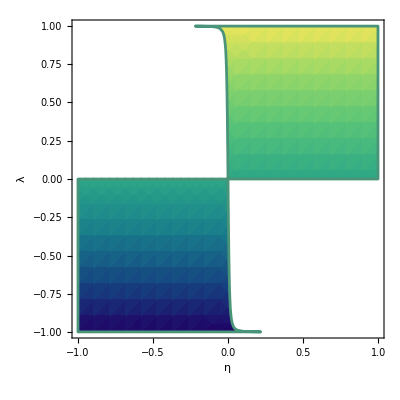

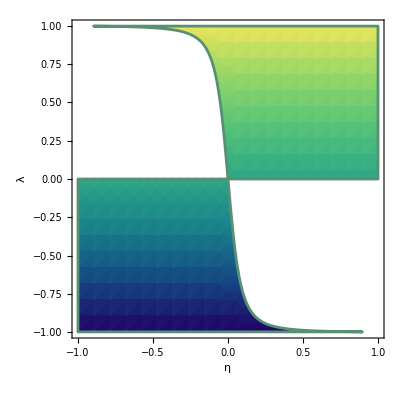

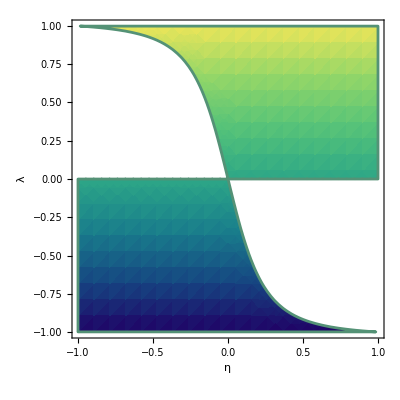

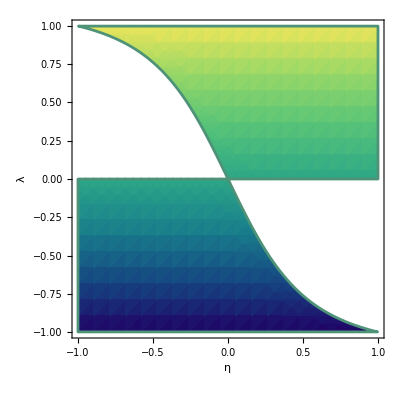

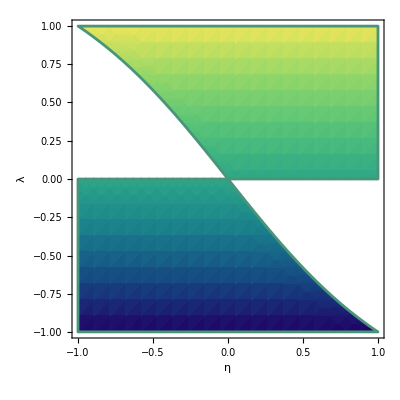

```mathematica
RegionPlot[And[b1tresultlitRe,b1tresultlitIm,b2resultlitRe,b2resultlitIm]/.η->0.2,{R,0,1},{λ,-0.999,0.999},PlotLegends->{"Re[b_1]>0","Re[b_2]>0","Im[b_1]=0","Im[b_2]=0"},AxesLabel->Automatic,ColorFunction->"BlueGreenYellow"]
RegionPlot[And[b1tresultlitRe,b1tresultlitIm,b2resultlitRe,b2resultlitIm]/.λ->0.7,{R,0,1},{η,-0.999,0.999},PlotLegends->{"Re[b_1]>0","Re[b_2]>0","Im[b_1]=0","Im[b_2]=0"},AxesLabel->Automatic,ColorFunction->"BlueGreenYellow"]
RegionPlot[And[b1tresultlitRe,b1tresultlitIm,b2resultlitRe,b2resultlitIm]/.R->0.1,{η,-0.999,0.999},{λ,-0.999,0.999},PlotLegends->{"Re[b_1]>0","Re[b_2]>0","Im[b_1]=0","Im[b_2]=0"},AxesLabel->Automatic,ColorFunction->"BlueGreenYellow"]
RegionPlot[And[b1tresultlitRe,b1tresultlitIm,b2resultlitRe,b2resultlitIm]/.R->0.3,{η,-0.999,0.999},{λ,-0.999,0.999},PlotLegends->{"Re[b_1]>0","Re[b_2]>0","Im[b_1]=0","Im[b_2]=0"},AxesLabel->Automatic,ColorFunction->"BlueGreenYellow"]
RegionPlot[And[b1tresultlitRe,b1tresultlitIm,b2resultlitRe,b2resultlitIm]/.R->0.5,{η,-0.999,0.999},{λ,-0.999,0.999},PlotLegends->{"Re[b_1]>0","Re[b_2]>0","Im[b_1]=0","Im[b_2]=0"},AxesLabel->Automatic,ColorFunction->"BlueGreenYellow"]
RegionPlot[And[b1tresultlitRe,b1tresultlitIm,b2resultlitRe,b2resultlitIm]/.R->0.7,{η,-0.999,0.999},{λ,-0.999,0.999},PlotLegends->{"Re[b_1]>0","Re[b_2]>0","Im[b_1]=0","Im[b_2]=0"},AxesLabel->Automatic,ColorFunction->"BlueGreenYellow"]
RegionPlot[And[b1tresultlitRe,b1tresultlitIm,b2resultlitRe,b2resultlitIm]/.R->0.9,{η,-0.999,0.999},{λ,-0.999,0.999},PlotLegends->{"Re[b_1]>0","Re[b_2]>0","Im[b_1]=0","Im[b_2]=0"},AxesLabel->Automatic,ColorFunction->"BlueGreenYellow"]
```

## 6. Modified Regge-Wheeler equation

Here we will derive the modified Regge-Wheeler equation. We start by defining the tortoise coordinates.

```mathematica
Tort={PD[{1,-SdS}][chiT[]]->√(b1t[r[]]/b2[r[]])PD[{1,-SdS}][chiT[]],
PD[{1,-SdS}][PD[{1,-SdS}][chiT[]]]->(√(b1t[r[]]/b2[r[]]))^2 PD[{1,-SdS}][PD[{1,-SdS}][chiT[]]]+D[√(b1t[r[]]/b2[r[]]),r[]]PD[{1,-SdS}][chiT[]]}//PowerExpand//Simplify
```

{∂_r χ̃→(√(OverTilde[b_1][r]) ∂_r χ̃)/(√b_2[r]),∂_r ∂_r χ̃→(OverTilde[b_1][r] ∂_r ∂_r χ̃)/b_2[r]+(∂_r χ̃ (b_2[r] OverTilde[b_1]'[r]-OverTilde[b_1][r] b_2'[r]))/(2 √(OverTilde[b_1][r]) b_2[r]^(3/2))}

```mathematica
(*oneSide just brings everyhting to the left hand side*)
oneSide=(Head[#][Subtract@@#,0]&);
VarD[chiT[],PD][δL2litchilit2]==0//Simplify;
%*1/b1t[r[]]//oneSide//Expand;
Collect[-%,{-chiT[]/b1t[r[]],b4[r[]]}]
%/.chiT[]->(b1t[r[]]b2[r[]])^(-1/4)chiT[]//Simplify;
%/.Tort//Simplify;
(-%)/Coefficient[%[[1]],PD[{0,-SdS}][PD[{0,-SdS}][chiT[]]]]//Expand;
RWeq=Collect[%,{chiT[],b4[r[]]}]
```

-(χ̃ ((l+l^2) b_4[r]+V[r]))/(OverTilde[b_1][r])-∂_t ∂_t χ̃+(b_2[r] ∂_r ∂_r χ̃)/(OverTilde[b_1][r])+(∂_r χ̃ b_2'[r])/(OverTilde[b_1][r])==0

-∂_t ∂_t χ̃+∂_r ∂_r χ̃+χ̃ ((-l/(OverTilde[b_1][r])-l^2/(OverTilde[b_1][r])) b_4[r]-V[r]/(OverTilde[b_1][r])+(5 b_2[r] (OverTilde[b_1]'[r])^2)/(16 (OverTilde[b_1][r])^3)-(OverTilde[b_1]'[r] b_2'[r])/(8 (OverTilde[b_1][r])^2)+b_2'[r]^2/(16 OverTilde[b_1][r] b_2[r])-(b_2[r] OverTilde[b_1]''[r])/(4 (OverTilde[b_1][r])^2)-b_2''[r]/(4 OverTilde[b_1][r]))==0

```mathematica
DefScalarFunction[FFF,PrintAs->"F"];
DefScalarFunction[Veff,PrintAs->"V_eff"];
```

```mathematica
ToF={FFF[r[]]->1/(b1t[r[]]b2[r[]])^(1/4),D[FFF[r[]],r[]]->D[1/(b1t[r[]]b2[r[]])^(1/4),r[]],D[D[FFF[r[]],r[]],r[]]->D[D[1/(b1t[r[]]b2[r[]])^(1/4),r[]],r[]]}
ToVF={V[r[]]->(l(l+1)b4[r[]]+Veff[r[]])/b1t[r[]]+FFF[r[]](√(b2[r[]]/b1t[r[]]))D[(√(b2[r[]]/b1t[r[]]))D[1/FFF[r[]],r[]],r[]]}
```

{F[r]→1/(OverTilde[b_1][r] b_2[r])^(1/4),F'[r]→-(b_2[r] OverTilde[b_1]'[r]+OverTilde[b_1][r] b_2'[r])/(4 (OverTilde[b_1][r] b_2[r])^(5/4)),F''[r]→(5 (b_2[r] OverTilde[b_1]'[r]+OverTilde[b_1][r] b_2'[r])^2)/(16 (OverTilde[b_1][r] b_2[r])^(9/4))-(2 OverTilde[b_1]'[r] b_2'[r]+b_2[r] OverTilde[b_1]''[r]+OverTilde[b_1][r] b_2''[r])/(4 (OverTilde[b_1][r] b_2[r])^(5/4))}

{V[r]→(l (1+l) b_4[r]+V_eff[r])/(OverTilde[b_1][r])+√(b_2[r]/(OverTilde[b_1][r])) F[r] (-((-(b_2[r] OverTilde[b_1]'[r])/(OverTilde[b_1][r])^2+b_2'[r]/(OverTilde[b_1][r])) F'[r])/(2 √(b_2[r]/(OverTilde[b_1][r])) F[r]^2)+(2 √(b_2[r]/(OverTilde[b_1][r])) F'[r]^2)/F[r]^3-(√(b_2[r]/(OverTilde[b_1][r])) F''[r])/F[r]^2)}

```mathematica
RWeqlit=PD[{1,-SdS}][PD[{1,-SdS}][chiT[]]]-PD[{0,-SdS}][PD[{0,-SdS}][chiT[]]]-V[r[]]chiT[]==0
```

-χ̃ V[r]-∂_t ∂_t χ̃+∂_r ∂_r χ̃==0

```mathematica
RWeqlit[[1]]/.ToVF/.ToF;
RWeq[[1]]/.V[r[]]->Veff[r[]];
%%-%==0//Simplify
```

True

This means we can write the modified Regge-Wheeler equation as

```mathematica
RWeqlit
```

-χ̃ V[r]-∂_t ∂_t χ̃+∂_r ∂_r χ̃==0

where

```mathematica
V->V[r[]]/.ToVF
Subscript[V, eff]->V[r[]]/.ToV//Simplify
```

V→(l (1+l) b_4[r]+V_eff[r])/(OverTilde[b_1][r])+√(b_2[r]/(OverTilde[b_1][r])) F[r] (-((-(b_2[r] OverTilde[b_1]'[r])/(OverTilde[b_1][r])^2+b_2'[r]/(OverTilde[b_1][r])) F'[r])/(2 √(b_2[r]/(OverTilde[b_1][r])) F[r]^2)+(2 √(b_2[r]/(OverTilde[b_1][r])) F'[r]^2)/F[r]^3-(√(b_2[r]/(OverTilde[b_1][r])) F''[r])/F[r]^2)

V_eff→-1/((ℱ[r] 𝒢[r]+𝒥[r]^2)^2)ℋ[r] (2 ℱ[r]^2 𝒢[r]^2+2 𝒥[r]^4+𝒢[r] 𝒥[r]^2 r B'[r] (2 ℋ[r]+r ℋ'[r])+ℱ[r] 𝒢[r] (4 𝒥[r]^2+𝒢[r] r B'[r] (2 ℋ[r]+r ℋ'[r])+B[r] 𝒢[r] (-2 ℋ[r]+r (2 ℋ'[r]+r ℋ''[r])))+B[r] (-𝒢[r]^2 r ℱ'[r] (2 ℋ[r]+r ℋ'[r])+𝒥[r]^2 r 𝒢'[r] (2 ℋ[r]+r ℋ'[r])+𝒢[r] 𝒥[r] (-2 ℋ[r] (𝒥[r]+2 r 𝒥'[r])+r (2 𝒥[r] ℋ'[r]-2 r ℋ'[r] 𝒥'[r]+𝒥[r] r ℋ''[r]))))

However, we can also write V_eff with the simpler form

```mathematica
Hold[(r[]^2 H[r[]]D[b2[r[]]D[1/(r[]^2 H[r[]]),r[]],r[]]-2H[r[]])]
(V[r[]]/.ToV)-(%/.Tob)==0//ReleaseHold//Simplify
ToVeff=Veff[r[]]->r[]^2 H[r[]]D[b2[r[]]D[1/(r[]^2 H[r[]]),r[]]/.Tob,r[]]-2H[r[]]//Simplify
```

Hold[r^2 ℋ[r] ∂_r (b_2[r] ∂_r 1/(r^2 ℋ[r]))-2 ℋ[r]]

True

V_eff[r]→-1/((ℱ[r] 𝒢[r]+𝒥[r]^2)^2)ℋ[r] (2 ℱ[r]^2 𝒢[r]^2+2 𝒥[r]^4+𝒢[r] 𝒥[r]^2 r B'[r] (2 ℋ[r]+r ℋ'[r])+ℱ[r] 𝒢[r] (4 𝒥[r]^2+𝒢[r] r B'[r] (2 ℋ[r]+r ℋ'[r])+B[r] 𝒢[r] (-2 ℋ[r]+r (2 ℋ'[r]+r ℋ''[r])))+B[r] (-𝒢[r]^2 r ℱ'[r] (2 ℋ[r]+r ℋ'[r])+𝒥[r]^2 r 𝒢'[r] (2 ℋ[r]+r ℋ'[r])+𝒢[r] 𝒥[r] (-2 ℋ[r] (𝒥[r]+2 r 𝒥'[r])+r (2 𝒥[r] ℋ'[r]-2 r ℋ'[r] 𝒥'[r]+𝒥[r] r ℋ''[r]))))

Let us now look at the form of these expressions specific for our theory

```mathematica
Tob1tSimp={b1t[r[]]->(H[r[]]^2*r[]^2)/(B[r[]]*G[r[]]),Derivative[1][b1t][r[]]->D[(H[r[]]^2*r[]^2)/(B[r[]]*G[r[]]),r[]],Derivative[2][b1t][r[]]->D[D[(H[r[]]^2*r[]^2)/(B[r[]]*G[r[]]),r[]],r[]]}//Simplify
```

{OverTilde[b_1][r]→(ℋ[r]^2 r^2)/(B[r] 𝒢[r]),OverTilde[b_1]'[r]→-(ℋ[r] r (𝒢[r] ℋ[r] r B'[r]+B[r] (ℋ[r] r 𝒢'[r]-2 𝒢[r] (ℋ[r]+r ℋ'[r]))))/(B[r]^2 𝒢[r]^2),OverTilde[b_1]''[r]→1/(B[r]^3 𝒢[r]^3)(2 𝒢[r]^2 ℋ[r]^2 r^2 B'[r]^2-B[r] 𝒢[r] ℋ[r] r (-2 ℋ[r] r B'[r] 𝒢'[r]+𝒢[r] (4 ℋ[r] B'[r]+4 r B'[r] ℋ'[r]+ℋ[r] r B''[r]))+B[r]^2 (2 ℋ[r]^2 r^2 𝒢'[r]^2-𝒢[r] ℋ[r] r (4 r 𝒢'[r] ℋ'[r]+ℋ[r] (4 𝒢'[r]+r 𝒢''[r]))+2 𝒢[r]^2 (ℋ[r]^2+r^2 ℋ'[r]^2+ℋ[r] r (4 ℋ'[r]+r ℋ''[r]))))}

```mathematica
TobSimp={b1t[r[]]->(b1t[r[]]/.Tob1t/.Tob//Simplify),D[b1t[r[]],r[]]->D[(b1t[r[]]/.Tob1t/.Tob//Simplify),r[]]//Simplify,D[D[b1t[r[]],r[]],r[]]->D[D[(b1t[r[]]/.Tob1t/.Tob//Simplify),r[]],r[]]//Simplify,
b2[r[]]->(b2[r[]]/.Tob//Simplify),D[b2[r[]],r[]]->D[(b2[r[]]/.Tob//Simplify),r[]]//Simplify,D[D[b2[r[]],r[]],r[]]->D[D[(b2[r[]]/.Tob//Simplify),r[]],r[]]//Simplify,
b4[r[]]->(b4[r[]]/.Tob)}/.{D[H[r[]],r[]]->0,D[D[H[r[]],r[]],r[]]->0}//Simplify
ToFGHJ/.ncXtheory;
%/.Xtoϕ/.CDphirules1/.CDphirules2/.psirules;
ToFGHJSimp=%//Simplify
ToderFGHJSimp=ToderFGHJ/.psirules//Simplify;
```

{OverTilde[b_1][r]→(ℋ[r]^2 r^2)/(B[r] 𝒢[r]),OverTilde[b_1]'[r]→-(ℋ[r]^2 r (𝒢[r] r B'[r]+B[r] (-2 𝒢[r]+r 𝒢'[r])))/(B[r]^2 𝒢[r]^2),OverTilde[b_1]''[r]→1/(B[r]^3 𝒢[r]^3)ℋ[r]^2 (2 𝒢[r]^2 r^2 B'[r]^2-B[r] 𝒢[r] r (-2 r B'[r] 𝒢'[r]+𝒢[r] (4 B'[r]+r B''[r]))+B[r]^2 (2 𝒢[r]^2+2 r^2 𝒢'[r]^2-𝒢[r] r (4 𝒢'[r]+r 𝒢''[r]))),b_2[r]→(B[r] 𝒢[r] ℋ[r]^2 r^2)/(ℱ[r] 𝒢[r]+𝒥[r]^2),b_2'[r]→1/((ℱ[r] 𝒢[r]+𝒥[r]^2)^2)ℋ[r]^2 r (𝒢[r] (ℱ[r] 𝒢[r]+𝒥[r]^2) r B'[r]+B[r] (2 ℱ[r] 𝒢[r]^2-𝒢[r]^2 r ℱ'[r]+𝒥[r]^2 r 𝒢'[r]+2 𝒢[r] 𝒥[r] (𝒥[r]-r 𝒥'[r]))),b_2''[r]→1/((ℱ[r] 𝒢[r]+𝒥[r]^2)^3)ℋ[r]^2 ((ℱ[r] 𝒢[r]+𝒥[r]^2) r (-2 𝒢[r]^2 r B'[r] ℱ'[r]+2 𝒥[r]^2 r B'[r] 𝒢'[r]+ℱ[r] 𝒢[r]^2 (4 B'[r]+r B''[r])+𝒢[r] 𝒥[r] (4 𝒥[r] B'[r]-4 r B'[r] 𝒥'[r]+𝒥[r] r B''[r]))+B[r] (2 ℱ[r]^2 𝒢[r]^3+2 𝒢[r]^3 r^2 ℱ'[r]^2-𝒢[r]^2 𝒥[r] r (-8 r ℱ'[r] 𝒥'[r]+𝒥[r] (4 ℱ'[r]+r ℱ''[r]))+𝒥[r]^3 r (-4 r 𝒢'[r] 𝒥'[r]+𝒥[r] (4 𝒢'[r]+r 𝒢''[r]))+2 𝒢[r] 𝒥[r]^2 (𝒥[r]^2+r^2 (-2 ℱ'[r] 𝒢'[r]+3 𝒥'[r]^2)-𝒥[r] r (4 𝒥'[r]+r 𝒥''[r]))-ℱ[r] (2 𝒥[r]^2 r^2 𝒢'[r]^2+𝒢[r]^3 r (4 ℱ'[r]+r ℱ''[r])-𝒢[r] 𝒥[r] r (4 r 𝒢'[r] 𝒥'[r]+𝒥[r] (4 𝒢'[r]+r 𝒢''[r]))+𝒢[r]^2 (-4 𝒥[r]^2+2 r^2 𝒥'[r]^2+2 𝒥[r] r (4 𝒥'[r]+r 𝒥''[r]))))),b_4[r]→ℋ[r]}

{ℱ[r]→2 (M_Pl^2-(q^2 λ)/(2 B[r] √((q^2 λ)/(2 λ+2 M_Pl^2 η r^2)))+λ √((q^2 λ)/(2 λ+2 M_Pl^2 η r^2))),𝒢[r]→(√2 q^2 λ+2 M_Pl^2 B[r] √((q^2 λ)/(λ+M_Pl^2 η r^2)))/(B[r] √((q^2 λ)/(λ+M_Pl^2 η r^2))),ℋ[r]→2 M_Pl^2,𝒥[r]→(q^2 λ √(2-(2 λ B[r])/(λ+M_Pl^2 η r^2)))/(B[r] √((q^2 λ)/(λ+M_Pl^2 η r^2)))}

```mathematica
V[r[]]/.ToVF
%/.ToF//Simplify
%/.ToVeff/.TobSimp//Simplify;
%/.{Derivative[1][H][r[]]->0,Derivative[2][H][r[]]->0}//Simplify
%/.ToFGHJSimp/.ToderFGHJSimp//Simplify;
%/.ToB//PowerExpand//Simplify;
Vfull=FullSimplify[%,Assumptions->{r[]>0,mass∈Reals,η∈Reals,λ∈Reals}]
```

(l (1+l) b_4[r]+V_eff[r])/(OverTilde[b_1][r])+√(b_2[r]/(OverTilde[b_1][r])) F[r] (-((-(b_2[r] OverTilde[b_1]'[r])/(OverTilde[b_1][r])^2+b_2'[r]/(OverTilde[b_1][r])) F'[r])/(2 √(b_2[r]/(OverTilde[b_1][r])) F[r]^2)+(2 √(b_2[r]/(OverTilde[b_1][r])) F'[r]^2)/F[r]^3-(√(b_2[r]/(OverTilde[b_1][r])) F''[r])/F[r]^2)

1/(16 (OverTilde[b_1][r])^3 b_2[r])(-5 b_2[r]^2 (OverTilde[b_1]'[r])^2+2 OverTilde[b_1][r] b_2[r] (OverTilde[b_1]'[r] b_2'[r]+2 b_2[r] OverTilde[b_1]''[r])+(OverTilde[b_1][r])^2 (-b_2'[r]^2+4 b_2[r] (4 l (1+l) b_4[r]+4 V_eff[r]+b_2''[r])))

(B[r] 𝒢[r] (16 (-2+l+l^2) ℱ[r]^3 𝒢[r]^3+4 𝒥[r]^2 (4 (-2+l+l^2) 𝒥[r]^4-4 𝒢[r] ℋ[r] 𝒥[r]^2 r B'[r]-𝒢[r]^2 ℋ[r] r^2 B'[r] ℱ'[r]-2 𝒢[r] ℋ[r] 𝒥[r] r^2 B'[r] 𝒥'[r])+ℱ[r]^2 𝒢[r] (48 (-2+l+l^2) 𝒢[r] 𝒥[r]^2-4 𝒢[r] ℋ[r] r B'[r] (4 𝒢[r]+r 𝒢'[r])+B[r] ℋ[r] (32 𝒢[r]^2+3 r^2 𝒢'[r]^2-4 𝒢[r] r^2 𝒢''[r]))+B[r] ℋ[r] (7 𝒢[r]^3 r^2 ℱ'[r]^2-8 𝒥[r]^3 r 𝒢'[r] (2 𝒥[r]+r 𝒥'[r])-4 𝒢[r]^2 𝒥[r] r (-7 r ℱ'[r] 𝒥'[r]+𝒥[r] (-4 ℱ'[r]+r ℱ''[r]))+4 𝒢[r] 𝒥[r]^2 (8 𝒥[r]^2+r^2 (-3 ℱ'[r] 𝒢'[r]+5 𝒥'[r]^2)-2 𝒥[r] r (-4 𝒥'[r]+r 𝒥''[r])))-2 ℱ[r] (2 𝒢[r] (-12 (-2+l+l^2) 𝒥[r]^4+𝒢[r]^2 ℋ[r] r^2 B'[r] ℱ'[r]+ℋ[r] 𝒥[r]^2 r B'[r] (8 𝒢[r]+r 𝒢'[r])+2 𝒢[r] ℋ[r] 𝒥[r] r^2 B'[r] 𝒥'[r])+B[r] ℋ[r] (2 𝒥[r]^2 r^2 𝒢'[r]^2+2 𝒢[r]^3 r (-4 ℱ'[r]+r ℱ''[r])+2 𝒢[r] 𝒥[r] r (-5 r 𝒢'[r] 𝒥'[r]+𝒥[r] (4 𝒢'[r]+r 𝒢''[r]))-𝒢[r]^2 (32 𝒥[r]^2+r^2 (ℱ'[r] 𝒢'[r]-4 𝒥'[r]^2)-4 𝒥[r] r (-4 𝒥'[r]+r 𝒥''[r]))))))/(16 ℋ[r] (ℱ[r] 𝒢[r]+𝒥[r]^2)^3 r^2)

((2 M_Pl^2 B[r]+√2 q √λ √(λ+M_Pl^2 η r^2)) (2 M_Pl^2 B[r] (96 M_Pl^4 λ^3 √(λ+M_Pl^2 η r^2)+48 q^2 λ^5 √(λ+M_Pl^2 η r^2)+288 M_Pl^6 η λ^2 r^2 √(λ+M_Pl^2 η r^2)+80 M_Pl^2 q^2 η λ^4 r^2 √(λ+M_Pl^2 η r^2)+288 M_Pl^8 η^2 λ r^4 √(λ+M_Pl^2 η r^2)+27 M_Pl^4 q^2 η^2 λ^3 r^4 √(λ+M_Pl^2 η r^2)+96 M_Pl^10 η^3 r^6 √(λ+M_Pl^2 η r^2)+4 √2 M_Pl^2 q λ^(3/2) (λ+M_Pl^2 η r^2) (24 λ^2+44 M_Pl^2 η λ r^2+17 M_Pl^4 η^2 r^4))+(λ+M_Pl^2 η r^2) (16 √2 l (1+l) q^3 λ^(11/2)+32 M_Pl^10 η^2 r^4 (√2 q η √λ r^2+2 (-3+l+l^2) √(λ+M_Pl^2 η r^2))+8 M_Pl^8 η λ r^2 (3 √2 (-5+4 l (1+l)) q η √λ r^2+16 (-3+l+l^2) √(λ+M_Pl^2 η r^2))+4 M_Pl^2 q^2 λ^4 (√2 q η √λ (r+2 l r)^2+24 (-1+l+l^2) √(λ+M_Pl^2 η r^2))+8 M_Pl^6 λ^2 (√2 (-43+24 l (1+l)) q η √λ r^2+8 (-3+l+l^2) √(λ+M_Pl^2 η r^2)+3 q^2 η^2 r^4 √(λ+M_Pl^2 η r^2))+3 M_Pl^4 q λ^3 (16 (-1+2 l (1+l)) q η r^2 √(λ+M_Pl^2 η r^2)+√2 √λ (32 (-2+l+l^2)+q^2 η^2 r^4)))))/(16 M_Pl^2 r^2 (λ+M_Pl^2 η r^2)^2 (√2 q λ^(3/2)+2 M_Pl^2 √(λ+M_Pl^2 η r^2))^3)

We now show that we can write this potential in a simplified form.

```mathematica
Vcompact=((B[r[]](l(l+1)+3(B[r[]]-1)))/r[]^2)(1+(q β √(2 β^2+r[]^2))/B[r[]])+(q β(B[r[]]+q β √(2 β^2+r[]^2)))/(4 r[]^2(2 β^2+r[]^2)(2q β^3+√(2 β^2+r[]^2))^3)*(q^2 β^6(192 β^4+104 β^2 r[]^2+3 r[]^4)+2(2 β^2+r^2)(24 β^4+17 β^2 r^2+2 r^4)+6q β^3 √(2 β^2+r[]^2)(32 β^4+20 β^2 r[]^2+r[]^4)-β^2 B[r[]](2(48 q^2 β^6(2 β^2+r[]^2)+48 β^4+56 β^2 r[]^2+19 r[]^4)+(q β^3)/(√(2 β^2+r[]^2))(384 β^4+416 β^2 r[]^2+117 r[]^4)))
```

((l (1+l)+3 (-1+B[r])) B[r] (1+(q β √(2 β^2+r^2))/B[r]))/r^2+(q β (B[r]+q β √(2 β^2+r^2)) (6 q β^3 √(2 β^2+r^2) (32 β^4+20 β^2 r^2+r^4)+2 (2 β^2+r^2) (24 β^4+17 β^2 r^2+2 r^4)+q^2 β^6 (192 β^4+104 β^2 r^2+3 r^4)-β^2 B[r] ((q β^3 (384 β^4+416 β^2 r^2+117 r^4))/(√(2 β^2+r^2))+2 (48 β^4+56 β^2 r^2+19 r^4+48 q^2 β^6 (2 β^2+r^2)))))/(4 r^2 (2 β^2+r^2) (2 q β^3+√(2 β^2+r^2))^3)

```mathematica
(Vfull-Vcompact)==0/.ToBeta/.ToGeomUn//Expand//PowerExpand//Simplify
```

True

We work with the following redefinition of the beta parameter.

```mathematica
DefConstantSymbol[betaHat,PrintAs->ToString[β̂,StandardForm]]
betaHat==mass*q*β/Mpl^3
betaHatsub=Solve[%,β]//Flatten
```

β̂==(M q β)/M_Pl^3

{β→(β̂ M_Pl^3)/(M q)}

```mathematica
Vfull/.ToBeta/.ToM/.Λ->0;
Vseries=(Series[%,{β,0,7}]//Normal//PowerExpand)/.betaHatsub
```

((β̂)^2 M_Pl^4)/M^2+((-2 M+M_Pl^2 r) (-6 M+l M_Pl^2 r+l^2 M_Pl^2 r))/(M_Pl^4 r^4)+(β̂ (-8 M+M_Pl^2 r+l M_Pl^2 r+l^2 M_Pl^2 r))/(M r^2)+((β̂)^4 M_Pl^6 (56 M q^2-15 M_Pl^2 q^2 r))/(2 M^4 q^4 r^3)+((β̂)^2 (-38 β̂ M M_Pl^3+21 β̂ M_Pl^5 r-(4 β̂ M_Pl^7 r^2)/M+(β̂ l M_Pl^7 r^2)/M+(β̂ l^2 M_Pl^7 r^2)/M))/(M^2 M_Pl q^2 r^5)+((β̂)^6 M_Pl^8 (444 M^2 q^2-500 M M_Pl^2 q^2 r+135 M_Pl^4 q^2 r^2))/(4 M^6 q^6 r^6)+((β̂)^4 M_Pl^3 (156 β̂ M M_Pl^3-126 β̂ M_Pl^5 r+(27 β̂ M_Pl^7 r^2)/M-(β̂ l M_Pl^7 r^2)/M-(β̂ l^2 M_Pl^7 r^2)/M-(9 β̂ M_Pl^7 q^2 r^6)/M))/(2 M^4 q^4 r^7)+((β̂)^6 M_Pl^7 (-402 β̂ M M_Pl^3+355 β̂ M_Pl^5 r-(80 β̂ M_Pl^7 r^2)/M+(β̂ l M_Pl^7 r^2)/M+(β̂ l^2 M_Pl^7 r^2)/M-174 β̂ M_Pl^5 q^2 r^5+(72 β̂ M_Pl^7 q^2 r^6)/M))/(2 M^6 q^6 r^9)

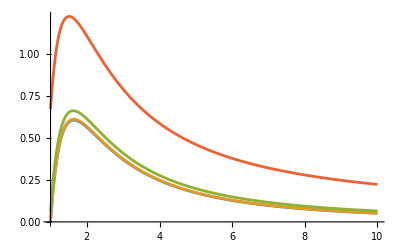

```mathematica
Plot[{Vseries/.{l->2,mass->1/2,Mpl->1,betaHat->0},
Vseries/.{l->2,mass->1/2,q->1,Mpl->1,betaHat->0.001},
Vseries/.{l->2,mass->1/2,q->1,Mpl->1,betaHat->0.01},
Vseries/.{l->2,mass->1/2,q->1,Mpl->1,betaHat->0.1}},{r[],1,10}]
```

## 7. Quasinormal modes via the WKB method

Here we will obtain the complex quasinormal frequencies form the effective potential by applying the WKB formula. To do so, we use the package made available in https://arxiv.org/pdf/1904.10333.pdf, which you will need to add to your directory.

```mathematica
Import[NotebookDirectory[]<>"WKB.m"];If[!IntegerQ[WKB`WKBFormulaOrder],Print["Old version of WKB.m - please update the file."]];
f[r_]=(1-2/r)
fNU[r_]=(1-(2*mass)/(r*Mpl^2))
(*new tortoise coordinate*)
Simplify[(√(b2[r[]]/b1t[r[]])/.TobSimp/.ToFGHJSimp/.ToM/.Λ->0),Assumptions->q>0]/.{r[]->r};
%/.ToBeta;
%/.betaHatsub;
Simplify[fncX[r_]=%/.{q->1,mass->1}/.ToGeomUn/.r[]->r,Assumptions->betaHat>0]
Simplify[(Series[%%,{betaHat,0,7}]//Normal),Assumptions->Mpl>0&&r>0&&betaHat>0&&mass>0&&q>0&&-2*mass+Mpl^2*r>0];
fncXNU7[r_]=%/.r[]->r
fncXNU2[r_]=Series[%,{betaHat,0,2}]//Normal
fncX7[r_]=%%/.{q->1,mass->1}/.ToGeomUn
fncX2[r_]=%%/.ToGeomUn
```

1-2/r

1-(2 M)/(M_Pl^2 r)

√(((2 (β̂)^2+r^2) (β̂ r+(-2+r) √(1/(2 (β̂)^2+r^2)))^2)/(r^2 (1+2 (β̂)^3 √(1/(2 (β̂)^2+r^2)))))

(4 (β̂)^3 M^5 M_Pl^6 q^4 r^4-2 (β̂)^4 M^3 M_Pl^10 q^4 r^6+2 β̂ M^6 M_Pl^4 q^6 r^7+(β̂)^5 M^2 M_Pl^10 q^2 r^2 (-4 M+M_Pl^2 r)+3 (β̂)^6 M M_Pl^12 q^2 r^3 (-2 M+M_Pl^2 r)+2 M^7 q^6 r^5 (-2 M+M_Pl^2 r)+(β̂)^7 M_Pl^14 (6 M+M_Pl^2 r (-2+3 q^2 r^4)))/(2 M^7 M_Pl^2 q^6 r^6)

(β̂ M_Pl^2 r)/M+(-2 M+M_Pl^2 r)/(M_Pl^2 r)

((β̂)^5 (-4+r) r^2+3 (β̂)^6 (-2+r) r^3+4 (β̂)^3 r^4+2 (-2+r) r^5-2 (β̂)^4 r^6+2 β̂ r^7+(β̂)^7 (6+r (-2+3 r^4)))/(2 r^6)

(β̂ r)/M+(-2 M+r)/r

### Numerical

For b=0, the QNM values recover the well-known GR results

```mathematica
WKBFormula[6,Vfull/.ToM/.ToGeomUn/.ToBeta/.{l->2,mass->1,Λ->0,r[]->r,β->0},f[r],{r,3},0]
WKBFormula[6,Vfull/.ToM/.ToGeomUn/.ToBeta/.{l->3,mass->1,Λ->0,r[]->r,β->0},f[r],{r,3},0]
```

{0.373619-0.088891 ⅈ,0.373504-0.0889183 ⅈ,0.373553-0.089124 ⅈ,0.373162-0.0892174 ⅈ,0.37435-0.0940632 ⅈ,0.39885-0.0882854 ⅈ,r→3.28078}

{0.599443-0.0927025 ⅈ,0.599441-0.0927028 ⅈ,0.599441-0.0927012 ⅈ,0.599265-0.0927284 ⅈ,0.599609-0.0949281 ⅈ,0.616561-0.0923181 ⅈ,r→3.10611}

And we can see that these vary considerably by turning on b. For l=2

```mathematica
WKBFormula[6,Vfull/.ToM/.ToBeta/.betaHatsub/.ToGeomUn/.{l->2,mass->1,Λ->0,r[]->r,q->1,betaHat->10^-3},fncX2[r]/.{betaHat->10^-2,mass->1},{r,3},0]
WKBFormula[6,Vfull/.ToM/.ToBeta/.betaHatsub/.ToGeomUn/.{l->2,mass->1,Λ->0,r[]->r,q->1,betaHat->10^-2},fncX2[r]/.{betaHat->10^-2,mass->1},{r,3},0]
WKBFormula[6,Vfull/.ToM/.ToBeta/.betaHatsub/.ToGeomUn/.{l->2,mass->1,Λ->0,r[]->r,q->1,betaHat->10^-1},fncX2[r]/.{betaHat->10^-2,mass->1},{r,3},0]
```

{0.374175-0.0960694 ⅈ,0.374053-0.0961008 ⅈ,0.374118-0.0963529 ⅈ,0.373682-0.0964652 ⅈ,0.375134-0.101946 ⅈ,0.402147-0.0950984 ⅈ,r→3.27776}

{0.390134-0.0938158 ⅈ,0.390009-0.0938458 ⅈ,0.390068-0.0940913 ⅈ,0.389661-0.0941896 ⅈ,0.39096-0.099429 ⅈ,0.417138-0.0931893 ⅈ,r→3.25147}

{0.535217-0.0782725 ⅈ,0.535087-0.0782914 ⅈ,0.535114-0.0784769 ⅈ,0.534885-0.0785105 ⅈ,0.535419-0.0820718 ⅈ,0.556032-0.0790294 ⅈ,r→3.05147}

```mathematica
Prepend[Table[{10^-i//N,WKBFormula[6,Vfull/.ToM/.ToBeta/.betaHatsub/.ToGeomUn/.{l->2,mass->1,Λ->0,r[]->r,q->1,betaHat->10^-i},fncX2[r]/.{betaHat->10^-i,mass->1},{r,3},0][[1]]},{i,3}],{"β̂","quasinormal frequency"}]//TableForm
```

β̂ | quasinormal frequency
0.1 | 0.523444-0.135257 ⅈ
0.01 | 0.390134-0.0938158 ⅈ
0.001 | 0.375292-0.0893873 ⅈ

And for l=3

```mathematica
Prepend[Table[{10^-i//N,WKBFormula[6,Vfull/.ToM/.ToBeta/.betaHatsub/.ToGeomUn/.{l->3,mass->1,Λ->0,r[]->r,q->1,betaHat->10^-i},fncX2[r]/.{betaHat->10^-i,mass->1},{r,3},0][[1]]},{i,3}],{"β̂","quasinormal frequency"}]//TableForm
```

β̂ | quasinormal frequency
0.1 | 0.837908-0.143395 ⅈ
0.01 | 0.625834-0.0980381 ⅈ
0.001 | 0.602117-0.0932395 ⅈ

We know show that the best approximation is given for the 6th order WKB.

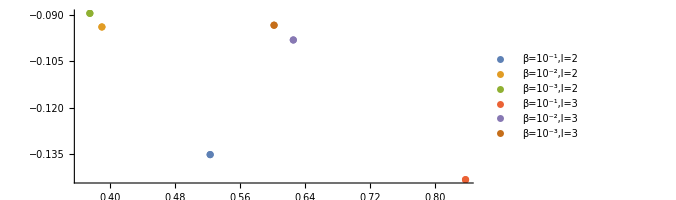

```mathematica
Table[Hold[WKBFormula[6,Vfull/.ToM/.ToBeta/.betaHatsub/.ToGeomUn/.{l->2,mass->1,Λ->0,r[]->r,q->1,betaHat->10^-i},fncX2[r]/.{betaHat->10^-i,mass->1},{r,3},0]],{i,1,3}];
Table[%[[ii]]/.{i->ii},{ii,1,3}]//ReleaseHold;
datal2=Partition[Table[%[[i]][[1]],{i,1,3}]//Flatten,1];
Table[Hold[WKBFormula[6,Vfull/.ToM/.ToBeta/.betaHatsub/.ToGeomUn/.{l->3,mass->1,Λ->0,r[]->r,q->1,betaHat->10^-i},fncX2[r]/.{betaHat->10^-i,mass->1},{r,3},0]],{i,1,3}];
Table[%[[ii]]/.{i->ii},{ii,1,3}]//ReleaseHold;
datal3=Partition[Table[%[[i]][[1]],{i,1,3}]//Flatten,1];
ComplexListPlot[Partition[{datal2,datal3}//Flatten,1],PlotLegends->{"β=10^-1,l=2","β=10^-2,l=2","β=10^-3,l=2","β=10^-1,l=3","β=10^-2,l=3","β=10^-3,l=3"}]
```

### Analytical

```mathematica
Vfull2=Vfull/.ToBeta/.ToM/.{l->2,Λ->0}/.betaHatsub;
```

```mathematica
D[Vfull2/.{betaHat->0}//Simplify,r[]]//Simplify;
Solve[(%/.ToM/.{l->2,(*mass->1,*)Λ->0})==0,r[]];
r0GR=%[[2]]//N
r0GR30=N[%%[[2]],30]
r0GR60=N[%%%[[2]],60]
```

{r→(3.28078 M)/M_Pl^2}

{r→(3.28077640640441513745535246399 M)/M_Pl^2}

{r→(3.28077640640441513745535246399351925628679980634340510859966 M)/M_Pl^2}

```mathematica
-D[Vfull2,r[]]/D[D[Vfull2,r[]],r[]];
r0MG={r[]->(r0GR[[1]][[2]]+%/.r0GR)}
r0MG30={r[]->(r0GR30[[1]][[2]]+%%/.r0GR30)};
r0MG60={r[]->(r0GR60[[1]][[2]]+%%%/.r0GR60)};
```

```mathematica
r0MG2=Series[r0MG30[[1,2]],{betaHat,0,2}]//PowerExpand//Normal;
r0MG2Sub={r[]->%}//Expand
r0MG3=Series[r0MG30[[1,2]],{betaHat,0,3}]//PowerExpand//Normal;
r0MG3Sub={r[]->%}//Expand
r0MG7=Series[r0MG60[[1,2]],{betaHat,0,7}]//PowerExpand//Normal;
r0MG7Sub={r[]->%}/.{q->1,mass->1}/.ToGeomUn//Expand
```

{r→(3.28077640640441513745535246399 M)/M_Pl^2-(3.03058025409964739029335 β̂ M)/M_Pl^2+(0.83160014024703637249 (β̂)^2 M)/M_Pl^2}

{r→(3.28077640640441513745535246399 M)/M_Pl^2-(3.03058025409964739029335 β̂ M)/M_Pl^2+(0.83160014024703637249 (β̂)^2 M)/M_Pl^2-(0.228193525752495 (β̂)^3 M)/M_Pl^2-(1.8502047525474 (β̂)^3 M_Pl^6)/(M^3 q^2)}

{r→3.28077640640441513745535246399351925628679980634340510859966-3.03058025409964739029334585563894200971214387510166669 β̂+0.83160014024703637248811550610961515591833997202408 (β̂)^2-2.07839827829989134155920567397250282278472026 (β̂)^3-9.691260554746023162534967585568027311586 (β̂)^4-12.29516568632882013815943839599546 (β̂)^5+18.41728111510785510640502244 (β̂)^6-41.42392495274763770829801022 (β̂)^7}

First we calculate QNM expressions to quadratic order in β̂

```mathematica
Dtort2[xx_]:=fncXNU2[r]D[xx,r]
V1der[r,betaHat_]=Dtort2[Vseries/.{q->1,r[]->r}]//Simplify;
V2der[r,betaHat_]=Dtort2[%]//Simplify;
V3der[r,betaHat_]=Dtort2[%]//Simplify;
V4der[r,betaHat_]=Dtort2[%]//Simplify;
V5der[r,betaHat_]=Dtort2[%]//Simplify;
V6der[r,betaHat_]=Dtort2[%]//Simplify;
V7der[r,betaHat_]=Dtort2[%]//Simplify;
V8der[r,betaHat_]=Dtort2[%]//Simplify;
V9der[r,betaHat_]=Dtort2[%];
V10der[r,betaHat_]=Dtort2[%];
V11der[r,betaHat_]=Dtort2[%];
V12der[r,betaHat_]=Dtort2[%];
```

```mathematica
Vdersubsv2[betaHat_]={V00->Hold[Vseries/.r0MG2Sub/.{q->1}],
V2->Hold[V2der[r,betaHat]/.r->r[]/.r0MG2Sub ],
V3->Hold[V3der[r,betaHat]/.r->r[]/.r0MG2Sub ],
V4->Hold[V4der[r,betaHat]/.r->r[]/.r0MG2Sub ],
V5->Hold[V5der[r,betaHat]/.r->r[]/.r0MG2Sub ],
V6->Hold[V6der[r,betaHat]/.r->r[]/.r0MG2Sub ],
V7->Hold[V7der[r,betaHat]/.r->r[]/.r0MG2Sub ],
V8->Hold[V8der[r,betaHat]/.r->r[]/.r0MG2Sub ],
V9->Hold[V9der[r,betaHat]/.r->r[]/.r0MG2Sub ],
V10->Hold[V10der[r,betaHat]/.r->r[]/.r0MG2Sub ],
V11->Hold[V11der[r,betaHat]/.r->r[]/.r0MG2Sub ],
V12->Hold[V12der[r,betaHat]/.r->r[]/.r0MG2Sub ]}/.{l->ll}
```

{V00→Hold[Vseries/.r0MG2Sub/.{q→1}],V2→Hold[V2der[r,β̂]/.r→r/.r0MG2Sub],V3→Hold[V3der[r,β̂]/.r→r/.r0MG2Sub],V4→Hold[V4der[r,β̂]/.r→r/.r0MG2Sub],V5→Hold[V5der[r,β̂]/.r→r/.r0MG2Sub],V6→Hold[V6der[r,β̂]/.r→r/.r0MG2Sub],V7→Hold[V7der[r,β̂]/.r→r/.r0MG2Sub],V8→Hold[V8der[r,β̂]/.r→r/.r0MG2Sub],V9→Hold[V9der[r,β̂]/.r→r/.r0MG2Sub],V10→Hold[V10der[r,β̂]/.r→r/.r0MG2Sub],V11→Hold[V11der[r,β̂]/.r→r/.r0MG2Sub],V12→Hold[V12der[r,β̂]/.r→r/.r0MG2Sub]}

```mathematica
BasicWKBFormula[n,{V00,V2,V3,V4,V5,V6,V7,V8,V9,V10,V11,V12}]/.n->0//Simplify;
%/.Vdersubsv2[betaHat]//ReleaseHold;
ome2=√%
```

```mathematica
ome2/.l->2;
Series[%,{betaHat,0,2}]//Normal;
QNMNU2=%//PowerExpand//Simplify
```

(((0.3736193572-0.08889097955 ⅈ)+(1.67503141-0.4967372562 ⅈ) β̂-(2.385484472-0.16407857 ⅈ) (β̂)^2) M_Pl^2)/M

Now we extend this calculation to 7th order. To make it feasible, we impose geometric units from the start,  specify to the l=2 mode, and fix fiducial values for M and q.

```mathematica
Dtort7[xx_]:=fncX7[r]D[xx,r]
V1der[r,betaHat_]=Dtort7 [Vseries/.{q->1,mass->1,r[]->r}/.ToGeomUn/.l->2]//Simplify;
V2der[r,betaHat_]=Dtort7 [%]//Simplify;
V3der[r,betaHat_]=Dtort7 [%]//Simplify;
V4der[r,betaHat_]=Dtort7 [%]//Simplify;
V5der[r,betaHat_]=Dtort7 [%]//Simplify;
V6der[r,betaHat_]=Dtort7 [%]//Simplify;
V7der[r,betaHat_]=Dtort7 [%]//Simplify;
V8der[r,betaHat_]=Dtort7 [%]//Simplify;
V9der[r,betaHat_]=Dtort7 [%];
V10der[r,betaHat_]=Dtort7 [%];
V11der[r,betaHat_]=Dtort7 [%];
V12der[r,betaHat_]=Dtort7 [%];
```

```mathematica
Vdersubsv3[betaHat_]={V00->Hold[(Vseries/.{q->1,mass->1,l->2}/.ToGeomUn)/.r0MG7Sub],
V2->Hold[V2der[r,betaHat]/.r->r[]/.r0MG7Sub ],
V3->Hold[V3der[r,betaHat]/.r->r[]/.r0MG7Sub ],
V4->Hold[V4der[r,betaHat]/.r->r[]/.r0MG7Sub ],
V5->Hold[V5der[r,betaHat]/.r->r[]/.r0MG7Sub ],
V6->Hold[V6der[r,betaHat]/.r->r[]/.r0MG7Sub ],
V7->Hold[V7der[r,betaHat]/.r->r[]/.r0MG7Sub ],
V8->Hold[V8der[r,betaHat]/.r->r[]/.r0MG7Sub ],
V9->Hold[V9der[r,betaHat]/.r->r[]/.r0MG7Sub ],
V10->Hold[V10der[r,betaHat]/.r->r[]/.r0MG7Sub ],
V11->Hold[V11der[r,betaHat]/.r->r[]/.r0MG7Sub ],
V12->Hold[V12der[r,betaHat]/.r->r[]/.r0MG7Sub ]}
```

{V00→Hold[Vseries/.{q→1,M→1,l→2}/.ToGeomUn/.r0MG7Sub],V2→Hold[V2der[r,β̂]/.r→r/.r0MG7Sub],V3→Hold[V3der[r,β̂]/.r→r/.r0MG7Sub],V4→Hold[V4der[r,β̂]/.r→r/.r0MG7Sub],V5→Hold[V5der[r,β̂]/.r→r/.r0MG7Sub],V6→Hold[V6der[r,β̂]/.r→r/.r0MG7Sub],V7→Hold[V7der[r,β̂]/.r→r/.r0MG7Sub],V8→Hold[V8der[r,β̂]/.r→r/.r0MG7Sub],V9→Hold[V9der[r,β̂]/.r→r/.r0MG7Sub],V10→Hold[V10der[r,β̂]/.r→r/.r0MG7Sub],V11→Hold[V11der[r,β̂]/.r→r/.r0MG7Sub],V12→Hold[V12der[r,β̂]/.r→r/.r0MG7Sub]}

```mathematica
BasicWKBFormula[n,{V00,V2,V3,V4,V5,V6,V7,V8,V9,V10,V11,V12}]/.{n->0}//Simplify;
%/.Vdersubsv3[betaHat]//ReleaseHold;
ome7=√%
```

```mathematica
QNM7=Series[ome7,{betaHat,0,7}]
```

(0.3736193572264525980387249878037479471427024454062-0.08889097955333289780952833450556567340781026510797 ⅈ)+(1.67503141016079481345267981187053217807378467-0.4967372562293600066025308163251122328568454 ⅈ) β̂-(2.3854844722997630185620451444645149548537-0.164078570400957781954815274877250336421 ⅈ) (β̂)^2+(10.40324341681451200663615136885266696-2.02189994957810149085659108522388449 ⅈ) (β̂)^3-(59.13364850128448772345777412913-9.40066547266754327980113611915 ⅈ) (β̂)^4+(337.0563967888400892559188-61.835122212569949890177482 ⅈ) (β̂)^5-(2076.75555833917303329-394.55252039039995167 ⅈ) (β̂)^6+(13129.52405457888756-2637.05210980228103 ⅈ) (β̂)^7+O[β̂]^8

Now we employ this expression to test the convergence of the expansion.

```mathematica
dataRe={
Drop[(Table[{n,Log[10,Abs[Re[(SeriesCoefficient[QNM7,n+1]*betaHat^(n+1))/Series[QNM7,{betaHat,0,n}]//Normal]]]},{n,0,7}])/.betaHat->10^-3,-1],
Drop[(Table[{n,Log[10,Abs[Re[(SeriesCoefficient[QNM7,n+1]*betaHat^(n+1))/Series[QNM7,{betaHat,0,n}]//Normal]]]},{n,0,7}])/.betaHat->10^-2,-1],
Drop[(Table[{n,Log[10,Abs[Re[(SeriesCoefficient[QNM7,n+1]*betaHat^(n+1))/Series[QNM7,{betaHat,0,n}]//Normal]]]},{n,0,7}])/.betaHat->10^-1,-1]};
N[Table[%[[i]][[j]][[2]],{i,1,3},{j,1,7}],10]
dataIm={
Drop[(Table[{n,Log[10,Abs[Im[(SeriesCoefficient[QNM7,n+1]*betaHat^(n+1))/Series[QNM7,{betaHat,0,n}]//Normal]]]},{n,0,7}])/.betaHat->10^-3,-1],
Drop[(Table[{n,Log[10,Abs[Im[(SeriesCoefficient[QNM7,n+1]*betaHat^(n+1))/Series[QNM7,{betaHat,0,n}]//Normal]]]},{n,0,7}])/.betaHat->10^-2,-1],
Drop[(Table[{n,Log[10,Abs[Im[(SeriesCoefficient[QNM7,n+1]*betaHat^(n+1))/Series[QNM7,{betaHat,0,n}]//Normal]]]},{n,0,7}])/.betaHat->10^-1,-1]};
N[Table[%[[i]][[j]][[2]],{i,1,3},{j,1,7}],10]
```

{{-2.342709906,-5.213711353,-7.561512085,-9.810358192,-12.05205697,-14.26172757,-16.45979017},{-1.342709906,-3.232094155,-4.5785627,-5.827522437,-7.069192405,-8.278857303,-9.476909723},{-0.3427099064,-1.478025516,-1.649787845,-2.005904517,-2.169244295,-2.434242237,-2.590397117}}

{{-3.604159026,-5.991853726,-8.939408185,-10.92772903,-13.33244491,-15.59793456,-17.9079996},{-2.604159026,-4.003968809,-5.93398122,-6.932312118,-8.33144679,-9.594514086,-10.89872615},{-1.604159026,-2.148381495,-2.893527812,-2.970199031,-3.308440075,-3.56353061,-3.829307915}}

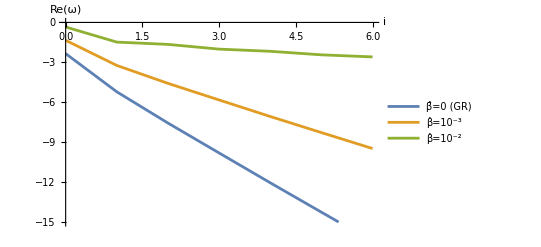

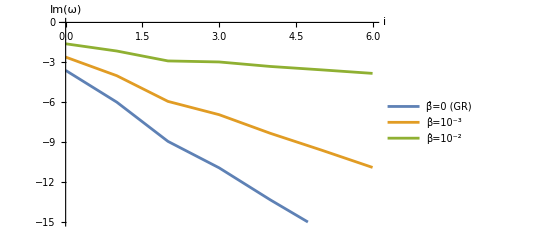

```mathematica
ListPlot[dataRe,Joined->{True,True,True, True},PlotRange->{{0,6},{0,-15}},PlotLegends->{"β̂=0 (GR)","β̂=10^-3","β̂=10^-2","β̂=10^-1"},AxesLabel->{"i","Re(ω)"}]
ListPlot[dataIm,Joined->{True,True,True, True},PlotRange->{{0,6},{0,-15}},PlotLegends->{"β̂=0 (GR)","β̂=10^-3","β̂=10^-2","β̂=10^-1"},AxesLabel->{"i","Im(ω)"}]
```

## 8. Fisher information forecast

Here we will apply a Fisher analysis to estimate detectability of the A_Ti parameters. We follow the methodology laid out in https://arxiv.org/pdf/gr-qc/0512160.pdf.
We begin by constructing the waveform.

```mathematica
(*frequency, damping time and quality factor*)
DefScalarFunction[tlm,PrintAs->"τ_lm"];
DefScalarFunction[flm,PrintAs->"f_lm"];
DefConstantSymbol[t0,PrintAs->"τ_0"];
DefConstantSymbol[f0,PrintAs->"f_0"];
DefScalarFunction[Qlm,PrintAs->"Q_lm"];
(*polarized waveforms*)
DefScalarFunction[hp1,PrintAs->"h_(+1)"];
DefScalarFunction[hc1,PrintAs->"h_x1"];
DefScalarFunction[hp2,PrintAs->"(h_(+2))^*"];
DefScalarFunction[hc2,PrintAs->"h_x2^*"];
(*DefScalarFunction[Fp,PrintAs->"F_+"];
DefScalarFunction[Fc,PrintAs->"F_x"];*)
DefScalarFunction[AA,PrintAs->"A"];
DefScalarFunction[Ap,PrintAs->"A^+"];
DefScalarFunction[Ac,PrintAs->"A^x"];
DefScalarFunction[Nc,PrintAs->"N_x"];
DefScalarFunction[phip,PrintAs->"ϕ_+"];
DefScalarFunction[phix,PrintAs->"ϕ_x"];
DefScalarFunction[phi0,PrintAs->"ϕ_0"];
DefScalarFunction[Slm,PrintAs->"S_lm"];
DefScalarFunction[Sh, PrintAs->"S_h"];

(*rules*)
ToQ={tlm->Qlm/(Pi flm)};
ToA={Ac->Ap Nc,Ap^2->AA^2/(1+Nc^2),1/Ap^2->(1+Nc^2)/AA^2};
Tophip={phix->phip+phi0};
Tophix={phip+phi0->phix};
```

### Single-parameter error

First of all we derive the general expressions for the single-parameter error. We define the expression for the strain functions

```mathematica
EToh={hp1->Ap*Exp[-Pi flm[betaHat]t/Qlm[betaHat]]*Cos[2*Pi*flm[betaHat]*t+phip]Slm/.ToA,
hp2->Ap*Exp[Pi flm[betaHat]t/Qlm[betaHat]]*Cos[2*Pi*flm[betaHat]*t+phip]Slm/.ToA,
hc1->Ac*Exp[-Pi flm[betaHat]t/Qlm[betaHat]]*Sin[2*Pi*flm[betaHat]*t+phix]Slm/.ToA/.Tophip,
hc2->Ac*Exp[Pi flm[betaHat]t/Qlm[betaHat]]*Sin[2*Pi*flm[betaHat]*t+phix]Slm/.ToA/.Tophip}
```

{h_(+1)→A^+ ⅇ^(-(π t f_lm[β̂])/Q_lm[β̂]) S_lm Cos[ϕ_++2 π t f_lm[β̂]],(h_(+2))^*→A^+ ⅇ^((π t f_lm[β̂])/Q_lm[β̂]) S_lm Cos[ϕ_++2 π t f_lm[β̂]],h_x1→A^+ ⅇ^(-(π t f_lm[β̂])/Q_lm[β̂]) N_x S_lm Sin[ϕ_0+ϕ_++2 π t f_lm[β̂]],h_x2^*→A^+ ⅇ^((π t f_lm[β̂])/Q_lm[β̂]) N_x S_lm Sin[ϕ_0+ϕ_++2 π t f_lm[β̂]]}

Here we calculate an expression for the SNR. For an explanation of the assumptions used here, check the paper. Note the SNR in the paper is simplified compared to this one by taking ϕ^+=±π/4=ϕ^X. We don’t do this here to show that this assumption is not necessary (just for aesthetics).

```mathematica
1/Sh(hp1*hp1-hp2*hp2+hc1*hc1-hc2*hc2);
%/.EToh;
2*Integrate[%,t];
-%/.t->0/.Slm->1;
SNR=%/.ToA/.ToQ/.Tophix//FullSimplify
```

(A^2 Q_lm[β̂] (1+N_x^2+Cos[2 ϕ_+]-N_x^2 Cos[2 ϕ_x]+4 (1+N_x^2) Q_lm[β̂]^2))/((1+N_x^2) π S_h f_lm[β̂] (1+4 Q_lm[β̂]^2))

Because we have only one parameter to constrain, the Fisher matrix becomes a ‘Fisher Scalar’. The final result of the following line is (σ_((Â)_Ti))^2 ρ^2, i.e. the error on this parameter squared and weighted by the SNR. Note we haven’t assumed anything on ϕ^+,ϕ^X to obtain this simple expression. We also note that this is independent of the amplitude A, which means our results are independent on any normalisation factors on the waveforms (which can be different for different detectors).

```mathematica
derFTh=Simplify[D[hp1/.EToh,betaHat]*D[hp1/.EToh,betaHat]-D[hp2/.EToh,betaHat]*D[hp2/.EToh,betaHat]+D[hc1/.EToh,betaHat]*D[hc1/.EToh,betaHat]-D[hc2/.EToh,betaHat]*D[hc2/.EToh,betaHat]]/.Slm->1;
2/Sh*Integrate[derFTh//Expand,t];
-Simplify[%/.t->0];
Corr=%/.{phi0+phip->phix};
SNR/Corr;
errorSNR=Simplify[Series[%,{Qlm[betaHat],Infinity,3}]//Normal]/.ToA
```

f_lm[β̂]^2/(2 Q_lm[β̂]^2 f_lm'[β̂]^2)

Here we present for reference the same expression for the error without making use of the large Q approximation.

```mathematica
SNR/Corr/.ToA//Simplify
```

(2 f_lm[β̂]^2 Q_lm[β̂]^2 (1+4 Q_lm[β̂]^2)^2 (1+N_x^2+Cos[2 ϕ_+]-N_x^2 Cos[2 ϕ_x]+4 (1+N_x^2) Q_lm[β̂]^2))/(256 (1+N_x^2) Q_lm[β̂]^8 f_lm'[β̂]^2+256 (1+N_x^2) Q_lm[β̂]^10 f_lm'[β̂]^2-2 (1+N_x^2+Cos[2 ϕ_+]-N_x^2 Cos[2 ϕ_x]) f_lm[β̂] Q_lm[β̂] f_lm'[β̂] Q_lm'[β̂]-24 (1+N_x^2) f_lm[β̂] Q_lm[β̂]^3 f_lm'[β̂] Q_lm'[β̂]+32 (-3-3 N_x^2+Cos[2 ϕ_+]-N_x^2 Cos[2 ϕ_x]) f_lm[β̂] Q_lm[β̂]^5 f_lm'[β̂] Q_lm'[β̂]-128 (1+N_x^2) f_lm[β̂] Q_lm[β̂]^7 f_lm'[β̂] Q_lm'[β̂]+(1+N_x^2+Cos[2 ϕ_+]-N_x^2 Cos[2 ϕ_x]) f_lm[β̂]^2 Q_lm'[β̂]^2+16 Q_lm[β̂]^6 ((6+6 N_x^2+Cos[2 ϕ_+]-N_x^2 Cos[2 ϕ_x]) f_lm'[β̂]^2+4 (1+N_x^2) f_lm[β̂]^2 Q_lm'[β̂]^2)+8 Q_lm[β̂]^4 ((2+2 N_x^2+Cos[2 ϕ_+]-N_x^2 Cos[2 ϕ_x]) f_lm'[β̂]^2+6 (1+N_x^2) f_lm[β̂]^2 Q_lm'[β̂]^2)+Q_lm[β̂]^2 ((1+N_x^2+Cos[2 ϕ_+]-N_x^2 Cos[2 ϕ_x]) f_lm'[β̂]^2+12 (1+N_x^2-Cos[2 ϕ_+]+N_x^2 Cos[2 ϕ_x]) f_lm[β̂]^2 Q_lm'[β̂]^2))

### Constraint on β

The rule below extracts f , τ and Q from the QNM above. See paper for more clarification.

```mathematica
ruleftQ={flm[betaHat]->1/(2Pi)FullSimplify[Re[QNM7//Normal],betaHat∈Reals],
Derivative[1][flm][betaHat]->1/(2Pi)D[FullSimplify[Re[QNM7//Normal],betaHat∈Reals],betaHat],
Qlm[betaHat]->Pi*(1/FullSimplify[Im[QNM7//Normal],betaHat∈Reals])*1/(2Pi)FullSimplify[Re[QNM7//Normal],betaHat∈Reals]}
```

{f_lm[β̂]→1/(2 π)(0.3736193572264525980387249878037479471427024454062+β̂ (1.67503141016079481345267981187053217807378467+β̂ (-2.3854844722997630185620451444645149548537+β̂ (10.40324341681451200663615136885266696+β̂ (-59.13364850128448772345777412913+β̂ (337.0563967888400892559188+β̂ (-2076.75555833917303329+13129.52405457888756 β̂))))))),f_lm'[β̂]→1/(2 π)(1.67503141016079481345267981187053217807378467+β̂ (-2.3854844722997630185620451444645149548537+β̂ (10.40324341681451200663615136885266696+β̂ (-59.13364850128448772345777412913+β̂ (337.0563967888400892559188+β̂ (-2076.75555833917303329+13129.52405457888756 β̂)))))+β̂ (-2.3854844722997630185620451444645149548537+β̂ (10.40324341681451200663615136885266696+β̂ (-59.13364850128448772345777412913+β̂ (337.0563967888400892559188+β̂ (-2076.75555833917303329+13129.52405457888756 β̂))))+β̂ (10.40324341681451200663615136885266696+β̂ (-59.13364850128448772345777412913+β̂ (337.0563967888400892559188+β̂ (-2076.75555833917303329+13129.52405457888756 β̂)))+β̂ (-59.13364850128448772345777412913+β̂ (337.0563967888400892559188+β̂ (-2076.75555833917303329+13129.52405457888756 β̂))+β̂ (337.0563967888400892559188+β̂ (-2076.75555833917303329+13129.52405457888756 β̂)+β̂ (-2076.75555833917303329+26259.04810915777511 β̂)))))),Q_lm[β̂]→(0.3736193572264525980387249878037479471427024454062+β̂ (1.67503141016079481345267981187053217807378467+β̂ (-2.3854844722997630185620451444645149548537+β̂ (10.40324341681451200663615136885266696+β̂ (-59.13364850128448772345777412913+β̂ (337.0563967888400892559188+β̂ (-2076.75555833917303329+13129.52405457888756 β̂)))))))/(2 (-0.08889097955333289780952833450556567340781026510797+β̂ (-0.4967372562293600066025308163251122328568454+β̂ (0.164078570400957781954815274877250336421+β̂ (-2.02189994957810149085659108522388449+β̂ (9.40066547266754327980113611915+β̂ (-61.835122212569949890177482+(394.55252039039995167-2637.05210980228103 β̂) β̂)))))))}

Now we can use this rule to put the numerical values in the single-parameter expression derived above. We take β to zero to obtain the leading order term to the error. To obtain a final value for the error, we need to take the square-root (recall what we have here is σ_β^2 ρ^2) and select a value for the SNR. Here we choose ρ = 10^5, which should be typical of LISA, but in the paper we consider a larger number of detectors.

```mathematica
errorSNR/.ruleftQ/.betaHat->0
√%
errorbeta=%*10^-5//ScientificForm
```

0.0056324775457554239993450445053098603132621933

0.0750498337490192179262761029889271551218483029

7.50498337490192179262761029889271551218483029×10^-7

## 9. Large-r effects on QNMs

### Metric: Λ corrections

```mathematica
f2[r_]=(1-(2mass)/r-Λ/3 r^2)
VGR=(B[r] (l+l^2-(6mass)/r[]))/r^2
```

1-(2 M)/r-(r^2 Λ)/3

(B[r] (l+l^2-(6 M)/r))/r^2

```mathematica
WKBFormula[6,VGR/.ToM/.ToGeomUn/.{l->2,mass->1,Λ->0,r[]->r},f2[r]/.{mass->1,Λ->0},{r,3},0]
WKBFormula[6,VGR/.ToM/.ToGeomUn/.{l->2,mass->1,Λ->0.02,r[]->r},f2[r]/.{mass->1,Λ->0.02},{r,3},0]
WKBFormula[6,VGR/.ToM/.ToGeomUn/.{l->2,mass->1,Λ->0.04,r[]->r},f2[r]/.{mass->1,Λ->0.04},{r,3},0]
WKBFormula[6,VGR/.ToM/.ToGeomUn/.{l->2,mass->1,Λ->0.06,r[]->r},f2[r]/.{mass->1,Λ->0.06},{r,3},0]
WKBFormula[6,VGR/.ToM/.ToGeomUn/.{l->2,mass->1,Λ->0.08,r[]->r},f2[r]/.{mass->1,Λ->0.08},{r,3},0]
WKBFormula[6,VGR/.ToM/.ToGeomUn/.{l->2,mass->1,Λ->0.09,r[]->r},f2[r]/.{mass->1,Λ->0.09},{r,3},0]
WKBFormula[6,VGR/.ToM/.ToGeomUn/.{l->2,mass->1,Λ->0.10,r[]->r},f2[r]/.{mass->1,Λ->0.10},{r,3},0]
WKBFormula[6,VGR/.ToM/.ToGeomUn/.{l->2,mass->1,Λ->0.11,r[]->r},f2[r]/.{mass->1,Λ->0.11},{r,3},0]
```

{0.373619-0.088891 ⅈ,0.373504-0.0889183 ⅈ,0.373553-0.089124 ⅈ,0.373162-0.0892174 ⅈ,0.37435-0.0940632 ⅈ,0.39885-0.0882854 ⅈ,r→3.28078}

{0.338373-0.0816937 ⅈ,0.338272-0.081718 ⅈ,0.338308-0.0818656 ⅈ,0.337962-0.0819495 ⅈ,0.338987-0.0860823 ⅈ,0.360733-0.0808931 ⅈ,r→3.22503}

{0.298895-0.0732495 ⅈ,0.298819-0.073268 ⅈ,0.298842-0.0733613 ⅈ,0.298558-0.073431 ⅈ,0.29941-0.0768203 ⅈ,0.318298-0.0722618 ⅈ,r→3.17183}

{0.253295-0.0630145 ⅈ,0.253251-0.0630255 ⅈ,0.253263-0.0630752 ⅈ,0.253061-0.0631256 ⅈ,0.25373-0.0657576 ⅈ,0.269515-0.0619063 ⅈ,r→3.12093}

{0.197493-0.0498652 ⅈ,0.19747-0.049871 ⅈ,0.197475-0.0498935 ⅈ,0.197365-0.0499215 ⅈ,0.197842-0.0517769 ⅈ,0.210009-0.0487773 ⅈ,r→3.07213}

{0.162596-0.0413657 ⅈ,0.162605-0.0413634 ⅈ,0.162609-0.0413793 ⅈ,0.162543-0.0413961 ⅈ,0.162917-0.0428411 ⅈ,0.172886-0.0403708 ⅈ,r→3.04847}

{0.112368-0.0317123 ⅈ,0.117918-0.0302196 ⅈ,0.117918-0.0302213 ⅈ,0.117892-0.0302282 ⅈ,0.118148-0.0312151 ⅈ,0.125345-0.0294229 ⅈ,r→3.02526}

{2.17062-0.00115694 ⅈ,0.0569787-0.0440741 ⅈ,0.0373648-0.00959607 ⅈ,0.0372702-0.00962043 ⅈ,0.0373468-0.00991292 ⅈ,0.0396123-0.00934597 ⅈ,r→3.0025}

```mathematica
DtortΛ[xx_]:=f2[r]D[xx,r](*/.mass->1*)
V1derΛ[r,Λ_]=DtortΛ[(VGR/.ToM/.ToGeomUn)/.{l->2,(*mass->1,*)r[]->r}]//Simplify;
V2derΛ[r,Λ_]=DtortΛ[%]//Simplify;
V3derΛ[r,Λ_]=DtortΛ[%]//Simplify;
V4derΛ[r,Λ_]=DtortΛ[%]//Simplify;
V5derΛ[r,Λ_]=DtortΛ[%]//Simplify;
V6derΛ[r,Λ_]=DtortΛ[%]//Simplify;
V7derΛ[r,Λ_]=DtortΛ[%]//Simplify;
V8derΛ[r,Λ_]=DtortΛ[%]//Simplify;
V9derΛ[r,Λ_]=DtortΛ[%]//Simplify;
V10derΛ[r,Λ_]=DtortΛ[%]//Simplify;
V11derΛ[r,Λ_]=DtortΛ[%]//Simplify;
V12derΛ[r,Λ_]=DtortΛ[%]//Simplify;
```

```mathematica
D[VGR/.ToM/.ToGeomUn/.{Λ->0}//Simplify,r[]]//Simplify
Solve[(%/.ToM/.{l->2,(*mass->1,*)Λ->0})==0]//N
r0GRS=%[[2]]
```

(-48 M^2+6 (3+l+l^2) M r-2 l (1+l) r^2)/r^5

{{r→1.21922 M},{r→3.28078 M}}

{r→3.28078 M}

```mathematica
-D[VGR/.ToM/.ToGeomUn,r[]]/D[D[VGR/.ToM/.ToGeomUn,r[]],r[]]//Simplify;
r0GRSdS={r[]->(r0GRS[[1]][[2]]+%/.ToM/.{l->2(*,mass->1*)}/.r0GRS)}
```

{r→3.28078 M+(3.28078 M (88.581 M^2+3.28078 M^2 (-27+10.7635 M^2 Λ)))/(313.743 M^2+6.56155 M^2 (-54+10.7635 M^2 Λ))}

```mathematica
r0GRSdSsimp={r[]->Series[r0GRSdS[[1]][[2]],{Λ,0,2}]//Normal//Simplify}
%/.{Λ->10^-2}
r0GRSdS/.Λ->10^-2
```

{r→3.28078 M-2.85486 M^3 Λ-4.96846 M^5 Λ^2}

{r→3.28078 M-0.0285486 M^3-0.000496846 M^5}

{r→3.28078 M+(3.28078 M (88.581 M^2+3.28078 M^2 (-27+0.107635 M^2)))/(313.743 M^2+6.56155 M^2 (-54+0.107635 M^2))}

```mathematica
Vdersubsv2SdS[Λ_]={V00->Hold[(VGR/.ToM/.ToGeomUn)/.{l->2(*,mass->1*)}/.r0GRSdSsimp],
V2->Hold[V2derΛ[r,Λ]/.r->r[]/.r0GRSdSsimp],
V3->Hold[V3derΛ[r,Λ]/.r->r[]/.r0GRSdSsimp],
V4->Hold[V4derΛ[r,Λ]/.r->r[]/.r0GRSdSsimp],
V5->Hold[V5derΛ[r,Λ]/.r->r[]/.r0GRSdSsimp],
V6->Hold[V6derΛ[r,Λ]/.r->r[]/.r0GRSdSsimp],
V7->Hold[V7derΛ[r,Λ]/.r->r[]/.r0GRSdSsimp],
V8->Hold[V8derΛ[r,Λ]/.r->r[]/.r0GRSdSsimp],
V9->Hold[V9derΛ[r,Λ]/.r->r[]/.r0GRSdSsimp],
V10->Hold[V10derΛ[r,Λ]/.r->r[]/.r0GRSdSsimp],
V11->Hold[V11derΛ[r,Λ]/.r->r[]/.r0GRSdSsimp],
V12->Hold[V12derΛ[r,Λ]/.r->r[]/.r0GRSdSsimp]}
```

{V00→Hold[VGR/.ToM/.ToGeomUn/.{l→2}/.r0GRSdSsimp],V2→Hold[V2derΛ[r,Λ]/.r→r/.r0GRSdSsimp],V3→Hold[V3derΛ[r,Λ]/.r→r/.r0GRSdSsimp],V4→Hold[V4derΛ[r,Λ]/.r→r/.r0GRSdSsimp],V5→Hold[V5derΛ[r,Λ]/.r→r/.r0GRSdSsimp],V6→Hold[V6derΛ[r,Λ]/.r→r/.r0GRSdSsimp],V7→Hold[V7derΛ[r,Λ]/.r→r/.r0GRSdSsimp],V8→Hold[V8derΛ[r,Λ]/.r→r/.r0GRSdSsimp],V9→Hold[V9derΛ[r,Λ]/.r→r/.r0GRSdSsimp],V10→Hold[V10derΛ[r,Λ]/.r→r/.r0GRSdSsimp],V11→Hold[V11derΛ[r,Λ]/.r→r/.r0GRSdSsimp],V12→Hold[V12derΛ[r,Λ]/.r→r/.r0GRSdSsimp]}

```mathematica
BasicWKBFormula[n,{V00,V2,V3,V4,V5,V6,V7,V8,V9,V10,V11,V12}]/.n->0//Simplify;
%/.Vdersubsv2SdS[Λ]//ReleaseHold;
omeSdS=√%
```

```mathematica
QNMSdS=Series[omeSdS,{Λ,0,10}]//Normal//PowerExpand//Simplify
```

(0.373619-0.088891 ⅈ)/M-(1.67631-0.334626 ⅈ) M Λ-(3.85847-0.899697 ⅈ) M^3 Λ^2-(17.4684-6.04082 ⅈ) M^5 Λ^3-(97.8679-33.8239 ⅈ) M^7 Λ^4-(577.254-139.533 ⅈ) M^9 Λ^5-(4902.94-1253.37 ⅈ) M^11 Λ^6-(28037.8-8899.77 ⅈ) M^13 Λ^7-(223744.-58613.4 ⅈ) M^15 Λ^8-(1.69398×10^6-457403. ⅈ) M^17 Λ^9-(1.26568×10^7-3.55771×10^6 ⅈ) M^19 Λ^10

```mathematica
QNMSdS/.{Λ->0.02,mass->1}
QNMSdS/.{Λ->0,mass->1}
QNMSdS/.{Λ->10^(-52+18),mass->1}
```

0.338392-0.0817843 ⅈ

0.373619-0.088891 ⅈ

0.373619-0.088891 ⅈ